```mathematica
ClearAll["Global`*"]
```

## Beginning stuff

Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

```mathematica
Get["funcs_for_stepMonitor_stringConv_plotSetOfInds_etc.m"]
(*Includes (as of 2018/03/29)
makeErrorData[x_,y_,yErr_]
kPlotStepMonitorData[kStepVals_]
gPlotStepMonitorData[gStepVals_]
tStringToSec[tString_]
minTidInd[tSearchString_,tStringArr_]
tPlotInds[inds_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tPlotRange[ind1_,ind2_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tablePlotMov[indStart_,indEnd1_,indEnd2_,mom_,momErr_,pRange_]
tablePlotsCombineAndAnimate[mov1_,mov2_]*)
```

Initialize J-V, J_E-V data

```mathematica
orbit=1612;
```

```mathematica
makePlots=1;
```

#### pot offset (in V)?

```mathematica
potTFactor=0;
```

```mathematica
If[potTFactor == 0,potFactorString="",potFactorString=ToString@StringForm["__`1`V_offset",potTFactor]];
```

#### Spectra average interval?

```mathematica
spectraAverageInterval=2;
```

```mathematica
specAvgItvlString=If[spectraAverageInterval==2,"",ToString@StringForm["-avgItvl`1`",spectraAverageInterval]];
```

#### Which pot to use for density?

```mathematica
densPot=pots;
```

```mathematica
densPot=downepots;
```

### And the data ...

```mathematica
peakEBoundsIndShift=-2;
```

```mathematica
peakEBoundsIndShift=False;
```

#### peakEBounds shift selection and string setup

```mathematica
peakEBoundsSuff="";If[ToString[Head[peakEBoundsIndShift]]=="Integer",peakEBoundsSuff=ToString@StringForm["-peakE_indShift_eq_`1`",peakEBoundsIndShift]];
```

#### These are derived using peakE_bounds_indShift=[-2,0]

```mathematica
If[peakEBoundsIndShift==-2,
Switch[spectraAverageInterval,
2,
time={"12:00:24.114","12:00:24.745","12:00:25.376","12:00:26.006","12:00:26.637","12:00:27.268","12:00:27.898","12:00:28.529","12:00:29.159","12:00:29.790","12:00:30.421","12:00:31.051","12:00:31.682","12:00:32.313","12:00:32.943","12:00:33.574","12:00:34.205","12:00:34.835","12:00:35.466","12:00:36.096","12:00:36.727","12:00:37.358","12:00:37.988","12:00:38.619","12:00:39.250","12:00:39.880","12:00:40.511","12:00:41.142","12:00:41.772","12:00:42.403","12:00:43.033","12:00:43.664","12:00:44.295","12:00:44.925","12:00:45.556","12:00:46.187","12:00:46.817","12:00:47.448","12:00:48.079","12:00:48.709","12:00:49.340","12:00:49.971","12:00:50.601","12:00:51.232","12:00:51.863","12:00:52.493","12:00:53.124","12:00:53.755","12:00:54.385","12:00:55.016","12:00:55.647","12:00:56.277","12:00:56.908","12:00:57.539","12:00:58.169","12:00:58.800","12:00:59.431","12:01:00.061","12:01:00.692","12:01:01.323","12:01:01.953","12:01:02.584","12:01:03.215","12:01:03.845","12:01:04.476","12:01:05.107","12:01:05.737","12:01:06.368","12:01:06.999","12:01:07.629","12:01:08.260","12:01:08.891","12:01:09.521","12:01:10.152","12:01:10.783","12:01:11.413","12:01:12.044","12:01:12.675","12:01:13.305","12:01:13.936","12:01:14.567","12:01:15.197","12:01:15.828","12:01:16.459","12:01:17.090","12:01:17.720","12:01:18.351","12:01:18.982","12:01:19.612","12:01:20.243","12:01:20.874","12:01:21.504","12:01:22.135","12:01:22.766","12:01:23.397","12:01:24.027","12:01:24.658","12:01:25.289","12:01:25.919","12:01:26.550","12:01:27.181","12:01:27.811","12:01:28.442","12:01:29.073","12:01:29.703","12:01:30.334","12:01:30.965","12:01:31.596","12:01:32.226","12:01:32.857","12:01:33.488","12:01:34.118","12:01:34.749","12:01:35.380","12:01:36.010","12:01:36.641","12:01:37.272","12:01:37.903","12:01:38.533","12:01:39.164","12:01:39.795","12:01:40.425","12:01:41.056","12:01:41.687","12:01:42.318","12:01:42.948","12:01:43.579","12:01:44.210","12:01:44.840","12:01:45.471","12:01:46.102","12:01:46.733"};
pots={815.36,1128.96,1128.96,1379.84,1379.84,1379.84,1572.48,1232.00,1429.12,1330.56,1205.12,1012.48,1012.48,913.92,777.28,840.00,777.28,777.28,840.00,913.92,913.92,1012.48,1086.40,951.58,940.80,689.92,960.96,934.08,1133.44,1008.00,1008.00,1133.44,1133.44,1133.44,1008.00,934.08,741.44,592.48,480.48,412.72,344.96,344.96,172.48,344.96,564.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,203.84,282.24,282.24,203.84,235.20,407.68,407.68,344.96,203.84,235.20,368.06,378.84,453.88,441.56,358.82,352.66,282.24,235.20,235.20,172.48,141.12,141.12,172.48,203.84,344.96,430.78,504.28,605.92,605.92,749.28,749.28,884.80,913.92,913.92,913.92,913.92,913.92,616.00,616.00,566.72,529.76,393.12,346.08,282.24,235.20,235.20,189.42,131.46,299.18,581.42,706.86,849.24,717.64,562.80,655.20,430.78,364.98,378.84,358.82,214.62,355.74,220.78,161.14,140.70,197.68,302.96,337.68,362.32,309.96,293.02};
curs={0.936,0.845,1.103,0.721,0.834,0.601,0.608,0.781,0.802,0.844,0.905,0.827,0.719,0.600,0.804,0.612,0.608,0.677,0.597,0.594,0.669,0.698,0.714,1.272,1.206,0.662,0.759,0.699,0.432,0.673,0.729,0.524,0.490,0.475,0.672,0.578,0.552,0.490,0.472,0.426,0.430,0.274,0.304,0.090,0.055,0.125,0.135,0.268,0.285,0.410,0.359,0.401,0.439,0.461,0.483,0.454,0.308,0.452,0.455,0.451,0.586,0.492,0.653,0.544,0.327,0.215,0.370,0.467,0.610,0.658,0.637,0.519,0.850,1.349,1.119,1.174,1.449,1.167,1.240,1.101,1.041,0.754,0.546,0.732,0.820,0.864,1.141,1.356,1.566,1.072,1.414,1.507,1.519,1.193,1.308,1.141,0.989,1.108,0.940,1.003,1.061,0.963,0.608,0.501,0.649,0.214,0.219,0.278,0.508,0.496,0.495,0.892,1.381,1.362,1.708,0.919,0.826,1.053,0.833,0.756,0.978,0.627,0.717,0.714,0.688,0.533,0.383,0.700,0.846,0.849,0.941,0.911};
curErrs={0.037,0.042,0.038,0.032,0.037,0.039,0.032,0.035,0.035,0.041,0.042,0.032,0.036,0.045,0.040,0.036,0.039,0.038,0.032,0.036,0.039,0.046,0.042,0.048,0.053,0.045,0.043,0.042,0.037,0.058,0.047,0.037,0.041,0.035,0.054,0.048,0.047,0.041,0.041,0.045,0.040,0.043,0.032,0.025,0.015,0.042,0.022,0.038,0.039,0.083,0.043,0.037,0.055,0.068,0.055,0.049,0.044,0.103,0.104,0.051,0.054,0.135,0.075,0.058,0.034,0.144,0.068,0.065,0.095,0.108,0.085,0.093,0.075,0.110,0.099,0.079,0.092,0.141,0.093,0.098,0.045,0.044,0.032,0.041,0.037,0.052,0.049,0.043,0.051,0.046,0.056,0.051,0.058,0.062,0.057,0.047,0.086,0.156,0.105,0.106,0.114,0.138,0.095,0.078,0.047,0.034,0.022,0.024,0.033,0.031,0.039,0.051,0.066,0.060,0.081,0.057,0.049,0.050,0.040,0.027,0.040,0.025,0.029,0.028,0.026,0.024,0.037,0.037,0.036,0.042,0.031,0.057};
jes={1.069,1.187,1.553,1.149,1.319,0.945,0.802,0.720,0.704,0.693,0.630,0.513,0.436,0.356,0.437,0.368,0.333,0.379,0.366,0.374,0.417,0.431,0.693,1.378,1.312,0.590,0.636,0.510,0.354,0.475,0.518,0.429,0.412,0.407,0.488,0.423,0.370,0.293,0.266,0.229,0.233,0.163,0.146,0.075,0.066,0.083,0.087,0.129,0.137,0.178,0.173,0.177,0.186,0.179,0.191,0.190,0.136,0.200,0.198,0.210,0.256,0.193,0.276,0.269,0.200,0.126,0.195,0.297,0.378,0.371,0.277,0.238,0.473,0.681,0.633,0.671,0.722,0.590,0.540,0.453,0.450,0.318,0.261,0.300,0.353,0.385,0.617,0.818,1.045,0.759,0.962,1.155,1.151,0.897,0.880,0.796,0.675,0.753,0.648,0.572,0.608,0.560,0.378,0.305,0.374,0.188,0.188,0.214,0.310,0.280,0.363,0.746,1.265,1.405,1.567,0.715,0.641,0.788,0.601,0.596,0.739,0.487,0.566,0.427,0.396,0.338,0.306,0.515,0.616,0.577,0.618,0.562};
jeErrs={0.189,0.262,0.220,0.210,0.242,1.602,0.174,0.151,0.190,0.152,0.131,0.087,0.110,0.112,0.105,0.090,0.114,0.095,0.106,0.096,0.101,0.117,0.190,0.230,0.240,0.310,0.158,0.124,0.117,0.166,0.138,0.131,0.191,0.156,0.172,0.122,0.123,0.129,0.099,0.128,0.098,0.206,0.044,0.080,0.087,0.201,0.054,0.051,0.121,0.112,0.117,0.059,0.145,0.167,0.237,0.072,0.060,0.216,0.141,0.237,0.102,0.146,0.106,0.105,0.082,0.231,0.134,0.147,0.267,0.254,0.114,0.140,0.285,0.313,0.203,0.179,0.185,0.214,0.139,0.133,0.084,0.061,0.070,0.062,0.066,0.085,0.129,0.133,0.190,0.139,0.177,0.177,0.180,0.203,0.159,0.146,0.231,0.383,0.287,0.223,0.267,0.249,0.531,0.129,0.090,0.080,0.082,0.064,0.069,0.116,0.229,0.174,0.258,0.290,0.308,0.166,0.188,0.190,0.109,0.128,0.130,0.088,0.116,0.109,0.060,0.090,0.090,0.095,0.130,0.196,0.315,0.132};

gaussbulkEs={1025.15,172.48,885.60,971.46,107.32,956.19,905.23,470.40,611.13,538.22,433.61,587.85,385.02,282.32,389.63,454.98,353.46,353.73,412.01,541.57,406.74,436.98,600.87,689.92,689.92,641.67,712.12,407.68,592.05,476.44,620.86,539.46,416.35,550.63,441.76,407.68,506.15,286.59,376.91,396.36,463.50,370.94,235.20,86.24,86.24,139.99,171.33,172.48,217.21,193.56,235.20,262.30,235.20,235.20,234.81,156.85,86.24,270.99,253.89,174.84,141.19,144.11,214.88,217.32,248.66,172.48,323.93,461.02,406.18,315.99,210.73,230.98,392.91,358.93,447.53,370.44,335.59,434.03,286.72,265.34,256.37,235.20,152.06,137.11,203.84,235.20,301.81,363.67,453.22,413.81,501.17,517.04,519.50,458.63,484.84,518.04,547.71,514.24,348.31,364.75,344.85,260.27,407.34,282.24,172.48,235.20,233.50,234.03,172.48,109.16,178.02,510.06,505.15,875.68,795.33,481.62,501.97,547.27,311.40,405.27,250.71,273.46,344.96,281.75,172.48,172.48,172.48,86.85,407.34,208.20,203.84,191.86};

kappabulkEs={609.09,86.71,941.03,941.36,107.97,950.02,727.61,611.62,570.04,567.52,452.39,382.88,346.29,314.46,318.17,345.97,355.52,315.42,404.64,360.24,397.38,396.44,557.19,766.36,786.24,553.07,532.65,457.46,517.38,497.51,485.90,576.64,586.45,589.13,584.90,512.07,397.18,370.06,309.72,299.35,235.20,203.84,123.50,103.57,117.12,86.24,155.36,111.41,127.26,165.91,144.35,188.10,119.64,148.07,140.60,266.94,134.04,195.70,185.72,141.12,269.05,176.35,205.53,223.55,283.25,120.31,308.80,400.80,398.67,388.12,281.60,220.09,339.57,376.36,431.99,368.42,347.84,394.07,343.50,240.94,335.04,205.34,135.58,109.43,163.08,158.29,324.83,379.14,470.01,487.66,434.61,567.96,521.28,535.14,461.29,413.38,476.78,479.45,483.80,348.09,316.43,336.57,219.13,141.12,91.90,202.70,210.95,142.93,111.66,87.17,109.37,430.83,641.67,748.65,654.33,468.59,510.77,450.87,322.88,220.89,470.40,233.83,172.48,242.68,115.38,171.82,171.69,89.39,316.75,335.99,355.96,344.96};,
3,
time={"12:00:24.114","12:00:25.060","12:00:26.006","12:00:26.952","12:00:27.898","12:00:28.844","12:00:29.790","12:00:30.736","12:00:31.682","12:00:32.628","12:00:33.574","12:00:34.520","12:00:35.466","12:00:36.412","12:00:37.358","12:00:38.304","12:00:39.250","12:00:40.196","12:00:41.142","12:00:42.088","12:00:43.033","12:00:43.979","12:00:44.925","12:00:45.871","12:00:46.817","12:00:47.763","12:00:48.709","12:00:49.655","12:00:50.601","12:00:51.547","12:00:52.493","12:00:53.439","12:00:54.385","12:00:55.331","12:00:56.277","12:00:57.223","12:00:58.169","12:00:59.115","12:01:00.061","12:01:01.007","12:01:01.953","12:01:02.899","12:01:03.845","12:01:04.791","12:01:05.737","12:01:06.683","12:01:07.629","12:01:08.575","12:01:09.521","12:01:10.467","12:01:11.413","12:01:12.359","12:01:13.305","12:01:14.251","12:01:15.197","12:01:16.144","12:01:17.090","12:01:18.036","12:01:18.982","12:01:19.928","12:01:20.874","12:01:21.820","12:01:22.766","12:01:23.712","12:01:24.658","12:01:25.604","12:01:26.550","12:01:27.496","12:01:28.442","12:01:29.388","12:01:30.334","12:01:31.280","12:01:32.226","12:01:33.172","12:01:34.118","12:01:35.064","12:01:36.010","12:01:36.957","12:01:37.903","12:01:38.849","12:01:39.795","12:01:40.741","12:01:41.687","12:01:42.633","12:01:43.579","12:01:44.525","12:01:45.471","12:01:46.417"};
pots={940.80,1128.96,1379.84,1379.84,1671.04,1429.12,1330.56,1205.12,1012.48,913.92,840.00,777.28,840.00,913.92,1012.48,1211.84,940.80,1010.24,1059.52,1008.00,1008.00,1133.44,1133.44,1008.00,741.44,543.20,412.72,344.96,172.48,407.68,172.48,172.48,203.84,203.84,203.84,172.48,203.84,172.48,203.84,203.84,203.84,203.84,282.24,172.48,282.24,407.68,344.96,203.84,368.06,453.88,427.70,352.66,282.24,235.20,172.48,141.12,172.48,344.96,498.12,562.80,700.00,749.28,934.08,913.92,913.92,913.92,616.00,566.72,480.48,346.08,282.24,235.20,189.42,302.26,581.42,835.38,717.64,655.20,430.78,372.68,358.82,293.02,220.78,137.62,197.68,337.68,374.64,309.96};
curs={1.114,1.290,1.268,1.236,0.862,0.930,1.078,0.931,0.902,0.877,0.830,0.754,0.784,0.785,0.938,1.531,1.356,0.864,0.726,0.759,0.820,0.796,0.739,0.739,0.637,0.523,0.492,0.441,0.302,0.088,0.153,0.270,0.408,0.517,0.508,0.503,0.554,0.477,0.589,0.563,0.746,0.731,0.659,0.302,0.471,0.858,0.848,0.730,1.260,1.616,1.716,1.607,1.486,1.234,0.890,0.691,1.075,1.184,1.629,1.575,1.599,1.611,1.528,1.478,1.318,1.280,1.130,1.164,0.823,0.646,0.254,0.301,0.556,0.506,1.351,2.231,1.777,1.141,1.138,1.117,0.995,0.820,0.858,0.562,0.508,1.025,0.999,1.097};
curErrs={0.035,0.034,0.035,0.036,0.030,0.031,0.044,0.034,0.030,0.034,0.034,0.038,0.033,0.035,0.037,0.046,0.050,0.038,0.036,0.041,0.042,0.042,0.050,0.039,0.038,0.034,0.042,0.049,0.035,0.015,0.034,0.028,0.042,0.043,0.039,0.045,0.052,0.038,0.097,0.054,0.056,0.081,0.052,0.061,0.082,0.096,0.107,0.083,0.081,0.076,0.082,0.079,0.092,0.082,0.040,0.034,0.036,0.043,0.042,0.052,0.050,0.048,0.049,0.045,0.114,0.085,0.086,0.099,0.098,0.084,0.029,0.025,0.026,0.032,0.049,0.082,0.075,0.049,0.043,0.023,0.032,0.021,0.024,0.022,0.031,0.028,0.029,0.034};
jes={1.250,1.696,1.755,1.662,0.981,0.772,0.799,0.583,0.497,0.468,0.444,0.389,0.441,0.454,0.591,1.511,1.360,0.668,0.519,0.518,0.567,0.580,0.546,0.502,0.389,0.283,0.247,0.224,0.137,0.071,0.087,0.122,0.163,0.198,0.194,0.184,0.204,0.174,0.222,0.221,0.267,0.267,0.295,0.145,0.234,0.460,0.402,0.281,0.602,0.795,0.836,0.713,0.581,0.458,0.331,0.282,0.388,0.568,0.960,0.993,1.078,1.182,1.029,0.939,0.818,0.795,0.603,0.636,0.424,0.328,0.198,0.210,0.309,0.329,1.002,1.965,1.502,0.747,0.784,0.689,0.711,0.545,0.442,0.338,0.358,0.653,0.618,0.631};
jeErrs={0.175,0.192,0.194,0.203,0.145,0.154,0.135,0.104,0.078,0.087,0.079,0.090,0.081,0.082,0.089,0.209,0.225,0.128,0.102,0.116,0.120,0.121,0.170,0.101,0.085,0.075,0.080,0.136,0.044,0.032,0.099,0.069,0.059,0.094,0.061,0.137,0.154,0.057,0.160,0.176,0.084,0.082,0.093,0.177,0.238,0.206,0.172,0.134,0.170,0.152,0.159,0.126,0.130,0.100,0.053,0.050,0.054,0.092,0.128,0.151,0.156,0.148,0.150,0.126,0.447,0.253,0.167,0.202,0.235,0.094,0.063,0.069,0.054,0.173,0.149,0.298,0.242,0.129,0.136,0.102,0.099,0.080,0.067,0.079,0.068,0.097,0.130,0.575};
dens={0.745,0.717,0.610,0.579,0.498,0.774,0.805,0.782,0.787,0.825,0.793,0.810,0.756,0.761,0.886,0.773,0.718,0.764,0.636,0.684,0.742,0.662,0.621,0.666,0.641,0.620,0.651,0.512,0.385,0.088,0.179,0.339,0.581,0.759,0.730,0.737,0.784,0.673,0.823,0.806,0.989,1.094,0.909,0.412,0.601,1.024,0.971,1.183,1.483,1.773,1.859,1.834,1.753,1.619,1.043,0.759,1.224,1.141,1.262,1.312,1.190,1.306,1.252,1.288,1.295,1.238,1.215,1.198,0.879,0.751,0.214,0.266,0.437,0.422,0.762,0.796,0.749,0.739,0.765,0.638,0.619,0.477,0.493,0.357,0.330,0.580,0.578,0.536};
densErr={0.085,0.075,0.052,0.098,0.083,0.075,0.116,0.060,0.082,0.093,0.084,0.141,0.069,0.076,0.073,0.068,0.066,0.106,0.065,0.080,0.107,0.116,0.090,0.060,0.096,0.134,0.111,0.091,0.061,0.052,0.057,0.049,0.170,0.099,0.097,0.105,0.132,0.153,0.110,0.096,0.188,0.185,0.197,0.573,0.148,0.141,0.649,0.157,0.206,0.145,0.160,0.187,0.180,0.179,0.196,0.159,0.140,0.336,0.135,0.418,0.188,0.330,0.345,0.278,0.292,0.202,0.102,0.134,0.108,0.220,0.080,0.116,0.050,0.199,0.110,0.056,0.049,0.047,0.053,0.029,0.046,0.029,0.026,0.020,0.029,0.037,0.033,0.028};
downepots={940.800,1128.960,1379.840,1379.840,1128.960,689.920,689.920,564.480,470.400,470.400,470.400,407.680,470.400,470.400,470.400,940.800,940.800,689.920,689.920,564.480,564.480,689.920,689.920,564.480,470.400,407.680,344.960,344.960,172.480,407.680,172.480,172.480,203.840,203.840,203.840,172.480,203.840,172.480,203.840,203.840,203.840,203.840,282.240,172.480,282.240,407.680,344.960,203.840,344.960,407.680,407.680,344.960,282.240,235.200,172.480,141.120,172.480,344.960,470.400,470.400,564.480,564.480,564.480,470.400,470.400,470.400,344.960,344.960,344.960,235.200,282.240,235.200,172.480,282.240,564.480,815.360,689.920,470.400,407.680,344.960,344.960,282.240,203.840,117.600,117.600,282.240,282.240,282.240};
gaussbulkEs={140.96,1252.00,131.37,1259.30,651.01,526.08,527.68,454.01,347.04,303.75,509.44,442.29,600.22,412.42,404.63,689.92,714.95,480.23,418.91,454.64,676.49,470.40,580.16,497.77,577.29,564.48,307.35,298.57,117.60,203.84,172.48,172.38,146.69,257.61,131.05,169.25,235.20,235.07,192.10,141.12,208.49,180.89,237.43,172.48,172.48,320.93,266.61,255.96,312.97,408.94,402.24,235.20,280.24,264.23,203.84,172.48,235.20,336.32,376.29,455.91,429.80,502.13,572.28,435.03,416.19,544.19,235.20,436.09,391.47,164.56,235.20,206.61,138.04,86.24,814.12,930.85,598.76,359.14,437.65,382.95,469.51,344.96,221.59,172.48,86.24,172.84,407.68,173.02};
kappabulkEs={130.70,984.80,120.11,894.82,616.78,478.41,550.03,493.83,377.27,346.20,332.55,332.94,382.89,345.27,368.25,748.93,803.90,588.57,482.24,439.19,461.01,545.60,466.46,533.09,494.63,357.91,301.50,350.99,124.82,147.91,154.17,110.83,197.01,141.12,217.95,234.85,188.43,226.43,282.24,282.24,234.63,256.65,357.66,119.95,197.72,474.66,185.87,233.85,345.98,431.85,413.94,357.94,333.15,291.73,203.84,125.30,235.20,347.05,343.16,460.90,439.68,571.61,658.24,458.17,480.06,503.36,329.82,235.20,347.98,176.66,123.56,117.60,86.24,89.73,552.02,732.34,677.06,350.94,330.91,298.83,235.20,174.90,157.10,172.48,86.24,264.99,257.22,173.80};
kFAConduct={6.415E-14,6.05E-14,6.309E-14,5.899E-14,5.699E-14,5.994E-14,5.635E-14,3.096E-14,1.958E-14,1.938E-14,1.69E-14,1.205E-14,1.766E-14,2E-14,3.67E-14,7.649E-14,7.241E-14,6.236E-14,4.784E-14,4.217E-14,4.8E-14,5.254E-14,4.25E-14,3.104E-14,1.861E-14,1.461E-14,1.105E-14,7.023E-15,3.68E-15,2.305E-15,2.504E-15,3.007E-15,3.417E-15,3.674E-15,3.685E-15,3.408E-15,4.022E-15,3.476E-15,4.092E-15,4.51E-15,5.059E-15,4.688E-15,6.186E-15,3.568E-15,6.094E-15,1.211E-14,8.75E-15,5.034E-15,1.084E-14,1.368E-14,1.521E-14,1.406E-14,9.667E-15,8.014E-15,5.901E-15,5.352E-15,6.678E-15,1.059E-14,2.357E-14,2.814E-14,4.121E-14,7.266E-14,4.868E-14,2.937E-14,2.477E-14,2.717E-14,1.405E-14,1.462E-14,9.939E-15,8.421E-15,3.966E-15,4.22E-15,6.449E-15,8.286E-15,3.454E-14,6.32E-14,4.58E-14,2.116E-14,2.313E-14,1.324E-14,1.608E-14,1.176E-14,8.285E-15,7.368E-15,7.774E-15,1.262E-14,1.427E-14,1.26E-14};
gFAConduct={6.415E-14,6.05E-14,6.309E-14,5.899E-14,5.699E-14,5.994E-14,5.635E-14,3.096E-14,1.958E-14,1.938E-14,1.69E-14,1.205E-14,1.766E-14,2E-14,3.67E-14,7.649E-14,7.241E-14,6.236E-14,4.784E-14,4.217E-14,4.8E-14,5.254E-14,4.25E-14,3.104E-14,1.861E-14,1.461E-14,1.105E-14,7.023E-15,3.68E-15,2.305E-15,2.504E-15,3.007E-15,3.417E-15,3.674E-15,3.685E-15,3.408E-15,4.022E-15,3.476E-15,4.092E-15,4.51E-15,5.059E-15,4.688E-15,6.186E-15,3.568E-15,6.094E-15,1.211E-14,8.75E-15,5.034E-15,1.084E-14,1.368E-14,1.521E-14,1.406E-14,9.667E-15,8.014E-15,5.901E-15,5.352E-15,6.678E-15,1.059E-14,2.357E-14,2.814E-14,4.121E-14,7.266E-14,4.868E-14,2.937E-14,2.477E-14,2.717E-14,1.405E-14,1.462E-14,9.939E-15,8.421E-15,3.966E-15,4.22E-15,6.449E-15,8.286E-15,3.454E-14,6.32E-14,4.58E-14,2.116E-14,2.313E-14,1.324E-14,1.608E-14,1.176E-14,8.285E-15,7.368E-15,7.774E-15,1.262E-14,1.427E-14,1.26E-14};
,
4,
time=Null;]]
```

If[False==-2,Switch[spectraAverageInterval,
2,time={12:00:24.114,12:00:24.745,12:00:25.376,12:00:26.006,12:00:26.637,12:00:27.268,12:00:27.898,12:00:28.529,12:00:29.159,12:00:29.790,12:00:30.421,12:00:31.051,12:00:31.682,12:00:32.313,12:00:32.943,12:00:33.574,12:00:34.205,12:00:34.835,12:00:35.466,12:00:36.096,12:00:36.727,12:00:37.358,12:00:37.988,12:00:38.619,12:00:39.250,12:00:39.880,12:00:40.511,12:00:41.142,12:00:41.772,12:00:42.403,12:00:43.033,12:00:43.664,12:00:44.295,12:00:44.925,12:00:45.556,12:00:46.187,12:00:46.817,12:00:47.448,12:00:48.079,12:00:48.709,12:00:49.340,12:00:49.971,12:00:50.601,12:00:51.232,12:00:51.863,12:00:52.493,12:00:53.124,12:00:53.755,12:00:54.385,12:00:55.016,12:00:55.647,12:00:56.277,12:00:56.908,12:00:57.539,12:00:58.169,12:00:58.800,12:00:59.431,12:01:00.061,12:01:00.692,12:01:01.323,12:01:01.953,12:01:02.584,12:01:03.215,12:01:03.845,12:01:04.476,12:01:05.107,12:01:05.737,12:01:06.368,12:01:06.999,12:01:07.629,12:01:08.260,12:01:08.891,12:01:09.521,12:01:10.152,12:01:10.783,12:01:11.413,12:01:12.044,12:01:12.675,12:01:13.305,12:01:13.936,12:01:14.567,12:01:15.197,12:01:15.828,12:01:16.459,12:01:17.090,12:01:17.720,12:01:18.351,12:01:18.982,12:01:19.612,12:01:20.243,12:01:20.874,12:01:21.504,12:01:22.135,12:01:22.766,12:01:23.397,12:01:24.027,12:01:24.658,12:01:25.289,12:01:25.919,12:01:26.550,12:01:27.181,12:01:27.811,12:01:28.442,12:01:29.073,12:01:29.703,12:01:30.334,12:01:30.965,12:01:31.596,12:01:32.226,12:01:32.857,12:01:33.488,12:01:34.118,12:01:34.749,12:01:35.380,12:01:36.010,12:01:36.641,12:01:37.272,12:01:37.903,12:01:38.533,12:01:39.164,12:01:39.795,12:01:40.425,12:01:41.056,12:01:41.687,12:01:42.318,12:01:42.948,12:01:43.579,12:01:44.210,12:01:44.840,12:01:45.471,12:01:46.102,12:01:46.733};pots={815.36,1128.96,1128.96,1379.84,1379.84,1379.84,1572.48,1232.,1429.12,1330.56,1205.12,1012.48,1012.48,913.92,777.28,840.,777.28,777.28,840.,913.92,913.92,1012.48,1086.4,951.58,940.8,689.92,960.96,934.08,1133.44,1008.,1008.,1133.44,1133.44,1133.44,1008.,934.08,741.44,592.48,480.48,412.72,344.96,344.96,172.48,344.96,564.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,203.84,282.24,282.24,203.84,235.2,407.68,407.68,344.96,203.84,235.2,368.06,378.84,453.88,441.56,358.82,352.66,282.24,235.2,235.2,172.48,141.12,141.12,172.48,203.84,344.96,430.78,504.28,605.92,605.92,749.28,749.28,884.8,913.92,913.92,913.92,913.92,913.92,616.,616.,566.72,529.76,393.12,346.08,282.24,235.2,235.2,189.42,131.46,299.18,581.42,706.86,849.24,717.64,562.8,655.2,430.78,364.98,378.84,358.82,214.62,355.74,220.78,161.14,140.7,197.68,302.96,337.68,362.32,309.96,293.02};curs={0.936,0.845,1.103,0.721,0.834,0.601,0.608,0.781,0.802,0.844,0.905,0.827,0.719,0.6,0.804,0.612,0.608,0.677,0.597,0.594,0.669,0.698,0.714,1.272,1.206,0.662,0.759,0.699,0.432,0.673,0.729,0.524,0.49,0.475,0.672,0.578,0.552,0.49,0.472,0.426,0.43,0.274,0.304,0.09,0.055,0.125,0.135,0.268,0.285,0.41,0.359,0.401,0.439,0.461,0.483,0.454,0.308,0.452,0.455,0.451,0.586,0.492,0.653,0.544,0.327,0.215,0.37,0.467,0.61,0.658,0.637,0.519,0.85,1.349,1.119,1.174,1.449,1.167,1.24,1.101,1.041,0.754,0.546,0.732,0.82,0.864,1.141,1.356,1.566,1.072,1.414,1.507,1.519,1.193,1.308,1.141,0.989,1.108,0.94,1.003,1.061,0.963,0.608,0.501,0.649,0.214,0.219,0.278,0.508,0.496,0.495,0.892,1.381,1.362,1.708,0.919,0.826,1.053,0.833,0.756,0.978,0.627,0.717,0.714,0.688,0.533,0.383,0.7,0.846,0.849,0.941,0.911};curErrs={0.037,0.042,0.038,0.032,0.037,0.039,0.032,0.035,0.035,0.041,0.042,0.032,0.036,0.045,0.04,0.036,0.039,0.038,0.032,0.036,0.039,0.046,0.042,0.048,0.053,0.045,0.043,0.042,0.037,0.058,0.047,0.037,0.041,0.035,0.054,0.048,0.047,0.041,0.041,0.045,0.04,0.043,0.032,0.025,0.015,0.042,0.022,0.038,0.039,0.083,0.043,0.037,0.055,0.068,0.055,0.049,0.044,0.103,0.104,0.051,0.054,0.135,0.075,0.058,0.034,0.144,0.068,0.065,0.095,0.108,0.085,0.093,0.075,0.11,0.099,0.079,0.092,0.141,0.093,0.098,0.045,0.044,0.032,0.041,0.037,0.052,0.049,0.043,0.051,0.046,0.056,0.051,0.058,0.062,0.057,0.047,0.086,0.156,0.105,0.106,0.114,0.138,0.095,0.078,0.047,0.034,0.022,0.024,0.033,0.031,0.039,0.051,0.066,0.06,0.081,0.057,0.049,0.05,0.04,0.027,0.04,0.025,0.029,0.028,0.026,0.024,0.037,0.037,0.036,0.042,0.031,0.057};jes={1.069,1.187,1.553,1.149,1.319,0.945,0.802,0.72,0.704,0.693,0.63,0.513,0.436,0.356,0.437,0.368,0.333,0.379,0.366,0.374,0.417,0.431,0.693,1.378,1.312,0.59,0.636,0.51,0.354,0.475,0.518,0.429,0.412,0.407,0.488,0.423,0.37,0.293,0.266,0.229,0.233,0.163,0.146,0.075,0.066,0.083,0.087,0.129,0.137,0.178,0.173,0.177,0.186,0.179,0.191,0.19,0.136,0.2,0.198,0.21,0.256,0.193,0.276,0.269,0.2,0.126,0.195,0.297,0.378,0.371,0.277,0.238,0.473,0.681,0.633,0.671,0.722,0.59,0.54,0.453,0.45,0.318,0.261,0.3,0.353,0.385,0.617,0.818,1.045,0.759,0.962,1.155,1.151,0.897,0.88,0.796,0.675,0.753,0.648,0.572,0.608,0.56,0.378,0.305,0.374,0.188,0.188,0.214,0.31,0.28,0.363,0.746,1.265,1.405,1.567,0.715,0.641,0.788,0.601,0.596,0.739,0.487,0.566,0.427,0.396,0.338,0.306,0.515,0.616,0.577,0.618,0.562};jeErrs={0.189,0.262,0.22,0.21,0.242,1.602,0.174,0.151,0.19,0.152,0.131,0.087,0.11,0.112,0.105,0.09,0.114,0.095,0.106,0.096,0.101,0.117,0.19,0.23,0.24,0.31,0.158,0.124,0.117,0.166,0.138,0.131,0.191,0.156,0.172,0.122,0.123,0.129,0.099,0.128,0.098,0.206,0.044,0.08,0.087,0.201,0.054,0.051,0.121,0.112,0.117,0.059,0.145,0.167,0.237,0.072,0.06,0.216,0.141,0.237,0.102,0.146,0.106,0.105,0.082,0.231,0.134,0.147,0.267,0.254,0.114,0.14,0.285,0.313,0.203,0.179,0.185,0.214,0.139,0.133,0.084,0.061,0.07,0.062,0.066,0.085,0.129,0.133,0.19,0.139,0.177,0.177,0.18,0.203,0.159,0.146,0.231,0.383,0.287,0.223,0.267,0.249,0.531,0.129,0.09,0.08,0.082,0.064,0.069,0.116,0.229,0.174,0.258,0.29,0.308,0.166,0.188,0.19,0.109,0.128,0.13,0.088,0.116,0.109,0.06,0.09,0.09,0.095,0.13,0.196,0.315,0.132};gaussbulkEs={1025.15,172.48,885.6,971.46,107.32,956.19,905.23,470.4,611.13,538.22,433.61,587.85,385.02,282.32,389.63,454.98,353.46,353.73,412.01,541.57,406.74,436.98,600.87,689.92,689.92,641.67,712.12,407.68,592.05,476.44,620.86,539.46,416.35,550.63,441.76,407.68,506.15,286.59,376.91,396.36,463.5,370.94,235.2,86.24,86.24,139.99,171.33,172.48,217.21,193.56,235.2,262.3,235.2,235.2,234.81,156.85,86.24,270.99,253.89,174.84,141.19,144.11,214.88,217.32,248.66,172.48,323.93,461.02,406.18,315.99,210.73,230.98,392.91,358.93,447.53,370.44,335.59,434.03,286.72,265.34,256.37,235.2,152.06,137.11,203.84,235.2,301.81,363.67,453.22,413.81,501.17,517.04,519.5,458.63,484.84,518.04,547.71,514.24,348.31,364.75,344.85,260.27,407.34,282.24,172.48,235.2,233.5,234.03,172.48,109.16,178.02,510.06,505.15,875.68,795.33,481.62,501.97,547.27,311.4,405.27,250.71,273.46,344.96,281.75,172.48,172.48,172.48,86.85,407.34,208.2,203.84,191.86};kappabulkEs={609.09,86.71,941.03,941.36,107.97,950.02,727.61,611.62,570.04,567.52,452.39,382.88,346.29,314.46,318.17,345.97,355.52,315.42,404.64,360.24,397.38,396.44,557.19,766.36,786.24,553.07,532.65,457.46,517.38,497.51,485.9,576.64,586.45,589.13,584.9,512.07,397.18,370.06,309.72,299.35,235.2,203.84,123.5,103.57,117.12,86.24,155.36,111.41,127.26,165.91,144.35,188.1,119.64,148.07,140.6,266.94,134.04,195.7,185.72,141.12,269.05,176.35,205.53,223.55,283.25,120.31,308.8,400.8,398.67,388.12,281.6,220.09,339.57,376.36,431.99,368.42,347.84,394.07,343.5,240.94,335.04,205.34,135.58,109.43,163.08,158.29,324.83,379.14,470.01,487.66,434.61,567.96,521.28,535.14,461.29,413.38,476.78,479.45,483.8,348.09,316.43,336.57,219.13,141.12,91.9,202.7,210.95,142.93,111.66,87.17,109.37,430.83,641.67,748.65,654.33,468.59,510.77,450.87,322.88,220.89,470.4,233.83,172.48,242.68,115.38,171.82,171.69,89.39,316.75,335.99,355.96,344.96};,
3,time={12:00:24.114,12:00:25.060,12:00:26.006,12:00:26.952,12:00:27.898,12:00:28.844,12:00:29.790,12:00:30.736,12:00:31.682,12:00:32.628,12:00:33.574,12:00:34.520,12:00:35.466,12:00:36.412,12:00:37.358,12:00:38.304,12:00:39.250,12:00:40.196,12:00:41.142,12:00:42.088,12:00:43.033,12:00:43.979,12:00:44.925,12:00:45.871,12:00:46.817,12:00:47.763,12:00:48.709,12:00:49.655,12:00:50.601,12:00:51.547,12:00:52.493,12:00:53.439,12:00:54.385,12:00:55.331,12:00:56.277,12:00:57.223,12:00:58.169,12:00:59.115,12:01:00.061,12:01:01.007,12:01:01.953,12:01:02.899,12:01:03.845,12:01:04.791,12:01:05.737,12:01:06.683,12:01:07.629,12:01:08.575,12:01:09.521,12:01:10.467,12:01:11.413,12:01:12.359,12:01:13.305,12:01:14.251,12:01:15.197,12:01:16.144,12:01:17.090,12:01:18.036,12:01:18.982,12:01:19.928,12:01:20.874,12:01:21.820,12:01:22.766,12:01:23.712,12:01:24.658,12:01:25.604,12:01:26.550,12:01:27.496,12:01:28.442,12:01:29.388,12:01:30.334,12:01:31.280,12:01:32.226,12:01:33.172,12:01:34.118,12:01:35.064,12:01:36.010,12:01:36.957,12:01:37.903,12:01:38.849,12:01:39.795,12:01:40.741,12:01:41.687,12:01:42.633,12:01:43.579,12:01:44.525,12:01:45.471,12:01:46.417};pots={940.8,1128.96,1379.84,1379.84,1671.04,1429.12,1330.56,1205.12,1012.48,913.92,840.,777.28,840.,913.92,1012.48,1211.84,940.8,1010.24,1059.52,1008.,1008.,1133.44,1133.44,1008.,741.44,543.2,412.72,344.96,172.48,407.68,172.48,172.48,203.84,203.84,203.84,172.48,203.84,172.48,203.84,203.84,203.84,203.84,282.24,172.48,282.24,407.68,344.96,203.84,368.06,453.88,427.7,352.66,282.24,235.2,172.48,141.12,172.48,344.96,498.12,562.8,700.,749.28,934.08,913.92,913.92,913.92,616.,566.72,480.48,346.08,282.24,235.2,189.42,302.26,581.42,835.38,717.64,655.2,430.78,372.68,358.82,293.02,220.78,137.62,197.68,337.68,374.64,309.96};curs={1.114,1.29,1.268,1.236,0.862,0.93,1.078,0.931,0.902,0.877,0.83,0.754,0.784,0.785,0.938,1.531,1.356,0.864,0.726,0.759,0.82,0.796,0.739,0.739,0.637,0.523,0.492,0.441,0.302,0.088,0.153,0.27,0.408,0.517,0.508,0.503,0.554,0.477,0.589,0.563,0.746,0.731,0.659,0.302,0.471,0.858,0.848,0.73,1.26,1.616,1.716,1.607,1.486,1.234,0.89,0.691,1.075,1.184,1.629,1.575,1.599,1.611,1.528,1.478,1.318,1.28,1.13,1.164,0.823,0.646,0.254,0.301,0.556,0.506,1.351,2.231,1.777,1.141,1.138,1.117,0.995,0.82,0.858,0.562,0.508,1.025,0.999,1.097};curErrs={0.035,0.034,0.035,0.036,0.03,0.031,0.044,0.034,0.03,0.034,0.034,0.038,0.033,0.035,0.037,0.046,0.05,0.038,0.036,0.041,0.042,0.042,0.05,0.039,0.038,0.034,0.042,0.049,0.035,0.015,0.034,0.028,0.042,0.043,0.039,0.045,0.052,0.038,0.097,0.054,0.056,0.081,0.052,0.061,0.082,0.096,0.107,0.083,0.081,0.076,0.082,0.079,0.092,0.082,0.04,0.034,0.036,0.043,0.042,0.052,0.05,0.048,0.049,0.045,0.114,0.085,0.086,0.099,0.098,0.084,0.029,0.025,0.026,0.032,0.049,0.082,0.075,0.049,0.043,0.023,0.032,0.021,0.024,0.022,0.031,0.028,0.029,0.034};jes={1.25,1.696,1.755,1.662,0.981,0.772,0.799,0.583,0.497,0.468,0.444,0.389,0.441,0.454,0.591,1.511,1.36,0.668,0.519,0.518,0.567,0.58,0.546,0.502,0.389,0.283,0.247,0.224,0.137,0.071,0.087,0.122,0.163,0.198,0.194,0.184,0.204,0.174,0.222,0.221,0.267,0.267,0.295,0.145,0.234,0.46,0.402,0.281,0.602,0.795,0.836,0.713,0.581,0.458,0.331,0.282,0.388,0.568,0.96,0.993,1.078,1.182,1.029,0.939,0.818,0.795,0.603,0.636,0.424,0.328,0.198,0.21,0.309,0.329,1.002,1.965,1.502,0.747,0.784,0.689,0.711,0.545,0.442,0.338,0.358,0.653,0.618,0.631};jeErrs={0.175,0.192,0.194,0.203,0.145,0.154,0.135,0.104,0.078,0.087,0.079,0.09,0.081,0.082,0.089,0.209,0.225,0.128,0.102,0.116,0.12,0.121,0.17,0.101,0.085,0.075,0.08,0.136,0.044,0.032,0.099,0.069,0.059,0.094,0.061,0.137,0.154,0.057,0.16,0.176,0.084,0.082,0.093,0.177,0.238,0.206,0.172,0.134,0.17,0.152,0.159,0.126,0.13,0.1,0.053,0.05,0.054,0.092,0.128,0.151,0.156,0.148,0.15,0.126,0.447,0.253,0.167,0.202,0.235,0.094,0.063,0.069,0.054,0.173,0.149,0.298,0.242,0.129,0.136,0.102,0.099,0.08,0.067,0.079,0.068,0.097,0.13,0.575};dens={0.745,0.717,0.61,0.579,0.498,0.774,0.805,0.782,0.787,0.825,0.793,0.81,0.756,0.761,0.886,0.773,0.718,0.764,0.636,0.684,0.742,0.662,0.621,0.666,0.641,0.62,0.651,0.512,0.385,0.088,0.179,0.339,0.581,0.759,0.73,0.737,0.784,0.673,0.823,0.806,0.989,1.094,0.909,0.412,0.601,1.024,0.971,1.183,1.483,1.773,1.859,1.834,1.753,1.619,1.043,0.759,1.224,1.141,1.262,1.312,1.19,1.306,1.252,1.288,1.295,1.238,1.215,1.198,0.879,0.751,0.214,0.266,0.437,0.422,0.762,0.796,0.749,0.739,0.765,0.638,0.619,0.477,0.493,0.357,0.33,0.58,0.578,0.536};densErr={0.085,0.075,0.052,0.098,0.083,0.075,0.116,0.06,0.082,0.093,0.084,0.141,0.069,0.076,0.073,0.068,0.066,0.106,0.065,0.08,0.107,0.116,0.09,0.06,0.096,0.134,0.111,0.091,0.061,0.052,0.057,0.049,0.17,0.099,0.097,0.105,0.132,0.153,0.11,0.096,0.188,0.185,0.197,0.573,0.148,0.141,0.649,0.157,0.206,0.145,0.16,0.187,0.18,0.179,0.196,0.159,0.14,0.336,0.135,0.418,0.188,0.33,0.345,0.278,0.292,0.202,0.102,0.134,0.108,0.22,0.08,0.116,0.05,0.199,0.11,0.056,0.049,0.047,0.053,0.029,0.046,0.029,0.026,0.02,0.029,0.037,0.033,0.028};downepots={940.8,1128.96,1379.84,1379.84,1128.96,689.92,689.92,564.48,470.4,470.4,470.4,407.68,470.4,470.4,470.4,940.8,940.8,689.92,689.92,564.48,564.48,689.92,689.92,564.48,470.4,407.68,344.96,344.96,172.48,407.68,172.48,172.48,203.84,203.84,203.84,172.48,203.84,172.48,203.84,203.84,203.84,203.84,282.24,172.48,282.24,407.68,344.96,203.84,344.96,407.68,407.68,344.96,282.24,235.2,172.48,141.12,172.48,344.96,470.4,470.4,564.48,564.48,564.48,470.4,470.4,470.4,344.96,344.96,344.96,235.2,282.24,235.2,172.48,282.24,564.48,815.36,689.92,470.4,407.68,344.96,344.96,282.24,203.84,117.6,117.6,282.24,282.24,282.24};gaussbulkEs={140.96,1252.,131.37,1259.3,651.01,526.08,527.68,454.01,347.04,303.75,509.44,442.29,600.22,412.42,404.63,689.92,714.95,480.23,418.91,454.64,676.49,470.4,580.16,497.77,577.29,564.48,307.35,298.57,117.6,203.84,172.48,172.38,146.69,257.61,131.05,169.25,235.2,235.07,192.1,141.12,208.49,180.89,237.43,172.48,172.48,320.93,266.61,255.96,312.97,408.94,402.24,235.2,280.24,264.23,203.84,172.48,235.2,336.32,376.29,455.91,429.8,502.13,572.28,435.03,416.19,544.19,235.2,436.09,391.47,164.56,235.2,206.61,138.04,86.24,814.12,930.85,598.76,359.14,437.65,382.95,469.51,344.96,221.59,172.48,86.24,172.84,407.68,173.02};kappabulkEs={130.7,984.8,120.11,894.82,616.78,478.41,550.03,493.83,377.27,346.2,332.55,332.94,382.89,345.27,368.25,748.93,803.9,588.57,482.24,439.19,461.01,545.6,466.46,533.09,494.63,357.91,301.5,350.99,124.82,147.91,154.17,110.83,197.01,141.12,217.95,234.85,188.43,226.43,282.24,282.24,234.63,256.65,357.66,119.95,197.72,474.66,185.87,233.85,345.98,431.85,413.94,357.94,333.15,291.73,203.84,125.3,235.2,347.05,343.16,460.9,439.68,571.61,658.24,458.17,480.06,503.36,329.82,235.2,347.98,176.66,123.56,117.6,86.24,89.73,552.02,732.34,677.06,350.94,330.91,298.83,235.2,174.9,157.1,172.48,86.24,264.99,257.22,173.8};kFAConduct={6.415 ⅇ-14,6.05 ⅇ-14,6.309 ⅇ-14,5.899 ⅇ-14,5.699 ⅇ-14,5.994 ⅇ-14,5.635 ⅇ-14,3.096 ⅇ-14,1.958 ⅇ-14,1.938 ⅇ-14,1.69 ⅇ-14,1.205 ⅇ-14,1.766 ⅇ-14,2 ⅇ-14,3.67 ⅇ-14,7.649 ⅇ-14,7.241 ⅇ-14,6.236 ⅇ-14,4.784 ⅇ-14,4.217 ⅇ-14,4.8 ⅇ-14,5.254 ⅇ-14,4.25 ⅇ-14,3.104 ⅇ-14,1.861 ⅇ-14,1.461 ⅇ-14,1.105 ⅇ-14,7.023 ⅇ-15,3.68 ⅇ-15,2.305 ⅇ-15,2.504 ⅇ-15,3.007 ⅇ-15,3.417 ⅇ-15,3.674 ⅇ-15,3.685 ⅇ-15,3.408 ⅇ-15,4.022 ⅇ-15,3.476 ⅇ-15,4.092 ⅇ-15,4.51 ⅇ-15,5.059 ⅇ-15,4.688 ⅇ-15,6.186 ⅇ-15,3.568 ⅇ-15,6.094 ⅇ-15,1.211 ⅇ-14,8.75 ⅇ-15,5.034 ⅇ-15,1.084 ⅇ-14,1.368 ⅇ-14,1.521 ⅇ-14,1.406 ⅇ-14,9.667 ⅇ-15,8.014 ⅇ-15,5.901 ⅇ-15,5.352 ⅇ-15,6.678 ⅇ-15,1.059 ⅇ-14,2.357 ⅇ-14,2.814 ⅇ-14,4.121 ⅇ-14,7.266 ⅇ-14,4.868 ⅇ-14,2.937 ⅇ-14,2.477 ⅇ-14,2.717 ⅇ-14,1.405 ⅇ-14,1.462 ⅇ-14,9.939 ⅇ-15,8.421 ⅇ-15,3.966 ⅇ-15,4.22 ⅇ-15,6.449 ⅇ-15,8.286 ⅇ-15,3.454 ⅇ-14,6.32 ⅇ-14,4.58 ⅇ-14,2.116 ⅇ-14,2.313 ⅇ-14,1.324 ⅇ-14,1.608 ⅇ-14,1.176 ⅇ-14,8.285 ⅇ-15,7.368 ⅇ-15,7.774 ⅇ-15,1.262 ⅇ-14,1.427 ⅇ-14,1.26 ⅇ-14};gFAConduct={6.415 ⅇ-14,6.05 ⅇ-14,6.309 ⅇ-14,5.899 ⅇ-14,5.699 ⅇ-14,5.994 ⅇ-14,5.635 ⅇ-14,3.096 ⅇ-14,1.958 ⅇ-14,1.938 ⅇ-14,1.69 ⅇ-14,1.205 ⅇ-14,1.766 ⅇ-14,2 ⅇ-14,3.67 ⅇ-14,7.649 ⅇ-14,7.241 ⅇ-14,6.236 ⅇ-14,4.784 ⅇ-14,4.217 ⅇ-14,4.8 ⅇ-14,5.254 ⅇ-14,4.25 ⅇ-14,3.104 ⅇ-14,1.861 ⅇ-14,1.461 ⅇ-14,1.105 ⅇ-14,7.023 ⅇ-15,3.68 ⅇ-15,2.305 ⅇ-15,2.504 ⅇ-15,3.007 ⅇ-15,3.417 ⅇ-15,3.674 ⅇ-15,3.685 ⅇ-15,3.408 ⅇ-15,4.022 ⅇ-15,3.476 ⅇ-15,4.092 ⅇ-15,4.51 ⅇ-15,5.059 ⅇ-15,4.688 ⅇ-15,6.186 ⅇ-15,3.568 ⅇ-15,6.094 ⅇ-15,1.211 ⅇ-14,8.75 ⅇ-15,5.034 ⅇ-15,1.084 ⅇ-14,1.368 ⅇ-14,1.521 ⅇ-14,1.406 ⅇ-14,9.667 ⅇ-15,8.014 ⅇ-15,5.901 ⅇ-15,5.352 ⅇ-15,6.678 ⅇ-15,1.059 ⅇ-14,2.357 ⅇ-14,2.814 ⅇ-14,4.121 ⅇ-14,7.266 ⅇ-14,4.868 ⅇ-14,2.937 ⅇ-14,2.477 ⅇ-14,2.717 ⅇ-14,1.405 ⅇ-14,1.462 ⅇ-14,9.939 ⅇ-15,8.421 ⅇ-15,3.966 ⅇ-15,4.22 ⅇ-15,6.449 ⅇ-15,8.286 ⅇ-15,3.454 ⅇ-14,6.32 ⅇ-14,4.58 ⅇ-14,2.116 ⅇ-14,2.313 ⅇ-14,1.324 ⅇ-14,1.608 ⅇ-14,1.176 ⅇ-14,8.285 ⅇ-15,7.368 ⅇ-15,7.774 ⅇ-15,1.262 ⅇ-14,1.427 ⅇ-14,1.26 ⅇ-14};,
4,time=Null;]]

#### These are derived using peakE_bounds_indShift=[-1,0]

```mathematica
If[peakEBoundsIndShift==-1,
Switch[spectraAverageInterval,
2,
	time=Null;,
3,
	time={"12:00:24.114","12:00:25.060","12:00:26.006","12:00:26.952","12:00:27.898","12:00:28.844","12:00:29.790","12:00:30.736","12:00:31.682","12:00:32.628","12:00:33.574","12:00:34.520","12:00:35.466","12:00:36.412","12:00:37.358","12:00:38.304","12:00:39.250","12:00:40.196","12:00:41.142","12:00:42.088","12:00:43.033","12:00:43.979","12:00:44.925","12:00:45.871","12:00:46.817","12:00:47.763","12:00:48.709","12:00:49.655","12:00:50.601","12:00:51.547","12:00:52.493","12:00:53.439","12:00:54.385","12:00:55.331","12:00:56.277","12:00:57.223","12:00:58.169","12:00:59.115","12:01:00.061","12:01:01.007","12:01:01.953","12:01:02.899","12:01:03.845","12:01:04.791","12:01:05.737","12:01:06.683","12:01:07.629","12:01:08.575","12:01:09.521","12:01:10.467","12:01:11.413","12:01:12.359","12:01:13.305","12:01:14.251","12:01:15.197","12:01:16.144","12:01:17.090","12:01:18.036","12:01:18.982","12:01:19.928","12:01:20.874","12:01:21.820","12:01:22.766","12:01:23.712","12:01:24.658","12:01:25.604","12:01:26.550","12:01:27.496","12:01:28.442","12:01:29.388","12:01:30.334","12:01:31.280","12:01:32.226","12:01:33.172","12:01:34.118","12:01:35.064","12:01:36.010","12:01:36.957","12:01:37.903","12:01:38.849","12:01:39.795","12:01:40.741","12:01:41.687","12:01:42.633","12:01:43.579","12:01:44.525","12:01:45.471","12:01:46.417"};
pots={940.80,1128.96,1379.84,1379.84,1671.04,1429.12,1330.56,1205.12,1012.48,913.92,840.00,777.28,840.00,913.92,1012.48,1211.84,940.80,1010.24,1059.52,1008.00,1008.00,1133.44,1133.44,1008.00,741.44,543.20,412.72,344.96,172.48,407.68,172.48,172.48,203.84,203.84,203.84,172.48,203.84,172.48,203.84,203.84,203.84,203.84,282.24,172.48,282.24,407.68,344.96,203.84,368.06,453.88,427.70,352.66,282.24,235.20,172.48,141.12,172.48,344.96,498.12,562.80,700.00,749.28,934.08,913.92,913.92,913.92,616.00,566.72,480.48,346.08,282.24,235.20,189.42,302.26,581.42,835.38,717.64,655.20,430.78,372.68,358.82,293.02,220.78,137.62,197.68,337.68,374.64,309.96};
curs={0.997,1.215,1.176,1.114,0.683,0.918,1.042,0.869,0.858,0.814,0.755,0.731,0.746,0.754,0.912,1.365,1.214,0.838,0.690,0.739,0.800,0.762,0.698,0.711,0.603,0.492,0.478,0.414,0.290,0.075,0.145,0.254,0.373,0.479,0.465,0.487,0.512,0.447,0.548,0.525,0.664,0.656,0.611,0.285,0.429,0.800,0.744,0.688,1.200,1.503,1.594,1.539,1.367,1.117,0.825,0.691,1.007,1.050,1.467,1.506,1.454,1.571,1.414,1.437,1.274,1.228,1.114,1.148,0.741,0.596,0.231,0.277,0.531,0.468,1.216,2.003,1.671,0.991,1.066,1.020,0.944,0.757,0.764,0.562,0.508,0.946,0.946,1.011};
curErrs={0.034,0.033,0.035,0.037,0.026,0.031,0.044,0.034,0.030,0.033,0.034,0.037,0.034,0.037,0.038,0.041,0.045,0.038,0.035,0.041,0.041,0.040,0.048,0.040,0.040,0.034,0.043,0.047,0.032,0.017,0.033,0.028,0.039,0.041,0.037,0.045,0.049,0.036,0.084,0.051,0.054,0.072,0.047,0.091,0.071,0.083,0.091,0.082,0.080,0.070,0.076,0.078,0.084,0.071,0.038,0.034,0.036,0.043,0.040,0.050,0.050,0.048,0.049,0.044,0.107,0.082,0.090,0.099,0.098,0.086,0.025,0.024,0.026,0.032,0.048,0.074,0.074,0.048,0.043,0.023,0.034,0.022,0.023,0.022,0.031,0.029,0.029,0.035};
jes={1.170,1.635,1.669,1.547,0.836,0.767,0.782,0.558,0.482,0.446,0.418,0.382,0.428,0.444,0.582,1.397,1.263,0.656,0.502,0.510,0.559,0.564,0.527,0.490,0.378,0.275,0.244,0.218,0.136,0.068,0.086,0.120,0.158,0.193,0.188,0.182,0.198,0.171,0.217,0.215,0.256,0.257,0.286,0.143,0.225,0.444,0.378,0.275,0.588,0.763,0.802,0.698,0.557,0.438,0.323,0.282,0.380,0.537,0.905,0.969,1.019,1.166,0.983,0.924,0.803,0.777,0.600,0.632,0.405,0.320,0.193,0.206,0.306,0.322,0.948,1.837,1.453,0.696,0.764,0.666,0.699,0.532,0.429,0.338,0.358,0.637,0.607,0.614};
jeErrs={0.183,0.194,0.200,0.223,0.135,0.156,0.136,0.106,0.082,0.087,0.083,0.090,0.086,0.088,0.093,0.188,0.207,0.132,0.102,0.118,0.120,0.118,0.167,0.105,0.096,0.080,0.092,0.136,0.044,0.045,0.105,0.077,0.061,0.100,0.062,0.146,0.173,0.059,0.158,0.192,0.088,0.081,0.085,0.182,0.207,0.190,0.161,0.139,0.178,0.146,0.156,0.126,0.123,0.091,0.054,0.050,0.056,0.097,0.130,0.151,0.161,0.151,0.154,0.126,0.369,0.253,0.178,0.204,0.262,0.110,0.062,0.075,0.056,0.210,0.155,0.294,0.249,0.135,0.143,0.100,0.104,0.083,0.068,0.079,0.068,0.100,0.138,1.185};
dens={0.586,0.585,0.488,0.450,0.341,0.712,0.711,0.665,0.674,0.693,0.656,0.718,0.646,0.658,0.794,0.555,0.514,0.673,0.552,0.614,0.667,0.582,0.538,0.585,0.545,0.515,0.589,0.447,0.360,0.070,0.166,0.311,0.487,0.640,0.606,0.676,0.643,0.603,0.687,0.667,0.784,0.881,0.742,0.370,0.503,0.791,0.797,0.989,1.278,1.352,1.403,1.568,1.444,1.323,0.927,0.759,1.109,0.940,0.977,1.092,0.964,1.129,1.052,1.130,1.138,1.080,1.145,1.128,0.768,0.671,0.186,0.236,0.421,0.381,0.637,0.593,0.641,0.593,0.653,0.580,0.577,0.443,0.452,0.357,0.330,0.543,0.544,0.498};
densErr={0.050,0.066,0.048,0.148,0.124,0.062,0.087,0.061,0.093,0.107,0.069,0.101,0.067,0.094,0.076,0.045,0.042,0.082,0.069,0.100,0.099,0.082,0.071,0.061,0.140,0.136,0.111,0.072,0.061,0.143,0.042,0.048,0.116,0.108,0.132,0.112,0.112,0.122,0.090,0.095,0.214,0.207,0.147,28.307,0.124,0.124,0.583,0.134,0.155,0.104,0.132,0.210,0.172,0.136,0.189,0.159,0.177,1.255,0.094,0.191,0.205,0.441,1.987,0.210,0.142,0.157,0.104,0.160,0.118,0.173,0.085,0.087,0.051,0.315,0.095,0.037,0.047,0.048,0.051,0.029,0.047,0.031,0.026,0.020,0.029,0.038,0.033,0.029};
gaussbulkEs={140.96,1252.00,131.37,1259.30,651.01,526.08,527.68,454.01,347.04,303.75,509.44,442.29,600.22,412.42,404.63,689.92,714.95,480.23,418.91,454.64,676.49,470.40,580.16,497.77,577.29,564.48,307.35,298.57,117.60,203.84,172.48,172.38,146.69,257.61,131.05,169.25,235.20,235.07,192.10,141.12,208.49,180.89,237.43,172.48,172.48,320.93,266.61,255.96,312.97,408.94,402.24,235.20,280.24,264.23,203.84,172.48,235.20,336.32,376.29,455.91,429.80,502.13,572.28,435.03,416.19,544.19,235.20,436.09,391.47,164.56,235.20,206.61,138.04,86.24,814.12,930.85,598.76,359.14,437.65,382.95,469.51,344.96,221.59,172.48,86.24,172.84,407.68,173.02};
kappabulkEs={130.70,984.80,120.11,894.82,616.78,478.41,550.03,493.83,377.27,346.20,332.55,332.94,382.89,345.27,368.25,748.93,803.90,588.57,482.24,439.19,461.01,545.60,466.46,533.09,494.63,357.91,301.50,350.99,124.82,147.91,154.17,110.83,197.01,141.12,217.95,234.85,188.43,226.43,282.24,282.24,234.63,256.65,357.66,119.95,197.72,474.66,185.87,233.85,345.98,431.85,413.94,357.94,333.15,291.73,203.84,125.30,235.20,347.05,343.16,460.90,439.68,571.61,658.24,458.17,480.06,503.36,329.82,235.20,347.98,176.66,123.56,117.60,86.24,89.73,552.02,732.34,677.06,350.94,330.91,298.83,235.20,174.90,157.10,172.48,86.24,264.99,257.22,173.80};,
4,
	time={"12:00:24.114","12:00:25.376","12:00:26.637","12:00:27.898","12:00:29.159","12:00:30.421","12:00:31.682","12:00:32.943","12:00:34.205","12:00:35.466","12:00:36.727","12:00:37.988","12:00:39.250","12:00:40.511","12:00:41.772","12:00:43.033","12:00:44.295","12:00:45.556","12:00:46.817","12:00:48.079","12:00:49.340","12:00:50.601","12:00:51.863","12:00:53.124","12:00:54.385","12:00:55.647","12:00:56.908","12:00:58.169","12:00:59.431","12:01:00.692","12:01:01.953","12:01:03.215","12:01:04.476","12:01:05.737","12:01:06.999","12:01:08.260","12:01:09.521","12:01:10.783","12:01:12.044","12:01:13.305","12:01:14.567","12:01:15.828","12:01:17.090","12:01:18.351","12:01:19.612","12:01:20.874","12:01:22.135","12:01:23.397","12:01:24.658","12:01:25.919","12:01:27.181","12:01:28.442","12:01:29.703","12:01:30.965","12:01:32.226","12:01:33.488","12:01:34.749","12:01:36.010","12:01:37.272","12:01:38.533","12:01:39.795","12:01:41.056","12:01:42.318","12:01:43.579","12:01:44.840","12:01:46.102"};
pots={940.80,1128.96,1379.84,1482.88,1429.12,1205.12,1012.48,840.00,777.28,913.92,913.92,1211.84,940.80,1059.52,1008.00,1008.00,1133.44,1008.00,741.44,480.48,344.96,172.48,407.68,172.48,203.84,203.84,172.48,172.48,203.84,203.84,203.84,235.20,282.24,407.68,407.68,235.20,368.06,447.72,358.82,282.24,235.20,141.12,203.84,407.68,562.80,700.00,835.52,913.92,913.92,913.92,616.00,417.76,346.08,235.20,189.42,581.42,832.30,717.64,655.20,364.98,358.82,249.06,161.14,315.28,393.12,309.96};
curs={1.077,1.221,1.135,0.774,1.004,0.915,0.854,0.815,0.763,0.735,0.801,1.039,1.040,0.798,0.739,0.799,0.748,0.711,0.574,0.496,0.444,0.254,0.081,0.232,0.412,0.450,0.492,0.542,0.418,0.539,0.635,0.670,0.313,0.385,0.678,0.658,1.297,1.575,1.613,1.291,1.015,0.682,0.913,1.321,1.606,1.453,1.516,1.497,1.303,0.984,1.136,0.768,0.541,0.263,0.509,0.625,1.658,1.430,1.006,1.004,0.871,0.905,0.639,0.532,0.944,1.030};
curErrs={0.032,0.032,0.032,0.025,0.034,0.032,0.027,0.030,0.032,0.031,0.030,0.034,0.039,0.038,0.032,0.036,0.041,0.045,0.033,0.031,0.041,0.027,0.015,0.026,0.041,0.037,0.037,0.041,0.051,0.064,0.048,0.054,0.034,0.074,0.064,0.068,0.079,0.085,0.067,0.071,0.034,0.031,0.032,0.036,0.044,0.045,0.040,0.042,0.105,0.090,0.074,0.087,0.033,0.022,0.023,0.030,0.058,0.062,0.037,0.024,0.030,0.021,0.019,0.024,0.028,0.028};
jes={1.296,1.673,1.596,0.874,0.805,0.601,0.479,0.451,0.399,0.424,0.471,1.051,1.077,0.619,0.517,0.563,0.561,0.496,0.356,0.264,0.228,0.122,0.074,0.111,0.170,0.185,0.188,0.201,0.176,0.217,0.245,0.287,0.182,0.236,0.386,0.277,0.638,0.793,0.744,0.531,0.420,0.283,0.379,0.738,1.040,1.032,1.101,0.953,0.823,0.629,0.616,0.402,0.317,0.201,0.296,0.528,1.530,1.248,0.731,0.659,0.657,0.556,0.368,0.403,0.631,0.624};
jeErrs={0.170,0.174,0.182,0.125,0.138,0.090,0.067,0.079,0.077,0.077,0.073,0.161,0.176,0.119,0.091,0.107,0.136,0.114,0.078,0.067,0.081,0.036,0.038,0.037,0.068,0.078,0.085,0.115,0.067,0.954,0.067,0.081,0.071,0.221,0.136,0.093,0.159,0.156,0.115,0.102,0.059,0.050,0.054,0.104,0.141,0.143,0.125,0.117,0.255,0.269,0.143,0.146,0.060,0.058,0.052,0.124,0.228,0.206,0.130,0.086,0.093,0.089,0.045,0.070,0.109,0.197};
dens={0.615,0.590,0.461,0.456,0.732,0.688,0.678,0.692,0.732,0.642,0.691,0.450,0.455,0.635,0.611,0.674,0.565,0.586,0.523,0.601,0.480,0.316,0.071,0.286,0.538,0.581,0.671,0.764,0.512,0.674,0.755,0.883,0.332,0.382,0.658,0.834,1.375,1.410,1.645,1.374,1.019,0.773,0.950,1.026,1.126,0.991,1.092,1.175,1.146,0.862,1.107,0.833,0.501,0.223,0.414,0.364,0.532,0.572,0.580,0.609,0.533,0.504,0.402,0.326,0.566,0.506};
densErr={0.052,0.052,0.084,0.051,0.074,0.092,0.073,0.066,0.108,0.077,0.064,0.041,0.035,0.099,0.059,0.071,0.099,0.079,0.102,0.094,0.114,0.058,0.021,0.052,0.129,0.146,0.089,0.097,0.099,0.097,0.162,0.143,0.068,0.226,0.198,0.098,0.151,0.127,0.150,0.119,0.279,0.222,0.181,0.148,0.212,0.529,0.271,0.255,0.151,0.218,0.091,0.088,0.323,0.270,0.047,0.067,0.037,0.045,0.041,0.031,0.044,0.024,0.019,0.025,0.035,0.026};
]]
```

If[False==-1,Switch[spectraAverageInterval,
2,time=Null;,
3,time={12:00:24.114,12:00:25.060,12:00:26.006,12:00:26.952,12:00:27.898,12:00:28.844,12:00:29.790,12:00:30.736,12:00:31.682,12:00:32.628,12:00:33.574,12:00:34.520,12:00:35.466,12:00:36.412,12:00:37.358,12:00:38.304,12:00:39.250,12:00:40.196,12:00:41.142,12:00:42.088,12:00:43.033,12:00:43.979,12:00:44.925,12:00:45.871,12:00:46.817,12:00:47.763,12:00:48.709,12:00:49.655,12:00:50.601,12:00:51.547,12:00:52.493,12:00:53.439,12:00:54.385,12:00:55.331,12:00:56.277,12:00:57.223,12:00:58.169,12:00:59.115,12:01:00.061,12:01:01.007,12:01:01.953,12:01:02.899,12:01:03.845,12:01:04.791,12:01:05.737,12:01:06.683,12:01:07.629,12:01:08.575,12:01:09.521,12:01:10.467,12:01:11.413,12:01:12.359,12:01:13.305,12:01:14.251,12:01:15.197,12:01:16.144,12:01:17.090,12:01:18.036,12:01:18.982,12:01:19.928,12:01:20.874,12:01:21.820,12:01:22.766,12:01:23.712,12:01:24.658,12:01:25.604,12:01:26.550,12:01:27.496,12:01:28.442,12:01:29.388,12:01:30.334,12:01:31.280,12:01:32.226,12:01:33.172,12:01:34.118,12:01:35.064,12:01:36.010,12:01:36.957,12:01:37.903,12:01:38.849,12:01:39.795,12:01:40.741,12:01:41.687,12:01:42.633,12:01:43.579,12:01:44.525,12:01:45.471,12:01:46.417};pots={940.8,1128.96,1379.84,1379.84,1671.04,1429.12,1330.56,1205.12,1012.48,913.92,840.,777.28,840.,913.92,1012.48,1211.84,940.8,1010.24,1059.52,1008.,1008.,1133.44,1133.44,1008.,741.44,543.2,412.72,344.96,172.48,407.68,172.48,172.48,203.84,203.84,203.84,172.48,203.84,172.48,203.84,203.84,203.84,203.84,282.24,172.48,282.24,407.68,344.96,203.84,368.06,453.88,427.7,352.66,282.24,235.2,172.48,141.12,172.48,344.96,498.12,562.8,700.,749.28,934.08,913.92,913.92,913.92,616.,566.72,480.48,346.08,282.24,235.2,189.42,302.26,581.42,835.38,717.64,655.2,430.78,372.68,358.82,293.02,220.78,137.62,197.68,337.68,374.64,309.96};curs={0.997,1.215,1.176,1.114,0.683,0.918,1.042,0.869,0.858,0.814,0.755,0.731,0.746,0.754,0.912,1.365,1.214,0.838,0.69,0.739,0.8,0.762,0.698,0.711,0.603,0.492,0.478,0.414,0.29,0.075,0.145,0.254,0.373,0.479,0.465,0.487,0.512,0.447,0.548,0.525,0.664,0.656,0.611,0.285,0.429,0.8,0.744,0.688,1.2,1.503,1.594,1.539,1.367,1.117,0.825,0.691,1.007,1.05,1.467,1.506,1.454,1.571,1.414,1.437,1.274,1.228,1.114,1.148,0.741,0.596,0.231,0.277,0.531,0.468,1.216,2.003,1.671,0.991,1.066,1.02,0.944,0.757,0.764,0.562,0.508,0.946,0.946,1.011};curErrs={0.034,0.033,0.035,0.037,0.026,0.031,0.044,0.034,0.03,0.033,0.034,0.037,0.034,0.037,0.038,0.041,0.045,0.038,0.035,0.041,0.041,0.04,0.048,0.04,0.04,0.034,0.043,0.047,0.032,0.017,0.033,0.028,0.039,0.041,0.037,0.045,0.049,0.036,0.084,0.051,0.054,0.072,0.047,0.091,0.071,0.083,0.091,0.082,0.08,0.07,0.076,0.078,0.084,0.071,0.038,0.034,0.036,0.043,0.04,0.05,0.05,0.048,0.049,0.044,0.107,0.082,0.09,0.099,0.098,0.086,0.025,0.024,0.026,0.032,0.048,0.074,0.074,0.048,0.043,0.023,0.034,0.022,0.023,0.022,0.031,0.029,0.029,0.035};jes={1.17,1.635,1.669,1.547,0.836,0.767,0.782,0.558,0.482,0.446,0.418,0.382,0.428,0.444,0.582,1.397,1.263,0.656,0.502,0.51,0.559,0.564,0.527,0.49,0.378,0.275,0.244,0.218,0.136,0.068,0.086,0.12,0.158,0.193,0.188,0.182,0.198,0.171,0.217,0.215,0.256,0.257,0.286,0.143,0.225,0.444,0.378,0.275,0.588,0.763,0.802,0.698,0.557,0.438,0.323,0.282,0.38,0.537,0.905,0.969,1.019,1.166,0.983,0.924,0.803,0.777,0.6,0.632,0.405,0.32,0.193,0.206,0.306,0.322,0.948,1.837,1.453,0.696,0.764,0.666,0.699,0.532,0.429,0.338,0.358,0.637,0.607,0.614};jeErrs={0.183,0.194,0.2,0.223,0.135,0.156,0.136,0.106,0.082,0.087,0.083,0.09,0.086,0.088,0.093,0.188,0.207,0.132,0.102,0.118,0.12,0.118,0.167,0.105,0.096,0.08,0.092,0.136,0.044,0.045,0.105,0.077,0.061,0.1,0.062,0.146,0.173,0.059,0.158,0.192,0.088,0.081,0.085,0.182,0.207,0.19,0.161,0.139,0.178,0.146,0.156,0.126,0.123,0.091,0.054,0.05,0.056,0.097,0.13,0.151,0.161,0.151,0.154,0.126,0.369,0.253,0.178,0.204,0.262,0.11,0.062,0.075,0.056,0.21,0.155,0.294,0.249,0.135,0.143,0.1,0.104,0.083,0.068,0.079,0.068,0.1,0.138,1.185};dens={0.586,0.585,0.488,0.45,0.341,0.712,0.711,0.665,0.674,0.693,0.656,0.718,0.646,0.658,0.794,0.555,0.514,0.673,0.552,0.614,0.667,0.582,0.538,0.585,0.545,0.515,0.589,0.447,0.36,0.07,0.166,0.311,0.487,0.64,0.606,0.676,0.643,0.603,0.687,0.667,0.784,0.881,0.742,0.37,0.503,0.791,0.797,0.989,1.278,1.352,1.403,1.568,1.444,1.323,0.927,0.759,1.109,0.94,0.977,1.092,0.964,1.129,1.052,1.13,1.138,1.08,1.145,1.128,0.768,0.671,0.186,0.236,0.421,0.381,0.637,0.593,0.641,0.593,0.653,0.58,0.577,0.443,0.452,0.357,0.33,0.543,0.544,0.498};densErr={0.05,0.066,0.048,0.148,0.124,0.062,0.087,0.061,0.093,0.107,0.069,0.101,0.067,0.094,0.076,0.045,0.042,0.082,0.069,0.1,0.099,0.082,0.071,0.061,0.14,0.136,0.111,0.072,0.061,0.143,0.042,0.048,0.116,0.108,0.132,0.112,0.112,0.122,0.09,0.095,0.214,0.207,0.147,28.307,0.124,0.124,0.583,0.134,0.155,0.104,0.132,0.21,0.172,0.136,0.189,0.159,0.177,1.255,0.094,0.191,0.205,0.441,1.987,0.21,0.142,0.157,0.104,0.16,0.118,0.173,0.085,0.087,0.051,0.315,0.095,0.037,0.047,0.048,0.051,0.029,0.047,0.031,0.026,0.02,0.029,0.038,0.033,0.029};gaussbulkEs={140.96,1252.,131.37,1259.3,651.01,526.08,527.68,454.01,347.04,303.75,509.44,442.29,600.22,412.42,404.63,689.92,714.95,480.23,418.91,454.64,676.49,470.4,580.16,497.77,577.29,564.48,307.35,298.57,117.6,203.84,172.48,172.38,146.69,257.61,131.05,169.25,235.2,235.07,192.1,141.12,208.49,180.89,237.43,172.48,172.48,320.93,266.61,255.96,312.97,408.94,402.24,235.2,280.24,264.23,203.84,172.48,235.2,336.32,376.29,455.91,429.8,502.13,572.28,435.03,416.19,544.19,235.2,436.09,391.47,164.56,235.2,206.61,138.04,86.24,814.12,930.85,598.76,359.14,437.65,382.95,469.51,344.96,221.59,172.48,86.24,172.84,407.68,173.02};kappabulkEs={130.7,984.8,120.11,894.82,616.78,478.41,550.03,493.83,377.27,346.2,332.55,332.94,382.89,345.27,368.25,748.93,803.9,588.57,482.24,439.19,461.01,545.6,466.46,533.09,494.63,357.91,301.5,350.99,124.82,147.91,154.17,110.83,197.01,141.12,217.95,234.85,188.43,226.43,282.24,282.24,234.63,256.65,357.66,119.95,197.72,474.66,185.87,233.85,345.98,431.85,413.94,357.94,333.15,291.73,203.84,125.3,235.2,347.05,343.16,460.9,439.68,571.61,658.24,458.17,480.06,503.36,329.82,235.2,347.98,176.66,123.56,117.6,86.24,89.73,552.02,732.34,677.06,350.94,330.91,298.83,235.2,174.9,157.1,172.48,86.24,264.99,257.22,173.8};,
4,time={12:00:24.114,12:00:25.376,12:00:26.637,12:00:27.898,12:00:29.159,12:00:30.421,12:00:31.682,12:00:32.943,12:00:34.205,12:00:35.466,12:00:36.727,12:00:37.988,12:00:39.250,12:00:40.511,12:00:41.772,12:00:43.033,12:00:44.295,12:00:45.556,12:00:46.817,12:00:48.079,12:00:49.340,12:00:50.601,12:00:51.863,12:00:53.124,12:00:54.385,12:00:55.647,12:00:56.908,12:00:58.169,12:00:59.431,12:01:00.692,12:01:01.953,12:01:03.215,12:01:04.476,12:01:05.737,12:01:06.999,12:01:08.260,12:01:09.521,12:01:10.783,12:01:12.044,12:01:13.305,12:01:14.567,12:01:15.828,12:01:17.090,12:01:18.351,12:01:19.612,12:01:20.874,12:01:22.135,12:01:23.397,12:01:24.658,12:01:25.919,12:01:27.181,12:01:28.442,12:01:29.703,12:01:30.965,12:01:32.226,12:01:33.488,12:01:34.749,12:01:36.010,12:01:37.272,12:01:38.533,12:01:39.795,12:01:41.056,12:01:42.318,12:01:43.579,12:01:44.840,12:01:46.102};pots={940.8,1128.96,1379.84,1482.88,1429.12,1205.12,1012.48,840.,777.28,913.92,913.92,1211.84,940.8,1059.52,1008.,1008.,1133.44,1008.,741.44,480.48,344.96,172.48,407.68,172.48,203.84,203.84,172.48,172.48,203.84,203.84,203.84,235.2,282.24,407.68,407.68,235.2,368.06,447.72,358.82,282.24,235.2,141.12,203.84,407.68,562.8,700.,835.52,913.92,913.92,913.92,616.,417.76,346.08,235.2,189.42,581.42,832.3,717.64,655.2,364.98,358.82,249.06,161.14,315.28,393.12,309.96};curs={1.077,1.221,1.135,0.774,1.004,0.915,0.854,0.815,0.763,0.735,0.801,1.039,1.04,0.798,0.739,0.799,0.748,0.711,0.574,0.496,0.444,0.254,0.081,0.232,0.412,0.45,0.492,0.542,0.418,0.539,0.635,0.67,0.313,0.385,0.678,0.658,1.297,1.575,1.613,1.291,1.015,0.682,0.913,1.321,1.606,1.453,1.516,1.497,1.303,0.984,1.136,0.768,0.541,0.263,0.509,0.625,1.658,1.43,1.006,1.004,0.871,0.905,0.639,0.532,0.944,1.03};curErrs={0.032,0.032,0.032,0.025,0.034,0.032,0.027,0.03,0.032,0.031,0.03,0.034,0.039,0.038,0.032,0.036,0.041,0.045,0.033,0.031,0.041,0.027,0.015,0.026,0.041,0.037,0.037,0.041,0.051,0.064,0.048,0.054,0.034,0.074,0.064,0.068,0.079,0.085,0.067,0.071,0.034,0.031,0.032,0.036,0.044,0.045,0.04,0.042,0.105,0.09,0.074,0.087,0.033,0.022,0.023,0.03,0.058,0.062,0.037,0.024,0.03,0.021,0.019,0.024,0.028,0.028};jes={1.296,1.673,1.596,0.874,0.805,0.601,0.479,0.451,0.399,0.424,0.471,1.051,1.077,0.619,0.517,0.563,0.561,0.496,0.356,0.264,0.228,0.122,0.074,0.111,0.17,0.185,0.188,0.201,0.176,0.217,0.245,0.287,0.182,0.236,0.386,0.277,0.638,0.793,0.744,0.531,0.42,0.283,0.379,0.738,1.04,1.032,1.101,0.953,0.823,0.629,0.616,0.402,0.317,0.201,0.296,0.528,1.53,1.248,0.731,0.659,0.657,0.556,0.368,0.403,0.631,0.624};jeErrs={0.17,0.174,0.182,0.125,0.138,0.09,0.067,0.079,0.077,0.077,0.073,0.161,0.176,0.119,0.091,0.107,0.136,0.114,0.078,0.067,0.081,0.036,0.038,0.037,0.068,0.078,0.085,0.115,0.067,0.954,0.067,0.081,0.071,0.221,0.136,0.093,0.159,0.156,0.115,0.102,0.059,0.05,0.054,0.104,0.141,0.143,0.125,0.117,0.255,0.269,0.143,0.146,0.06,0.058,0.052,0.124,0.228,0.206,0.13,0.086,0.093,0.089,0.045,0.07,0.109,0.197};dens={0.615,0.59,0.461,0.456,0.732,0.688,0.678,0.692,0.732,0.642,0.691,0.45,0.455,0.635,0.611,0.674,0.565,0.586,0.523,0.601,0.48,0.316,0.071,0.286,0.538,0.581,0.671,0.764,0.512,0.674,0.755,0.883,0.332,0.382,0.658,0.834,1.375,1.41,1.645,1.374,1.019,0.773,0.95,1.026,1.126,0.991,1.092,1.175,1.146,0.862,1.107,0.833,0.501,0.223,0.414,0.364,0.532,0.572,0.58,0.609,0.533,0.504,0.402,0.326,0.566,0.506};densErr={0.052,0.052,0.084,0.051,0.074,0.092,0.073,0.066,0.108,0.077,0.064,0.041,0.035,0.099,0.059,0.071,0.099,0.079,0.102,0.094,0.114,0.058,0.021,0.052,0.129,0.146,0.089,0.097,0.099,0.097,0.162,0.143,0.068,0.226,0.198,0.098,0.151,0.127,0.15,0.119,0.279,0.222,0.181,0.148,0.212,0.529,0.271,0.255,0.151,0.218,0.091,0.088,0.323,0.27,0.047,0.067,0.037,0.045,0.041,0.031,0.044,0.024,0.019,0.025,0.035,0.026};]]

#### These are derived using peakE_bounds_indShift=[0,0]

```mathematica
If[peakEBoundsIndShift==0,
Switch[spectraAverageInterval,
2,
time={"12:00:24.114","12:00:24.745","12:00:25.376","12:00:26.006","12:00:26.637","12:00:27.268","12:00:27.898","12:00:28.529","12:00:29.159","12:00:29.790","12:00:30.421","12:00:31.051","12:00:31.682","12:00:32.313","12:00:32.943","12:00:33.574","12:00:34.205","12:00:34.835","12:00:35.466","12:00:36.096","12:00:36.727","12:00:37.358","12:00:37.988","12:00:38.619","12:00:39.250","12:00:39.880","12:00:40.511","12:00:41.142","12:00:41.772","12:00:42.403","12:00:43.033","12:00:43.664","12:00:44.295","12:00:44.925","12:00:45.556","12:00:46.187","12:00:46.817","12:00:47.448","12:00:48.079","12:00:48.709","12:00:49.340","12:00:49.971","12:00:50.601","12:00:51.232","12:00:51.863","12:00:52.493","12:00:53.124","12:00:53.755","12:00:54.385","12:00:55.016","12:00:55.647","12:00:56.277","12:00:56.908","12:00:57.539","12:00:58.169","12:00:58.800","12:00:59.431","12:01:00.061","12:01:00.692","12:01:01.323","12:01:01.953","12:01:02.584","12:01:03.215","12:01:03.845","12:01:04.476","12:01:05.107","12:01:05.737","12:01:06.368","12:01:06.999","12:01:07.629","12:01:08.260","12:01:08.891","12:01:09.521","12:01:10.152","12:01:10.783","12:01:11.413","12:01:12.044","12:01:12.675","12:01:13.305","12:01:13.936","12:01:14.567","12:01:15.197","12:01:15.828","12:01:16.459","12:01:17.090","12:01:17.720","12:01:18.351","12:01:18.982","12:01:19.612","12:01:20.243","12:01:20.874","12:01:21.504","12:01:22.135","12:01:22.766","12:01:23.397","12:01:24.027","12:01:24.658","12:01:25.289","12:01:25.919","12:01:26.550","12:01:27.181","12:01:27.811","12:01:28.442","12:01:29.073","12:01:29.703","12:01:30.334","12:01:30.965","12:01:31.596","12:01:32.226","12:01:32.857","12:01:33.488","12:01:34.118","12:01:34.749","12:01:35.380","12:01:36.010","12:01:36.641","12:01:37.272","12:01:37.903","12:01:38.533","12:01:39.164","12:01:39.795","12:01:40.425","12:01:41.056","12:01:41.687","12:01:42.318","12:01:42.948","12:01:43.579","12:01:44.210","12:01:44.840","12:01:45.471","12:01:46.102","12:01:46.733"};
pots={815.36,1128.96,1128.96,1379.84,1379.84,1379.84,1572.48,1232.00,1429.12,1330.56,1205.12,1012.48,1012.48,913.92,777.28,840.00,777.28,777.28,840.00,913.92,913.92,1012.48,1086.40,951.58,940.80,689.92,960.96,934.08,1133.44,1008.00,1008.00,1133.44,1133.44,1133.44,1008.00,934.08,741.44,592.48,480.48,412.72,344.96,344.96,172.48,344.96,564.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,203.84,282.24,282.24,203.84,235.20,407.68,407.68,344.96,203.84,235.20,368.06,378.84,453.88,441.56,358.82,352.66,282.24,235.20,235.20,172.48,141.12,141.12,172.48,203.84,344.96,430.78,504.28,605.92,605.92,749.28,749.28,884.80,913.92,913.92,913.92,913.92,913.92,616.00,616.00,566.72,529.76,393.12,346.08,282.24,235.20,235.20,189.42,131.46,299.18,581.42,706.86,849.24,717.64,562.80,655.20,430.78,364.98,378.84,358.82,214.62,355.74,220.78,161.14,140.70,197.68,302.96,337.68,362.32,309.96,293.02};
curs={0.936,0.845,1.103,0.721,0.834,0.601,0.608,0.781,0.802,0.844,0.905,0.827,0.719,0.600,0.804,0.612,0.608,0.677,0.597,0.594,0.669,0.698,0.714,1.272,1.206,0.662,0.759,0.699,0.432,0.673,0.729,0.524,0.490,0.475,0.672,0.578,0.552,0.490,0.472,0.426,0.430,0.274,0.304,0.090,0.055,0.125,0.135,0.268,0.285,0.410,0.359,0.401,0.439,0.461,0.483,0.454,0.308,0.452,0.455,0.451,0.586,0.492,0.653,0.544,0.327,0.215,0.370,0.467,0.610,0.658,0.637,0.519,0.850,1.349,1.119,1.174,1.449,1.167,1.240,1.101,1.041,0.754,0.546,0.732,0.820,0.864,1.141,1.356,1.566,1.072,1.414,1.507,1.519,1.193,1.308,1.141,0.989,1.108,0.940,1.003,1.061,0.963,0.608,0.501,0.649,0.214,0.219,0.278,0.508,0.496,0.495,0.892,1.381,1.362,1.708,0.919,0.826,1.053,0.833,0.756,0.978,0.627,0.717,0.714,0.688,0.533,0.383,0.700,0.846,0.849,0.941,0.911};
curErrs={0.037,0.042,0.038,0.032,0.037,0.039,0.032,0.035,0.035,0.041,0.042,0.032,0.036,0.045,0.040,0.036,0.039,0.038,0.032,0.036,0.039,0.046,0.042,0.048,0.053,0.045,0.043,0.042,0.037,0.058,0.047,0.037,0.041,0.035,0.054,0.048,0.047,0.041,0.041,0.045,0.040,0.043,0.032,0.025,0.015,0.042,0.022,0.038,0.039,0.083,0.043,0.037,0.055,0.068,0.055,0.049,0.044,0.103,0.104,0.051,0.054,0.135,0.075,0.058,0.034,0.144,0.068,0.065,0.095,0.108,0.085,0.093,0.075,0.110,0.099,0.079,0.092,0.141,0.093,0.098,0.045,0.044,0.032,0.041,0.037,0.052,0.049,0.043,0.051,0.046,0.056,0.051,0.058,0.062,0.057,0.047,0.086,0.156,0.105,0.106,0.114,0.138,0.095,0.078,0.047,0.034,0.022,0.024,0.033,0.031,0.039,0.051,0.066,0.060,0.081,0.057,0.049,0.050,0.040,0.027,0.040,0.025,0.029,0.028,0.026,0.024,0.037,0.037,0.036,0.042,0.031,0.057};
jes={1.069,1.187,1.553,1.149,1.319,0.945,0.802,0.720,0.704,0.693,0.630,0.513,0.436,0.356,0.437,0.368,0.333,0.379,0.366,0.374,0.417,0.431,0.693,1.378,1.312,0.590,0.636,0.510,0.354,0.475,0.518,0.429,0.412,0.407,0.488,0.423,0.370,0.293,0.266,0.229,0.233,0.163,0.146,0.075,0.066,0.083,0.087,0.129,0.137,0.178,0.173,0.177,0.186,0.179,0.191,0.190,0.136,0.200,0.198,0.210,0.256,0.193,0.276,0.269,0.200,0.126,0.195,0.297,0.378,0.371,0.277,0.238,0.473,0.681,0.633,0.671,0.722,0.590,0.540,0.453,0.450,0.318,0.261,0.300,0.353,0.385,0.617,0.818,1.045,0.759,0.962,1.155,1.151,0.897,0.880,0.796,0.675,0.753,0.648,0.572,0.608,0.560,0.378,0.305,0.374,0.188,0.188,0.214,0.310,0.280,0.363,0.746,1.265,1.405,1.567,0.715,0.641,0.788,0.601,0.596,0.739,0.487,0.566,0.427,0.396,0.338,0.306,0.515,0.616,0.577,0.618,0.562};
jeErrs={0.189,0.262,0.220,0.210,0.242,1.602,0.174,0.151,0.190,0.152,0.131,0.087,0.110,0.112,0.105,0.090,0.114,0.095,0.106,0.096,0.101,0.117,0.190,0.230,0.240,0.310,0.158,0.124,0.117,0.166,0.138,0.131,0.191,0.156,0.172,0.122,0.123,0.129,0.099,0.128,0.098,0.206,0.044,0.080,0.087,0.201,0.054,0.051,0.121,0.112,0.117,0.059,0.145,0.167,0.237,0.072,0.060,0.216,0.141,0.237,0.102,0.146,0.106,0.105,0.082,0.231,0.134,0.147,0.267,0.254,0.114,0.140,0.285,0.313,0.203,0.179,0.185,0.214,0.139,0.133,0.084,0.061,0.070,0.062,0.066,0.085,0.129,0.133,0.190,0.139,0.177,0.177,0.180,0.203,0.159,0.146,0.231,0.383,0.287,0.223,0.267,0.249,0.531,0.129,0.090,0.080,0.082,0.064,0.069,0.116,0.229,0.174,0.258,0.290,0.308,0.166,0.188,0.190,0.109,0.128,0.130,0.088,0.116,0.109,0.060,0.090,0.090,0.095,0.130,0.196,0.315,0.132};
dens={0.560,0.395,0.469,0.261,0.277,0.220,0.263,0.552,0.541,0.507,0.605,0.637,0.524,0.502,0.673,0.492,0.566,0.604,0.482,0.497,0.532,0.575,0.337,0.423,0.414,0.453,0.489,0.558,0.303,0.521,0.558,0.391,0.363,0.340,0.493,0.467,0.456,0.448,0.477,0.468,0.428,0.271,0.352,0.079,0.041,0.131,0.148,0.303,0.354,0.491,0.418,0.481,0.532,0.562,0.611,0.507,0.383,0.525,0.514,0.505,0.627,0.623,0.800,0.616,0.334,0.226,0.407,0.422,0.510,0.617,0.783,0.607,0.756,1.228,0.905,0.943,1.231,1.010,1.183,1.187,1.010,0.797,0.598,0.774,0.839,0.870,0.879,0.894,0.942,0.744,0.919,0.923,0.950,0.848,0.942,0.851,0.840,0.924,0.759,0.949,0.924,0.889,0.588,0.509,0.596,0.168,0.166,0.234,0.406,0.416,0.381,0.463,0.483,0.386,0.523,0.509,0.459,0.587,0.502,0.459,0.559,0.414,0.422,0.422,0.431,0.356,0.280,0.400,0.530,0.519,0.475,0.453};
densErr={0.051,0.037,0.047,0.038,3.637,0.044,0.416,0.073,0.049,0.040,0.083,0.062,10.530,0.850,0.147,0.074,0.105,0.056,0.066,0.079,0.582,0.194,0.368,0.042,0.037,0.042,0.065,0.071,0.073,0.235,0.130,0.050,0.061,0.032,0.065,0.075,0.689,0.266,0.397,0.109,0.213,0.049,0.057,0.066,0.200,0.033,0.386,0.064,0.117,0.097,0.079,0.117,7.102,0.214,0.197,0.118,0.107,0.071,0.076,0.197,3.797,0.947,0.398,0.200,0.080,0.060,0.086,0.112,0.611,0.139,0.222,0.127,0.087,0.094,0.103,0.139,0.739,0.786,0.225,0.184,0.236,0.194,0.132,0.117,0.506,0.849,0.938,0.123,0.141,0.093,0.133,0.321,0.658,0.160,0.301,0.193,0.091,0.090,0.145,0.133,0.246,1.749,0.291,0.171,0.504,0.053,0.338,0.058,0.074,0.111,0.319,0.119,0.041,0.027,0.043,0.049,0.081,0.060,0.054,0.033,0.060,0.028,0.029,0.029,0.030,0.027,0.034,0.048,0.045,0.042,0.029,0.034};
downepots={815.360,1128.960,1128.960,1379.840,1379.840,1379.840,1128.960,689.920,689.920,689.920,564.480,470.400,470.400,470.400,407.680,470.400,407.680,407.680,470.400,470.400,470.400,470.400,815.360,940.800,940.800,689.920,689.920,564.480,689.920,564.480,564.480,689.920,689.920,689.920,564.480,564.480,470.400,407.680,344.960,344.960,344.960,344.960,172.480,344.960,564.480,172.480,203.840,172.480,203.840,203.840,203.840,203.840,172.480,172.480,172.480,203.840,172.480,203.840,203.840,203.840,203.840,172.480,203.840,282.240,282.240,203.840,235.200,407.680,407.680,344.960,203.840,235.200,344.960,344.960,407.680,407.680,344.960,344.960,282.240,235.200,235.200,172.480,141.120,141.120,172.480,203.840,344.960,407.680,470.400,470.400,470.400,564.480,564.480,564.480,470.400,470.400,470.400,470.400,470.400,344.960,344.960,344.960,344.960,282.240,235.200,282.240,235.200,235.200,172.480,117.600,282.240,564.480,689.920,815.360,689.920,470.400,470.400,407.680,344.960,344.960,344.960,203.840,344.960,203.840,141.120,117.600,117.600,235.200,282.240,282.240,282.240,282.240};
gaussbulkEs={1025.15,172.48,885.60,971.46,107.32,956.19,905.23,470.40,611.13,538.22,433.61,587.85,385.02,282.32,389.63,454.98,353.46,353.73,412.01,541.57,406.74,436.98,600.87,689.92,689.92,641.67,712.12,407.68,592.05,476.44,620.86,539.46,416.35,550.63,441.76,407.68,506.15,286.59,376.91,396.36,463.50,370.94,235.20,86.24,86.24,139.99,171.33,172.48,217.21,193.56,235.20,262.30,235.20,235.20,234.81,156.85,86.24,270.99,253.89,174.84,141.19,144.11,214.88,217.32,248.66,172.48,323.93,461.02,406.18,315.99,210.73,230.98,392.91,358.93,447.53,370.44,335.59,434.03,286.72,265.34,256.37,235.20,152.06,137.11,203.84,235.20,301.81,363.67,453.22,413.81,501.17,517.04,519.50,458.63,484.84,518.04,547.71,514.24,348.31,364.75,344.85,260.27,407.34,282.24,172.48,235.20,233.50,234.03,172.48,109.16,178.02,510.06,505.15,875.68,795.33,481.62,501.97,547.27,311.40,405.27,250.71,273.46,344.96,281.75,172.48,172.48,172.48,86.85,407.34,208.20,203.84,191.86};
kappabulkEs={609.09,86.71,941.03,941.36,107.97,950.02,727.61,611.62,570.04,567.52,452.39,382.88,346.29,314.46,318.17,345.97,355.52,315.42,404.64,360.24,397.38,396.44,557.19,766.36,786.24,553.07,532.65,457.46,517.38,497.51,485.90,576.64,586.45,589.13,584.90,512.07,397.18,370.06,309.72,299.35,235.20,203.84,123.50,103.57,117.12,86.24,155.36,111.41,127.26,165.91,144.35,188.10,119.64,148.07,140.60,266.94,134.04,195.70,185.72,141.12,269.05,176.35,205.53,223.55,283.25,120.31,308.80,400.80,398.67,388.12,281.60,220.09,339.57,376.36,431.99,368.42,347.84,394.07,343.50,240.94,335.04,205.34,135.58,109.43,163.08,158.29,324.83,379.14,470.01,487.66,434.61,567.96,521.28,535.14,461.29,413.38,476.78,479.45,483.80,348.09,316.43,336.57,219.13,141.12,91.90,202.70,210.95,142.93,111.66,87.17,109.37,430.83,641.67,748.65,654.33,468.59,510.77,450.87,322.88,220.89,470.40,233.83,172.48,242.68,115.38,171.82,171.69,89.39,316.75,335.99,355.96,344.96};
kFAConduct={6.479E-14,6.105E-14,5.976E-14,6.203E-14,6.295E-14,5.965E-14,5.642E-14,6.026E-14,5.899E-14,5.808E-14,4.412E-14,2.634E-14,2.009E-14,1.963E-14,1.788E-14,1.845E-14,1.174E-14,1.36E-14,1.678E-14,1.937E-14,2.128E-14,2.561E-14,7.471E-14,7.606E-14,7.623E-14,5.982E-14,6.508E-14,4.668E-14,4.808E-14,3.955E-14,4.583E-14,5.486E-14,5.243E-14,4.455E-14,3.39E-14,3.005E-14,2.025E-14,1.505E-14,1.274E-14,1.164E-14,9.159E-15,5.643E-15,4.11E-15,2.298E-15,2.124E-15,2.484E-15,2.746E-15,2.919E-15,3.174E-15,4.057E-15,3.298E-15,3.693E-15,3.57E-15,3.222E-15,3.983E-15,3.964E-15,3.439E-15,3.961E-15,4.261E-15,4.439E-15,5.497E-15,3.921E-15,5.264E-15,6.404E-15,4.931E-15,3.348E-15,5.118E-15,9.886E-15,1.199E-14,9.968E-15,5.109E-15,5.123E-15,1.026E-14,1.266E-14,1.388E-14,1.489E-14,1.556E-14,1.302E-14,1.032E-14,7.948E-15,8.326E-15,6.036E-15,5.181E-15,5.645E-15,6.76E-15,6.889E-15,1.342E-14,2.038E-14,3.248E-14,2.509E-14,3.262E-14,6.748E-14,7.31E-14,5.393E-14,3.35E-14,2.775E-14,2.352E-14,2.858E-14,2.52E-14,1.39E-14,1.471E-14,1.363E-14,1.083E-14,8E-15,8.33E-15,4.083E-15,3.487E-15,4.689E-15,6.504E-15,6.339E-15,1.019E-14,2.945E-14,5.419E-14,6.533E-14,5.332E-14,2.054E-14,2.382E-14,2.603E-14,1.426E-14,1.391E-14,1.778E-14,1.067E-14,1.348E-14,8.247E-15,7.987E-15,7.381E-15,7.34E-15,1.034E-14,1.264E-14,1.407E-14,1.378E-14,1.231E-14};
gFAConduct={6.479E-14,6.105E-14,5.976E-14,6.203E-14,6.295E-14,5.965E-14,5.642E-14,6.026E-14,5.899E-14,5.808E-14,4.412E-14,2.634E-14,2.009E-14,1.963E-14,1.788E-14,1.845E-14,1.174E-14,1.36E-14,1.678E-14,1.937E-14,2.128E-14,2.561E-14,7.471E-14,7.606E-14,7.623E-14,5.982E-14,6.508E-14,4.668E-14,4.808E-14,3.955E-14,4.583E-14,5.486E-14,5.243E-14,4.455E-14,3.39E-14,3.005E-14,2.025E-14,1.505E-14,1.274E-14,1.164E-14,9.159E-15,5.643E-15,4.11E-15,2.298E-15,2.124E-15,2.484E-15,2.746E-15,2.919E-15,3.174E-15,4.057E-15,3.298E-15,3.693E-15,3.57E-15,3.222E-15,3.983E-15,3.964E-15,3.439E-15,3.961E-15,4.261E-15,4.439E-15,5.497E-15,3.921E-15,5.264E-15,6.404E-15,4.931E-15,3.348E-15,5.118E-15,9.886E-15,1.199E-14,9.968E-15,5.109E-15,5.123E-15,1.026E-14,1.266E-14,1.388E-14,1.489E-14,1.556E-14,1.302E-14,1.032E-14,7.948E-15,8.326E-15,6.036E-15,5.181E-15,5.645E-15,6.76E-15,6.889E-15,1.342E-14,2.038E-14,3.248E-14,2.509E-14,3.262E-14,6.748E-14,7.31E-14,5.393E-14,3.35E-14,2.775E-14,2.352E-14,2.858E-14,2.52E-14,1.39E-14,1.471E-14,1.363E-14,1.083E-14,8E-15,8.33E-15,4.083E-15,3.487E-15,4.689E-15,6.504E-15,6.339E-15,1.019E-14,2.945E-14,5.419E-14,6.533E-14,5.332E-14,2.054E-14,2.382E-14,2.603E-14,1.426E-14,1.391E-14,1.778E-14,1.067E-14,1.348E-14,8.247E-15,7.987E-15,7.381E-15,7.34E-15,1.034E-14,1.264E-14,1.407E-14,1.378E-14,1.231E-14};
,
3,
time={"12:00:24.114","12:00:25.060","12:00:26.006","12:00:26.952","12:00:27.898","12:00:28.844","12:00:29.790","12:00:30.736","12:00:31.682","12:00:32.628","12:00:33.574","12:00:34.520","12:00:35.466","12:00:36.412","12:00:37.358","12:00:38.304","12:00:39.250","12:00:40.196","12:00:41.142","12:00:42.088","12:00:43.033","12:00:43.979","12:00:44.925","12:00:45.871","12:00:46.817","12:00:47.763","12:00:48.709","12:00:49.655","12:00:50.601","12:00:51.547","12:00:52.493","12:00:53.439","12:00:54.385","12:00:55.331","12:00:56.277","12:00:57.223","12:00:58.169","12:00:59.115","12:01:00.061","12:01:01.007","12:01:01.953","12:01:02.899","12:01:03.845","12:01:04.791","12:01:05.737","12:01:06.683","12:01:07.629","12:01:08.575","12:01:09.521","12:01:10.467","12:01:11.413","12:01:12.359","12:01:13.305","12:01:14.251","12:01:15.197","12:01:16.144","12:01:17.090","12:01:18.036","12:01:18.982","12:01:19.928","12:01:20.874","12:01:21.820","12:01:22.766","12:01:23.712","12:01:24.658","12:01:25.604","12:01:26.550","12:01:27.496","12:01:28.442","12:01:29.388","12:01:30.334","12:01:31.280","12:01:32.226","12:01:33.172","12:01:34.118","12:01:35.064","12:01:36.010","12:01:36.957","12:01:37.903","12:01:38.849","12:01:39.795","12:01:40.741","12:01:41.687","12:01:42.633","12:01:43.579","12:01:44.525","12:01:45.471","12:01:46.417"};
pots={940.80,1128.96,1379.84,1379.84,1671.04,1429.12,1330.56,1205.12,1012.48,913.92,840.00,777.28,840.00,913.92,1012.48,1211.84,940.80,1010.24,1059.52,1008.00,1008.00,1133.44,1133.44,1008.00,741.44,543.20,412.72,344.96,172.48,407.68,172.48,172.48,203.84,203.84,203.84,172.48,203.84,172.48,203.84,203.84,203.84,203.84,282.24,172.48,282.24,407.68,344.96,203.84,368.06,453.88,427.70,352.66,282.24,235.20,172.48,141.12,172.48,344.96,498.12,562.80,700.00,749.28,934.08,913.92,913.92,913.92,616.00,566.72,480.48,346.08,282.24,235.20,189.42,302.26,581.42,835.38,717.64,655.20,430.78,372.68,358.82,293.02,220.78,137.62,197.68,337.68,374.64,309.96};
curs={0.790,1.063,0.736,0.667,0.508,0.786,0.778,0.695,0.678,0.599,0.567,0.619,0.594,0.620,0.812,1.068,0.979,0.675,0.425,0.673,0.741,0.508,0.456,0.608,0.499,0.403,0.431,0.338,0.265,0.066,0.130,0.222,0.313,0.414,0.383,0.441,0.409,0.384,0.460,0.440,0.525,0.547,0.513,0.254,0.377,0.662,0.556,0.601,0.984,1.034,1.111,1.178,1.153,0.911,0.686,0.632,0.851,0.811,1.094,1.294,1.147,1.492,1.120,1.204,1.034,1.003,0.992,1.027,0.551,0.526,0.212,0.254,0.487,0.429,1.049,1.352,1.395,0.787,0.960,0.766,0.839,0.685,0.664,0.562,0.508,0.847,0.880,0.900};
curErrs={0.030,0.033,0.027,0.034,0.026,0.028,0.034,0.033,0.032,0.031,0.031,0.032,0.030,0.036,0.042,0.036,0.039,0.037,0.027,0.046,0.041,0.032,0.031,0.039,0.039,0.028,0.038,0.034,0.028,0.017,0.031,0.025,0.040,0.040,0.034,0.048,0.042,0.032,0.104,0.046,0.048,0.063,0.044,0.102,0.088,0.080,0.087,0.070,0.070,0.064,0.064,0.094,0.081,0.065,0.034,0.034,0.034,0.036,0.034,0.043,0.048,0.050,0.053,0.042,0.082,0.081,0.092,0.107,0.070,0.096,0.027,0.021,0.028,0.032,0.048,0.050,0.067,0.045,0.043,0.025,0.034,0.023,0.023,0.022,0.031,0.032,0.033,0.038};
jes={1.002,1.493,1.174,1.044,0.672,0.693,0.634,0.477,0.409,0.359,0.342,0.344,0.367,0.390,0.542,1.156,1.071,0.564,0.353,0.479,0.532,0.422,0.391,0.442,0.336,0.244,0.231,0.197,0.133,0.065,0.084,0.116,0.148,0.182,0.174,0.176,0.181,0.162,0.202,0.201,0.232,0.238,0.263,0.139,0.213,0.397,0.326,0.260,0.528,0.603,0.638,0.597,0.507,0.397,0.304,0.276,0.358,0.470,0.754,0.883,0.876,1.128,0.845,0.830,0.706,0.686,0.566,0.598,0.352,0.306,0.189,0.201,0.300,0.313,0.870,1.390,1.297,0.613,0.727,0.595,0.669,0.516,0.412,0.338,0.358,0.614,0.592,0.588};
jeErrs={0.189,0.201,0.184,0.279,0.140,0.157,0.120,0.107,0.097,0.095,0.085,0.085,0.086,0.091,0.109,0.176,0.191,0.192,0.093,0.131,0.120,0.111,0.129,0.108,0.102,0.074,0.087,0.095,0.043,0.066,0.115,0.089,0.075,0.115,0.063,0.167,0.240,0.059,0.180,0.239,0.090,0.080,0.083,0.183,0.185,0.200,0.164,0.136,0.196,0.159,0.148,0.155,0.123,0.091,0.057,0.053,0.059,0.096,0.124,0.140,0.162,0.157,0.165,0.127,0.245,0.262,0.194,0.221,0.258,0.238,0.066,0.076,0.061,0.258,0.161,0.235,0.253,0.136,0.148,0.092,0.107,0.086,0.070,0.079,0.068,0.104,0.151,8.672};
dens={0.431,0.456,0.264,0.230,0.229,0.527,0.469,0.512,0.509,0.501,0.471,0.570,0.486,0.507,0.656,0.364,0.346,0.456,0.317,0.520,0.576,0.374,0.324,0.471,0.415,0.394,0.464,0.327,0.307,0.057,0.140,0.256,0.378,0.501,0.457,0.542,0.478,0.466,0.525,0.511,0.571,0.662,0.570,0.301,0.413,0.560,0.523,0.770,0.872,0.844,0.903,1.026,1.125,1.001,0.717,0.668,0.880,0.628,0.690,0.834,0.712,0.944,0.794,0.879,0.868,0.822,0.933,0.921,0.529,0.573,0.163,0.208,0.392,0.339,0.518,0.380,0.450,0.449,0.543,0.457,0.493,0.409,0.413,0.357,0.330,0.502,0.510,0.457};
densErr={0.036,0.051,0.045,0.102,0.816,0.039,0.042,0.066,0.662,0.210,0.052,0.069,0.075,0.164,0.125,0.034,0.028,0.054,0.133,0.579,0.097,0.041,0.031,0.064,7.552,0.276,0.094,0.055,0.052,0.119,0.039,0.040,0.092,0.101,0.156,0.167,0.183,0.098,0.078,0.115,0.629,0.193,0.113,0.339,0.147,0.214,0.140,0.116,0.081,0.090,0.181,0.789,0.172,0.107,0.177,0.151,0.267,6.470,0.064,0.102,0.257,2.505,0.143,0.198,0.080,0.127,0.131,0.452,0.169,0.172,0.070,0.079,0.060,1.421,0.075,0.022,0.038,0.051,0.047,0.028,0.045,0.033,0.027,0.020,0.029,0.041,0.036,0.030};
downepots={940.800,1128.960,1379.840,1379.840,1128.960,689.920,689.920,564.480,470.400,470.400,470.400,407.680,470.400,470.400,470.400,940.800,940.800,689.920,689.920,564.480,564.480,689.920,689.920,564.480,470.400,407.680,344.960,344.960,172.480,407.680,172.480,172.480,203.840,203.840,203.840,172.480,203.840,172.480,203.840,203.840,203.840,203.840,282.240,172.480,282.240,407.680,344.960,203.840,344.960,407.680,407.680,344.960,282.240,235.200,172.480,141.120,172.480,344.960,470.400,470.400,564.480,564.480,564.480,470.400,470.400,470.400,344.960,344.960,344.960,235.200,282.240,235.200,172.480,282.240,564.480,815.360,689.920,470.400,407.680,344.960,344.960,282.240,203.840,117.600,117.600,282.240,282.240,282.240};
gaussbulkEs={140.96,1252.00,131.37,1259.30,651.01,526.08,527.68,454.01,347.04,303.75,509.44,442.29,600.22,412.42,404.63,689.92,714.95,480.23,418.91,454.64,676.49,470.40,580.16,497.77,577.29,564.48,307.35,298.57,117.60,203.84,172.48,172.38,146.69,257.61,131.05,169.25,235.20,235.07,192.10,141.12,208.49,180.89,237.43,172.48,172.48,320.93,266.61,255.96,312.97,408.94,402.24,235.20,280.24,264.23,203.84,172.48,235.20,336.32,376.29,455.91,429.80,502.13,572.28,435.03,416.19,544.19,235.20,436.09,391.47,164.56,235.20,206.61,138.04,86.24,814.12,930.85,598.76,359.14,437.65,382.95,469.51,344.96,221.59,172.48,86.24,172.84,407.68,173.02};
kappabulkEs={130.70,984.80,120.11,894.82,616.78,478.41,550.03,493.83,377.27,346.20,332.55,332.94,382.89,345.27,368.25,748.93,803.90,588.57,482.24,439.19,461.01,545.60,466.46,533.09,494.63,357.91,301.50,350.99,124.82,147.91,154.17,110.83,197.01,141.12,217.95,234.85,188.43,226.43,282.24,282.24,234.63,256.65,357.66,119.95,197.72,474.66,185.87,233.85,345.98,431.85,413.94,357.94,333.15,291.73,203.84,125.30,235.20,347.05,343.16,460.90,439.68,571.61,658.24,458.17,480.06,503.36,329.82,235.20,347.98,176.66,123.56,117.60,86.24,89.73,552.02,732.34,677.06,350.94,330.91,298.83,235.20,174.90,157.10,172.48,86.24,264.99,257.22,173.80};
kFAConduct={6.415E-14,6.05E-14,6.309E-14,5.899E-14,5.699E-14,5.994E-14,5.635E-14,3.096E-14,1.958E-14,1.938E-14,1.69E-14,1.205E-14,1.766E-14,2E-14,3.67E-14,7.649E-14,7.241E-14,6.236E-14,4.784E-14,4.217E-14,4.8E-14,5.254E-14,4.25E-14,3.104E-14,1.861E-14,1.461E-14,1.105E-14,7.023E-15,3.68E-15,2.305E-15,2.504E-15,3.007E-15,3.417E-15,3.674E-15,3.685E-15,3.408E-15,4.022E-15,3.476E-15,4.092E-15,4.51E-15,5.059E-15,4.688E-15,6.186E-15,3.568E-15,6.094E-15,1.211E-14,8.75E-15,5.034E-15,1.084E-14,1.368E-14,1.521E-14,1.406E-14,9.667E-15,8.014E-15,5.901E-15,5.352E-15,6.678E-15,1.059E-14,2.357E-14,2.814E-14,4.121E-14,7.266E-14,4.868E-14,2.937E-14,2.477E-14,2.717E-14,1.405E-14,1.462E-14,9.939E-15,8.421E-15,3.966E-15,4.22E-15,6.449E-15,8.286E-15,3.454E-14,6.32E-14,4.58E-14,2.116E-14,2.313E-14,1.324E-14,1.608E-14,1.176E-14,8.285E-15,7.368E-15,7.774E-15,1.262E-14,1.427E-14,1.26E-14};
gFAConduct={6.415E-14,6.05E-14,6.309E-14,5.899E-14,5.699E-14,5.994E-14,5.635E-14,3.096E-14,1.958E-14,1.938E-14,1.69E-14,1.205E-14,1.766E-14,2E-14,3.67E-14,7.649E-14,7.241E-14,6.236E-14,4.784E-14,4.217E-14,4.8E-14,5.254E-14,4.25E-14,3.104E-14,1.861E-14,1.461E-14,1.105E-14,7.023E-15,3.68E-15,2.305E-15,2.504E-15,3.007E-15,3.417E-15,3.674E-15,3.685E-15,3.408E-15,4.022E-15,3.476E-15,4.092E-15,4.51E-15,5.059E-15,4.688E-15,6.186E-15,3.568E-15,6.094E-15,1.211E-14,8.75E-15,5.034E-15,1.084E-14,1.368E-14,1.521E-14,1.406E-14,9.667E-15,8.014E-15,5.901E-15,5.352E-15,6.678E-15,1.059E-14,2.357E-14,2.814E-14,4.121E-14,7.266E-14,4.868E-14,2.937E-14,2.477E-14,2.717E-14,1.405E-14,1.462E-14,9.939E-15,8.421E-15,3.966E-15,4.22E-15,6.449E-15,8.286E-15,3.454E-14,6.32E-14,4.58E-14,2.116E-14,2.313E-14,1.324E-14,1.608E-14,1.176E-14,8.285E-15,7.368E-15,7.774E-15,1.262E-14,1.427E-14,1.26E-14};
,
4,
time={"12:00:24.114","12:00:25.376","12:00:26.637","12:00:27.898","12:00:29.159","12:00:30.421","12:00:31.682","12:00:32.943","12:00:34.205","12:00:35.466","12:00:36.727","12:00:37.988","12:00:39.250","12:00:40.511","12:00:41.772","12:00:43.033","12:00:44.295","12:00:45.556","12:00:46.817","12:00:48.079","12:00:49.340","12:00:50.601","12:00:51.863","12:00:53.124","12:00:54.385","12:00:55.647","12:00:56.908","12:00:58.169","12:00:59.431","12:01:00.692","12:01:01.953","12:01:03.215","12:01:04.476","12:01:05.737","12:01:06.999","12:01:08.260","12:01:09.521","12:01:10.783","12:01:12.044","12:01:13.305","12:01:14.567","12:01:15.828","12:01:17.090","12:01:18.351","12:01:19.612","12:01:20.874","12:01:22.135","12:01:23.397","12:01:24.658","12:01:25.919","12:01:27.181","12:01:28.442","12:01:29.703","12:01:30.965","12:01:32.226","12:01:33.488","12:01:34.749","12:01:36.010","12:01:37.272","12:01:38.533","12:01:39.795","12:01:41.056","12:01:42.318","12:01:43.579","12:01:44.840","12:01:46.102"};
pots={940.80,1128.96,1379.84,1482.88,1429.12,1205.12,1012.48,840.00,777.28,913.92,913.92,1211.84,940.80,1059.52,1008.00,1008.00,1133.44,1008.00,741.44,480.48,344.96,172.48,407.68,172.48,203.84,203.84,172.48,172.48,203.84,203.84,203.84,235.20,282.24,407.68,407.68,235.20,368.06,447.72,358.82,282.24,235.20,141.12,203.84,407.68,562.80,700.00,835.52,913.92,913.92,913.92,616.00,417.76,346.08,235.20,189.42,581.42,832.30,717.64,655.20,364.98,358.82,249.06,161.14,315.28,393.12,309.96};
curs={0.893,1.114,0.700,0.595,0.828,0.778,0.672,0.610,0.653,0.587,0.679,0.761,0.817,0.619,0.687,0.746,0.494,0.623,0.464,0.457,0.370,0.232,0.071,0.203,0.354,0.368,0.443,0.496,0.350,0.454,0.498,0.565,0.272,0.301,0.519,0.512,1.098,1.117,1.328,1.067,0.820,0.622,0.752,0.993,1.410,1.194,1.358,1.247,1.069,0.752,1.000,0.687,0.487,0.242,0.468,0.530,1.069,1.169,0.828,0.804,0.766,0.815,0.591,0.490,0.868,0.928};
curErrs={0.030,0.032,0.027,0.022,0.029,0.030,0.028,0.028,0.030,0.028,0.030,0.028,0.033,0.033,0.034,0.036,0.031,0.045,0.032,0.031,0.031,0.023,0.016,0.023,0.043,0.037,0.040,0.038,0.044,0.073,0.043,0.047,0.031,0.066,0.074,0.069,0.071,0.085,0.068,0.068,0.032,0.030,0.029,0.029,0.039,0.043,0.043,0.040,0.084,0.085,0.080,0.087,0.033,0.019,0.025,0.030,0.041,0.055,0.037,0.026,0.030,0.022,0.020,0.025,0.030,0.030};
jes={1.147,1.573,1.107,0.728,0.706,0.537,0.405,0.368,0.361,0.364,0.422,0.826,0.896,0.519,0.492,0.538,0.418,0.455,0.312,0.253,0.207,0.119,0.071,0.108,0.161,0.171,0.181,0.195,0.165,0.203,0.222,0.266,0.173,0.207,0.331,0.248,0.582,0.636,0.665,0.479,0.381,0.276,0.352,0.625,0.960,0.911,1.027,0.851,0.728,0.535,0.578,0.383,0.306,0.196,0.290,0.484,1.125,1.101,0.658,0.603,0.627,0.538,0.363,0.395,0.613,0.601};
jeErrs={0.173,0.179,0.179,0.118,0.135,0.088,0.075,0.079,0.079,0.077,0.077,0.143,0.157,0.124,0.097,0.107,0.140,0.121,0.081,0.072,0.067,0.036,0.042,0.038,0.081,0.082,0.095,0.127,0.066,1.492,0.068,0.075,0.070,0.181,0.177,0.100,0.167,0.170,0.128,0.102,0.059,0.052,0.056,0.101,0.135,0.145,0.133,0.116,0.210,0.282,0.159,0.153,0.064,0.057,0.056,0.130,0.189,0.211,0.136,0.087,0.096,0.096,0.046,0.073,0.115,0.227};
dens={0.463,0.470,0.241,0.305,0.524,0.548,0.511,0.500,0.586,0.484,0.545,0.277,0.296,0.420,0.524,0.583,0.354,0.477,0.392,0.482,0.362,0.270,0.057,0.236,0.423,0.436,0.537,0.621,0.390,0.515,0.545,0.680,0.269,0.268,0.435,0.602,0.964,0.907,1.128,1.055,0.774,0.677,0.729,0.704,0.875,0.753,0.886,0.914,0.881,0.615,0.890,0.721,0.435,0.196,0.384,0.292,0.328,0.392,0.453,0.492,0.454,0.467,0.383,0.302,0.527,0.467};
densErr={0.039,0.048,0.807,0.056,0.039,0.091,0.225,0.063,0.068,0.095,0.106,0.026,0.024,0.086,0.092,0.064,0.038,0.091,0.866,0.088,0.099,0.051,0.025,0.044,0.109,0.158,0.156,0.083,0.074,0.150,0.264,0.109,0.057,1.181,0.975,0.109,0.083,0.172,0.309,0.123,0.193,0.221,0.232,0.107,0.112,1.694,0.720,0.330,0.083,0.256,0.157,0.093,0.227,1.226,0.054,0.054,0.022,0.036,0.044,0.030,0.042,0.025,0.020,0.025,0.036,0.027};
downepots={940.800,1128.960,1379.840,940.800,689.920,564.480,470.400,470.400,407.680,470.400,470.400,940.800,940.800,689.920,564.480,564.480,689.920,564.480,470.400,344.960,344.960,172.480,407.680,172.480,203.840,203.840,172.480,172.480,203.840,203.840,203.840,235.200,282.240,407.680,407.680,235.200,344.960,407.680,344.960,282.240,235.200,141.120,203.840,407.680,470.400,564.480,564.480,470.400,470.400,470.400,344.960,282.240,235.200,235.200,172.480,564.480,815.360,689.920,470.400,344.960,344.960,235.200,141.120,235.200,282.240,282.240};
]]
```

If[False==0,Switch[spectraAverageInterval,
2,time={12:00:24.114,12:00:24.745,12:00:25.376,12:00:26.006,12:00:26.637,12:00:27.268,12:00:27.898,12:00:28.529,12:00:29.159,12:00:29.790,12:00:30.421,12:00:31.051,12:00:31.682,12:00:32.313,12:00:32.943,12:00:33.574,12:00:34.205,12:00:34.835,12:00:35.466,12:00:36.096,12:00:36.727,12:00:37.358,12:00:37.988,12:00:38.619,12:00:39.250,12:00:39.880,12:00:40.511,12:00:41.142,12:00:41.772,12:00:42.403,12:00:43.033,12:00:43.664,12:00:44.295,12:00:44.925,12:00:45.556,12:00:46.187,12:00:46.817,12:00:47.448,12:00:48.079,12:00:48.709,12:00:49.340,12:00:49.971,12:00:50.601,12:00:51.232,12:00:51.863,12:00:52.493,12:00:53.124,12:00:53.755,12:00:54.385,12:00:55.016,12:00:55.647,12:00:56.277,12:00:56.908,12:00:57.539,12:00:58.169,12:00:58.800,12:00:59.431,12:01:00.061,12:01:00.692,12:01:01.323,12:01:01.953,12:01:02.584,12:01:03.215,12:01:03.845,12:01:04.476,12:01:05.107,12:01:05.737,12:01:06.368,12:01:06.999,12:01:07.629,12:01:08.260,12:01:08.891,12:01:09.521,12:01:10.152,12:01:10.783,12:01:11.413,12:01:12.044,12:01:12.675,12:01:13.305,12:01:13.936,12:01:14.567,12:01:15.197,12:01:15.828,12:01:16.459,12:01:17.090,12:01:17.720,12:01:18.351,12:01:18.982,12:01:19.612,12:01:20.243,12:01:20.874,12:01:21.504,12:01:22.135,12:01:22.766,12:01:23.397,12:01:24.027,12:01:24.658,12:01:25.289,12:01:25.919,12:01:26.550,12:01:27.181,12:01:27.811,12:01:28.442,12:01:29.073,12:01:29.703,12:01:30.334,12:01:30.965,12:01:31.596,12:01:32.226,12:01:32.857,12:01:33.488,12:01:34.118,12:01:34.749,12:01:35.380,12:01:36.010,12:01:36.641,12:01:37.272,12:01:37.903,12:01:38.533,12:01:39.164,12:01:39.795,12:01:40.425,12:01:41.056,12:01:41.687,12:01:42.318,12:01:42.948,12:01:43.579,12:01:44.210,12:01:44.840,12:01:45.471,12:01:46.102,12:01:46.733};pots={815.36,1128.96,1128.96,1379.84,1379.84,1379.84,1572.48,1232.,1429.12,1330.56,1205.12,1012.48,1012.48,913.92,777.28,840.,777.28,777.28,840.,913.92,913.92,1012.48,1086.4,951.58,940.8,689.92,960.96,934.08,1133.44,1008.,1008.,1133.44,1133.44,1133.44,1008.,934.08,741.44,592.48,480.48,412.72,344.96,344.96,172.48,344.96,564.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,203.84,282.24,282.24,203.84,235.2,407.68,407.68,344.96,203.84,235.2,368.06,378.84,453.88,441.56,358.82,352.66,282.24,235.2,235.2,172.48,141.12,141.12,172.48,203.84,344.96,430.78,504.28,605.92,605.92,749.28,749.28,884.8,913.92,913.92,913.92,913.92,913.92,616.,616.,566.72,529.76,393.12,346.08,282.24,235.2,235.2,189.42,131.46,299.18,581.42,706.86,849.24,717.64,562.8,655.2,430.78,364.98,378.84,358.82,214.62,355.74,220.78,161.14,140.7,197.68,302.96,337.68,362.32,309.96,293.02};curs={0.936,0.845,1.103,0.721,0.834,0.601,0.608,0.781,0.802,0.844,0.905,0.827,0.719,0.6,0.804,0.612,0.608,0.677,0.597,0.594,0.669,0.698,0.714,1.272,1.206,0.662,0.759,0.699,0.432,0.673,0.729,0.524,0.49,0.475,0.672,0.578,0.552,0.49,0.472,0.426,0.43,0.274,0.304,0.09,0.055,0.125,0.135,0.268,0.285,0.41,0.359,0.401,0.439,0.461,0.483,0.454,0.308,0.452,0.455,0.451,0.586,0.492,0.653,0.544,0.327,0.215,0.37,0.467,0.61,0.658,0.637,0.519,0.85,1.349,1.119,1.174,1.449,1.167,1.24,1.101,1.041,0.754,0.546,0.732,0.82,0.864,1.141,1.356,1.566,1.072,1.414,1.507,1.519,1.193,1.308,1.141,0.989,1.108,0.94,1.003,1.061,0.963,0.608,0.501,0.649,0.214,0.219,0.278,0.508,0.496,0.495,0.892,1.381,1.362,1.708,0.919,0.826,1.053,0.833,0.756,0.978,0.627,0.717,0.714,0.688,0.533,0.383,0.7,0.846,0.849,0.941,0.911};curErrs={0.037,0.042,0.038,0.032,0.037,0.039,0.032,0.035,0.035,0.041,0.042,0.032,0.036,0.045,0.04,0.036,0.039,0.038,0.032,0.036,0.039,0.046,0.042,0.048,0.053,0.045,0.043,0.042,0.037,0.058,0.047,0.037,0.041,0.035,0.054,0.048,0.047,0.041,0.041,0.045,0.04,0.043,0.032,0.025,0.015,0.042,0.022,0.038,0.039,0.083,0.043,0.037,0.055,0.068,0.055,0.049,0.044,0.103,0.104,0.051,0.054,0.135,0.075,0.058,0.034,0.144,0.068,0.065,0.095,0.108,0.085,0.093,0.075,0.11,0.099,0.079,0.092,0.141,0.093,0.098,0.045,0.044,0.032,0.041,0.037,0.052,0.049,0.043,0.051,0.046,0.056,0.051,0.058,0.062,0.057,0.047,0.086,0.156,0.105,0.106,0.114,0.138,0.095,0.078,0.047,0.034,0.022,0.024,0.033,0.031,0.039,0.051,0.066,0.06,0.081,0.057,0.049,0.05,0.04,0.027,0.04,0.025,0.029,0.028,0.026,0.024,0.037,0.037,0.036,0.042,0.031,0.057};jes={1.069,1.187,1.553,1.149,1.319,0.945,0.802,0.72,0.704,0.693,0.63,0.513,0.436,0.356,0.437,0.368,0.333,0.379,0.366,0.374,0.417,0.431,0.693,1.378,1.312,0.59,0.636,0.51,0.354,0.475,0.518,0.429,0.412,0.407,0.488,0.423,0.37,0.293,0.266,0.229,0.233,0.163,0.146,0.075,0.066,0.083,0.087,0.129,0.137,0.178,0.173,0.177,0.186,0.179,0.191,0.19,0.136,0.2,0.198,0.21,0.256,0.193,0.276,0.269,0.2,0.126,0.195,0.297,0.378,0.371,0.277,0.238,0.473,0.681,0.633,0.671,0.722,0.59,0.54,0.453,0.45,0.318,0.261,0.3,0.353,0.385,0.617,0.818,1.045,0.759,0.962,1.155,1.151,0.897,0.88,0.796,0.675,0.753,0.648,0.572,0.608,0.56,0.378,0.305,0.374,0.188,0.188,0.214,0.31,0.28,0.363,0.746,1.265,1.405,1.567,0.715,0.641,0.788,0.601,0.596,0.739,0.487,0.566,0.427,0.396,0.338,0.306,0.515,0.616,0.577,0.618,0.562};jeErrs={0.189,0.262,0.22,0.21,0.242,1.602,0.174,0.151,0.19,0.152,0.131,0.087,0.11,0.112,0.105,0.09,0.114,0.095,0.106,0.096,0.101,0.117,0.19,0.23,0.24,0.31,0.158,0.124,0.117,0.166,0.138,0.131,0.191,0.156,0.172,0.122,0.123,0.129,0.099,0.128,0.098,0.206,0.044,0.08,0.087,0.201,0.054,0.051,0.121,0.112,0.117,0.059,0.145,0.167,0.237,0.072,0.06,0.216,0.141,0.237,0.102,0.146,0.106,0.105,0.082,0.231,0.134,0.147,0.267,0.254,0.114,0.14,0.285,0.313,0.203,0.179,0.185,0.214,0.139,0.133,0.084,0.061,0.07,0.062,0.066,0.085,0.129,0.133,0.19,0.139,0.177,0.177,0.18,0.203,0.159,0.146,0.231,0.383,0.287,0.223,0.267,0.249,0.531,0.129,0.09,0.08,0.082,0.064,0.069,0.116,0.229,0.174,0.258,0.29,0.308,0.166,0.188,0.19,0.109,0.128,0.13,0.088,0.116,0.109,0.06,0.09,0.09,0.095,0.13,0.196,0.315,0.132};dens={0.56,0.395,0.469,0.261,0.277,0.22,0.263,0.552,0.541,0.507,0.605,0.637,0.524,0.502,0.673,0.492,0.566,0.604,0.482,0.497,0.532,0.575,0.337,0.423,0.414,0.453,0.489,0.558,0.303,0.521,0.558,0.391,0.363,0.34,0.493,0.467,0.456,0.448,0.477,0.468,0.428,0.271,0.352,0.079,0.041,0.131,0.148,0.303,0.354,0.491,0.418,0.481,0.532,0.562,0.611,0.507,0.383,0.525,0.514,0.505,0.627,0.623,0.8,0.616,0.334,0.226,0.407,0.422,0.51,0.617,0.783,0.607,0.756,1.228,0.905,0.943,1.231,1.01,1.183,1.187,1.01,0.797,0.598,0.774,0.839,0.87,0.879,0.894,0.942,0.744,0.919,0.923,0.95,0.848,0.942,0.851,0.84,0.924,0.759,0.949,0.924,0.889,0.588,0.509,0.596,0.168,0.166,0.234,0.406,0.416,0.381,0.463,0.483,0.386,0.523,0.509,0.459,0.587,0.502,0.459,0.559,0.414,0.422,0.422,0.431,0.356,0.28,0.4,0.53,0.519,0.475,0.453};densErr={0.051,0.037,0.047,0.038,3.637,0.044,0.416,0.073,0.049,0.04,0.083,0.062,10.53,0.85,0.147,0.074,0.105,0.056,0.066,0.079,0.582,0.194,0.368,0.042,0.037,0.042,0.065,0.071,0.073,0.235,0.13,0.05,0.061,0.032,0.065,0.075,0.689,0.266,0.397,0.109,0.213,0.049,0.057,0.066,0.2,0.033,0.386,0.064,0.117,0.097,0.079,0.117,7.102,0.214,0.197,0.118,0.107,0.071,0.076,0.197,3.797,0.947,0.398,0.2,0.08,0.06,0.086,0.112,0.611,0.139,0.222,0.127,0.087,0.094,0.103,0.139,0.739,0.786,0.225,0.184,0.236,0.194,0.132,0.117,0.506,0.849,0.938,0.123,0.141,0.093,0.133,0.321,0.658,0.16,0.301,0.193,0.091,0.09,0.145,0.133,0.246,1.749,0.291,0.171,0.504,0.053,0.338,0.058,0.074,0.111,0.319,0.119,0.041,0.027,0.043,0.049,0.081,0.06,0.054,0.033,0.06,0.028,0.029,0.029,0.03,0.027,0.034,0.048,0.045,0.042,0.029,0.034};downepots={815.36,1128.96,1128.96,1379.84,1379.84,1379.84,1128.96,689.92,689.92,689.92,564.48,470.4,470.4,470.4,407.68,470.4,407.68,407.68,470.4,470.4,470.4,470.4,815.36,940.8,940.8,689.92,689.92,564.48,689.92,564.48,564.48,689.92,689.92,689.92,564.48,564.48,470.4,407.68,344.96,344.96,344.96,344.96,172.48,344.96,564.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,203.84,282.24,282.24,203.84,235.2,407.68,407.68,344.96,203.84,235.2,344.96,344.96,407.68,407.68,344.96,344.96,282.24,235.2,235.2,172.48,141.12,141.12,172.48,203.84,344.96,407.68,470.4,470.4,470.4,564.48,564.48,564.48,470.4,470.4,470.4,470.4,470.4,344.96,344.96,344.96,344.96,282.24,235.2,282.24,235.2,235.2,172.48,117.6,282.24,564.48,689.92,815.36,689.92,470.4,470.4,407.68,344.96,344.96,344.96,203.84,344.96,203.84,141.12,117.6,117.6,235.2,282.24,282.24,282.24,282.24};gaussbulkEs={1025.15,172.48,885.6,971.46,107.32,956.19,905.23,470.4,611.13,538.22,433.61,587.85,385.02,282.32,389.63,454.98,353.46,353.73,412.01,541.57,406.74,436.98,600.87,689.92,689.92,641.67,712.12,407.68,592.05,476.44,620.86,539.46,416.35,550.63,441.76,407.68,506.15,286.59,376.91,396.36,463.5,370.94,235.2,86.24,86.24,139.99,171.33,172.48,217.21,193.56,235.2,262.3,235.2,235.2,234.81,156.85,86.24,270.99,253.89,174.84,141.19,144.11,214.88,217.32,248.66,172.48,323.93,461.02,406.18,315.99,210.73,230.98,392.91,358.93,447.53,370.44,335.59,434.03,286.72,265.34,256.37,235.2,152.06,137.11,203.84,235.2,301.81,363.67,453.22,413.81,501.17,517.04,519.5,458.63,484.84,518.04,547.71,514.24,348.31,364.75,344.85,260.27,407.34,282.24,172.48,235.2,233.5,234.03,172.48,109.16,178.02,510.06,505.15,875.68,795.33,481.62,501.97,547.27,311.4,405.27,250.71,273.46,344.96,281.75,172.48,172.48,172.48,86.85,407.34,208.2,203.84,191.86};kappabulkEs={609.09,86.71,941.03,941.36,107.97,950.02,727.61,611.62,570.04,567.52,452.39,382.88,346.29,314.46,318.17,345.97,355.52,315.42,404.64,360.24,397.38,396.44,557.19,766.36,786.24,553.07,532.65,457.46,517.38,497.51,485.9,576.64,586.45,589.13,584.9,512.07,397.18,370.06,309.72,299.35,235.2,203.84,123.5,103.57,117.12,86.24,155.36,111.41,127.26,165.91,144.35,188.1,119.64,148.07,140.6,266.94,134.04,195.7,185.72,141.12,269.05,176.35,205.53,223.55,283.25,120.31,308.8,400.8,398.67,388.12,281.6,220.09,339.57,376.36,431.99,368.42,347.84,394.07,343.5,240.94,335.04,205.34,135.58,109.43,163.08,158.29,324.83,379.14,470.01,487.66,434.61,567.96,521.28,535.14,461.29,413.38,476.78,479.45,483.8,348.09,316.43,336.57,219.13,141.12,91.9,202.7,210.95,142.93,111.66,87.17,109.37,430.83,641.67,748.65,654.33,468.59,510.77,450.87,322.88,220.89,470.4,233.83,172.48,242.68,115.38,171.82,171.69,89.39,316.75,335.99,355.96,344.96};kFAConduct={6.479 ⅇ-14,6.105 ⅇ-14,5.976 ⅇ-14,6.203 ⅇ-14,6.295 ⅇ-14,5.965 ⅇ-14,5.642 ⅇ-14,6.026 ⅇ-14,5.899 ⅇ-14,5.808 ⅇ-14,4.412 ⅇ-14,2.634 ⅇ-14,2.009 ⅇ-14,1.963 ⅇ-14,1.788 ⅇ-14,1.845 ⅇ-14,1.174 ⅇ-14,1.36 ⅇ-14,1.678 ⅇ-14,1.937 ⅇ-14,2.128 ⅇ-14,2.561 ⅇ-14,7.471 ⅇ-14,7.606 ⅇ-14,7.623 ⅇ-14,5.982 ⅇ-14,6.508 ⅇ-14,4.668 ⅇ-14,4.808 ⅇ-14,3.955 ⅇ-14,4.583 ⅇ-14,5.486 ⅇ-14,5.243 ⅇ-14,4.455 ⅇ-14,3.39 ⅇ-14,3.005 ⅇ-14,2.025 ⅇ-14,1.505 ⅇ-14,1.274 ⅇ-14,1.164 ⅇ-14,9.159 ⅇ-15,5.643 ⅇ-15,4.11 ⅇ-15,2.298 ⅇ-15,2.124 ⅇ-15,2.484 ⅇ-15,2.746 ⅇ-15,2.919 ⅇ-15,3.174 ⅇ-15,4.057 ⅇ-15,3.298 ⅇ-15,3.693 ⅇ-15,3.57 ⅇ-15,3.222 ⅇ-15,3.983 ⅇ-15,3.964 ⅇ-15,3.439 ⅇ-15,3.961 ⅇ-15,4.261 ⅇ-15,4.439 ⅇ-15,5.497 ⅇ-15,3.921 ⅇ-15,5.264 ⅇ-15,6.404 ⅇ-15,4.931 ⅇ-15,3.348 ⅇ-15,5.118 ⅇ-15,9.886 ⅇ-15,1.199 ⅇ-14,9.968 ⅇ-15,5.109 ⅇ-15,5.123 ⅇ-15,1.026 ⅇ-14,1.266 ⅇ-14,1.388 ⅇ-14,1.489 ⅇ-14,1.556 ⅇ-14,1.302 ⅇ-14,1.032 ⅇ-14,7.948 ⅇ-15,8.326 ⅇ-15,6.036 ⅇ-15,5.181 ⅇ-15,5.645 ⅇ-15,6.76 ⅇ-15,6.889 ⅇ-15,1.342 ⅇ-14,2.038 ⅇ-14,3.248 ⅇ-14,2.509 ⅇ-14,3.262 ⅇ-14,6.748 ⅇ-14,7.31 ⅇ-14,5.393 ⅇ-14,3.35 ⅇ-14,2.775 ⅇ-14,2.352 ⅇ-14,2.858 ⅇ-14,2.52 ⅇ-14,1.39 ⅇ-14,1.471 ⅇ-14,1.363 ⅇ-14,1.083 ⅇ-14,8 ⅇ-15,8.33 ⅇ-15,4.083 ⅇ-15,3.487 ⅇ-15,4.689 ⅇ-15,6.504 ⅇ-15,6.339 ⅇ-15,1.019 ⅇ-14,2.945 ⅇ-14,5.419 ⅇ-14,6.533 ⅇ-14,5.332 ⅇ-14,2.054 ⅇ-14,2.382 ⅇ-14,2.603 ⅇ-14,1.426 ⅇ-14,1.391 ⅇ-14,1.778 ⅇ-14,1.067 ⅇ-14,1.348 ⅇ-14,8.247 ⅇ-15,7.987 ⅇ-15,7.381 ⅇ-15,7.34 ⅇ-15,1.034 ⅇ-14,1.264 ⅇ-14,1.407 ⅇ-14,1.378 ⅇ-14,1.231 ⅇ-14};gFAConduct={6.479 ⅇ-14,6.105 ⅇ-14,5.976 ⅇ-14,6.203 ⅇ-14,6.295 ⅇ-14,5.965 ⅇ-14,5.642 ⅇ-14,6.026 ⅇ-14,5.899 ⅇ-14,5.808 ⅇ-14,4.412 ⅇ-14,2.634 ⅇ-14,2.009 ⅇ-14,1.963 ⅇ-14,1.788 ⅇ-14,1.845 ⅇ-14,1.174 ⅇ-14,1.36 ⅇ-14,1.678 ⅇ-14,1.937 ⅇ-14,2.128 ⅇ-14,2.561 ⅇ-14,7.471 ⅇ-14,7.606 ⅇ-14,7.623 ⅇ-14,5.982 ⅇ-14,6.508 ⅇ-14,4.668 ⅇ-14,4.808 ⅇ-14,3.955 ⅇ-14,4.583 ⅇ-14,5.486 ⅇ-14,5.243 ⅇ-14,4.455 ⅇ-14,3.39 ⅇ-14,3.005 ⅇ-14,2.025 ⅇ-14,1.505 ⅇ-14,1.274 ⅇ-14,1.164 ⅇ-14,9.159 ⅇ-15,5.643 ⅇ-15,4.11 ⅇ-15,2.298 ⅇ-15,2.124 ⅇ-15,2.484 ⅇ-15,2.746 ⅇ-15,2.919 ⅇ-15,3.174 ⅇ-15,4.057 ⅇ-15,3.298 ⅇ-15,3.693 ⅇ-15,3.57 ⅇ-15,3.222 ⅇ-15,3.983 ⅇ-15,3.964 ⅇ-15,3.439 ⅇ-15,3.961 ⅇ-15,4.261 ⅇ-15,4.439 ⅇ-15,5.497 ⅇ-15,3.921 ⅇ-15,5.264 ⅇ-15,6.404 ⅇ-15,4.931 ⅇ-15,3.348 ⅇ-15,5.118 ⅇ-15,9.886 ⅇ-15,1.199 ⅇ-14,9.968 ⅇ-15,5.109 ⅇ-15,5.123 ⅇ-15,1.026 ⅇ-14,1.266 ⅇ-14,1.388 ⅇ-14,1.489 ⅇ-14,1.556 ⅇ-14,1.302 ⅇ-14,1.032 ⅇ-14,7.948 ⅇ-15,8.326 ⅇ-15,6.036 ⅇ-15,5.181 ⅇ-15,5.645 ⅇ-15,6.76 ⅇ-15,6.889 ⅇ-15,1.342 ⅇ-14,2.038 ⅇ-14,3.248 ⅇ-14,2.509 ⅇ-14,3.262 ⅇ-14,6.748 ⅇ-14,7.31 ⅇ-14,5.393 ⅇ-14,3.35 ⅇ-14,2.775 ⅇ-14,2.352 ⅇ-14,2.858 ⅇ-14,2.52 ⅇ-14,1.39 ⅇ-14,1.471 ⅇ-14,1.363 ⅇ-14,1.083 ⅇ-14,8 ⅇ-15,8.33 ⅇ-15,4.083 ⅇ-15,3.487 ⅇ-15,4.689 ⅇ-15,6.504 ⅇ-15,6.339 ⅇ-15,1.019 ⅇ-14,2.945 ⅇ-14,5.419 ⅇ-14,6.533 ⅇ-14,5.332 ⅇ-14,2.054 ⅇ-14,2.382 ⅇ-14,2.603 ⅇ-14,1.426 ⅇ-14,1.391 ⅇ-14,1.778 ⅇ-14,1.067 ⅇ-14,1.348 ⅇ-14,8.247 ⅇ-15,7.987 ⅇ-15,7.381 ⅇ-15,7.34 ⅇ-15,1.034 ⅇ-14,1.264 ⅇ-14,1.407 ⅇ-14,1.378 ⅇ-14,1.231 ⅇ-14};,
3,time={12:00:24.114,12:00:25.060,12:00:26.006,12:00:26.952,12:00:27.898,12:00:28.844,12:00:29.790,12:00:30.736,12:00:31.682,12:00:32.628,12:00:33.574,12:00:34.520,12:00:35.466,12:00:36.412,12:00:37.358,12:00:38.304,12:00:39.250,12:00:40.196,12:00:41.142,12:00:42.088,12:00:43.033,12:00:43.979,12:00:44.925,12:00:45.871,12:00:46.817,12:00:47.763,12:00:48.709,12:00:49.655,12:00:50.601,12:00:51.547,12:00:52.493,12:00:53.439,12:00:54.385,12:00:55.331,12:00:56.277,12:00:57.223,12:00:58.169,12:00:59.115,12:01:00.061,12:01:01.007,12:01:01.953,12:01:02.899,12:01:03.845,12:01:04.791,12:01:05.737,12:01:06.683,12:01:07.629,12:01:08.575,12:01:09.521,12:01:10.467,12:01:11.413,12:01:12.359,12:01:13.305,12:01:14.251,12:01:15.197,12:01:16.144,12:01:17.090,12:01:18.036,12:01:18.982,12:01:19.928,12:01:20.874,12:01:21.820,12:01:22.766,12:01:23.712,12:01:24.658,12:01:25.604,12:01:26.550,12:01:27.496,12:01:28.442,12:01:29.388,12:01:30.334,12:01:31.280,12:01:32.226,12:01:33.172,12:01:34.118,12:01:35.064,12:01:36.010,12:01:36.957,12:01:37.903,12:01:38.849,12:01:39.795,12:01:40.741,12:01:41.687,12:01:42.633,12:01:43.579,12:01:44.525,12:01:45.471,12:01:46.417};pots={940.8,1128.96,1379.84,1379.84,1671.04,1429.12,1330.56,1205.12,1012.48,913.92,840.,777.28,840.,913.92,1012.48,1211.84,940.8,1010.24,1059.52,1008.,1008.,1133.44,1133.44,1008.,741.44,543.2,412.72,344.96,172.48,407.68,172.48,172.48,203.84,203.84,203.84,172.48,203.84,172.48,203.84,203.84,203.84,203.84,282.24,172.48,282.24,407.68,344.96,203.84,368.06,453.88,427.7,352.66,282.24,235.2,172.48,141.12,172.48,344.96,498.12,562.8,700.,749.28,934.08,913.92,913.92,913.92,616.,566.72,480.48,346.08,282.24,235.2,189.42,302.26,581.42,835.38,717.64,655.2,430.78,372.68,358.82,293.02,220.78,137.62,197.68,337.68,374.64,309.96};curs={0.79,1.063,0.736,0.667,0.508,0.786,0.778,0.695,0.678,0.599,0.567,0.619,0.594,0.62,0.812,1.068,0.979,0.675,0.425,0.673,0.741,0.508,0.456,0.608,0.499,0.403,0.431,0.338,0.265,0.066,0.13,0.222,0.313,0.414,0.383,0.441,0.409,0.384,0.46,0.44,0.525,0.547,0.513,0.254,0.377,0.662,0.556,0.601,0.984,1.034,1.111,1.178,1.153,0.911,0.686,0.632,0.851,0.811,1.094,1.294,1.147,1.492,1.12,1.204,1.034,1.003,0.992,1.027,0.551,0.526,0.212,0.254,0.487,0.429,1.049,1.352,1.395,0.787,0.96,0.766,0.839,0.685,0.664,0.562,0.508,0.847,0.88,0.9};curErrs={0.03,0.033,0.027,0.034,0.026,0.028,0.034,0.033,0.032,0.031,0.031,0.032,0.03,0.036,0.042,0.036,0.039,0.037,0.027,0.046,0.041,0.032,0.031,0.039,0.039,0.028,0.038,0.034,0.028,0.017,0.031,0.025,0.04,0.04,0.034,0.048,0.042,0.032,0.104,0.046,0.048,0.063,0.044,0.102,0.088,0.08,0.087,0.07,0.07,0.064,0.064,0.094,0.081,0.065,0.034,0.034,0.034,0.036,0.034,0.043,0.048,0.05,0.053,0.042,0.082,0.081,0.092,0.107,0.07,0.096,0.027,0.021,0.028,0.032,0.048,0.05,0.067,0.045,0.043,0.025,0.034,0.023,0.023,0.022,0.031,0.032,0.033,0.038};jes={1.002,1.493,1.174,1.044,0.672,0.693,0.634,0.477,0.409,0.359,0.342,0.344,0.367,0.39,0.542,1.156,1.071,0.564,0.353,0.479,0.532,0.422,0.391,0.442,0.336,0.244,0.231,0.197,0.133,0.065,0.084,0.116,0.148,0.182,0.174,0.176,0.181,0.162,0.202,0.201,0.232,0.238,0.263,0.139,0.213,0.397,0.326,0.26,0.528,0.603,0.638,0.597,0.507,0.397,0.304,0.276,0.358,0.47,0.754,0.883,0.876,1.128,0.845,0.83,0.706,0.686,0.566,0.598,0.352,0.306,0.189,0.201,0.3,0.313,0.87,1.39,1.297,0.613,0.727,0.595,0.669,0.516,0.412,0.338,0.358,0.614,0.592,0.588};jeErrs={0.189,0.201,0.184,0.279,0.14,0.157,0.12,0.107,0.097,0.095,0.085,0.085,0.086,0.091,0.109,0.176,0.191,0.192,0.093,0.131,0.12,0.111,0.129,0.108,0.102,0.074,0.087,0.095,0.043,0.066,0.115,0.089,0.075,0.115,0.063,0.167,0.24,0.059,0.18,0.239,0.09,0.08,0.083,0.183,0.185,0.2,0.164,0.136,0.196,0.159,0.148,0.155,0.123,0.091,0.057,0.053,0.059,0.096,0.124,0.14,0.162,0.157,0.165,0.127,0.245,0.262,0.194,0.221,0.258,0.238,0.066,0.076,0.061,0.258,0.161,0.235,0.253,0.136,0.148,0.092,0.107,0.086,0.07,0.079,0.068,0.104,0.151,8.672};dens={0.431,0.456,0.264,0.23,0.229,0.527,0.469,0.512,0.509,0.501,0.471,0.57,0.486,0.507,0.656,0.364,0.346,0.456,0.317,0.52,0.576,0.374,0.324,0.471,0.415,0.394,0.464,0.327,0.307,0.057,0.14,0.256,0.378,0.501,0.457,0.542,0.478,0.466,0.525,0.511,0.571,0.662,0.57,0.301,0.413,0.56,0.523,0.77,0.872,0.844,0.903,1.026,1.125,1.001,0.717,0.668,0.88,0.628,0.69,0.834,0.712,0.944,0.794,0.879,0.868,0.822,0.933,0.921,0.529,0.573,0.163,0.208,0.392,0.339,0.518,0.38,0.45,0.449,0.543,0.457,0.493,0.409,0.413,0.357,0.33,0.502,0.51,0.457};densErr={0.036,0.051,0.045,0.102,0.816,0.039,0.042,0.066,0.662,0.21,0.052,0.069,0.075,0.164,0.125,0.034,0.028,0.054,0.133,0.579,0.097,0.041,0.031,0.064,7.552,0.276,0.094,0.055,0.052,0.119,0.039,0.04,0.092,0.101,0.156,0.167,0.183,0.098,0.078,0.115,0.629,0.193,0.113,0.339,0.147,0.214,0.14,0.116,0.081,0.09,0.181,0.789,0.172,0.107,0.177,0.151,0.267,6.47,0.064,0.102,0.257,2.505,0.143,0.198,0.08,0.127,0.131,0.452,0.169,0.172,0.07,0.079,0.06,1.421,0.075,0.022,0.038,0.051,0.047,0.028,0.045,0.033,0.027,0.02,0.029,0.041,0.036,0.03};downepots={940.8,1128.96,1379.84,1379.84,1128.96,689.92,689.92,564.48,470.4,470.4,470.4,407.68,470.4,470.4,470.4,940.8,940.8,689.92,689.92,564.48,564.48,689.92,689.92,564.48,470.4,407.68,344.96,344.96,172.48,407.68,172.48,172.48,203.84,203.84,203.84,172.48,203.84,172.48,203.84,203.84,203.84,203.84,282.24,172.48,282.24,407.68,344.96,203.84,344.96,407.68,407.68,344.96,282.24,235.2,172.48,141.12,172.48,344.96,470.4,470.4,564.48,564.48,564.48,470.4,470.4,470.4,344.96,344.96,344.96,235.2,282.24,235.2,172.48,282.24,564.48,815.36,689.92,470.4,407.68,344.96,344.96,282.24,203.84,117.6,117.6,282.24,282.24,282.24};gaussbulkEs={140.96,1252.,131.37,1259.3,651.01,526.08,527.68,454.01,347.04,303.75,509.44,442.29,600.22,412.42,404.63,689.92,714.95,480.23,418.91,454.64,676.49,470.4,580.16,497.77,577.29,564.48,307.35,298.57,117.6,203.84,172.48,172.38,146.69,257.61,131.05,169.25,235.2,235.07,192.1,141.12,208.49,180.89,237.43,172.48,172.48,320.93,266.61,255.96,312.97,408.94,402.24,235.2,280.24,264.23,203.84,172.48,235.2,336.32,376.29,455.91,429.8,502.13,572.28,435.03,416.19,544.19,235.2,436.09,391.47,164.56,235.2,206.61,138.04,86.24,814.12,930.85,598.76,359.14,437.65,382.95,469.51,344.96,221.59,172.48,86.24,172.84,407.68,173.02};kappabulkEs={130.7,984.8,120.11,894.82,616.78,478.41,550.03,493.83,377.27,346.2,332.55,332.94,382.89,345.27,368.25,748.93,803.9,588.57,482.24,439.19,461.01,545.6,466.46,533.09,494.63,357.91,301.5,350.99,124.82,147.91,154.17,110.83,197.01,141.12,217.95,234.85,188.43,226.43,282.24,282.24,234.63,256.65,357.66,119.95,197.72,474.66,185.87,233.85,345.98,431.85,413.94,357.94,333.15,291.73,203.84,125.3,235.2,347.05,343.16,460.9,439.68,571.61,658.24,458.17,480.06,503.36,329.82,235.2,347.98,176.66,123.56,117.6,86.24,89.73,552.02,732.34,677.06,350.94,330.91,298.83,235.2,174.9,157.1,172.48,86.24,264.99,257.22,173.8};kFAConduct={6.415 ⅇ-14,6.05 ⅇ-14,6.309 ⅇ-14,5.899 ⅇ-14,5.699 ⅇ-14,5.994 ⅇ-14,5.635 ⅇ-14,3.096 ⅇ-14,1.958 ⅇ-14,1.938 ⅇ-14,1.69 ⅇ-14,1.205 ⅇ-14,1.766 ⅇ-14,2 ⅇ-14,3.67 ⅇ-14,7.649 ⅇ-14,7.241 ⅇ-14,6.236 ⅇ-14,4.784 ⅇ-14,4.217 ⅇ-14,4.8 ⅇ-14,5.254 ⅇ-14,4.25 ⅇ-14,3.104 ⅇ-14,1.861 ⅇ-14,1.461 ⅇ-14,1.105 ⅇ-14,7.023 ⅇ-15,3.68 ⅇ-15,2.305 ⅇ-15,2.504 ⅇ-15,3.007 ⅇ-15,3.417 ⅇ-15,3.674 ⅇ-15,3.685 ⅇ-15,3.408 ⅇ-15,4.022 ⅇ-15,3.476 ⅇ-15,4.092 ⅇ-15,4.51 ⅇ-15,5.059 ⅇ-15,4.688 ⅇ-15,6.186 ⅇ-15,3.568 ⅇ-15,6.094 ⅇ-15,1.211 ⅇ-14,8.75 ⅇ-15,5.034 ⅇ-15,1.084 ⅇ-14,1.368 ⅇ-14,1.521 ⅇ-14,1.406 ⅇ-14,9.667 ⅇ-15,8.014 ⅇ-15,5.901 ⅇ-15,5.352 ⅇ-15,6.678 ⅇ-15,1.059 ⅇ-14,2.357 ⅇ-14,2.814 ⅇ-14,4.121 ⅇ-14,7.266 ⅇ-14,4.868 ⅇ-14,2.937 ⅇ-14,2.477 ⅇ-14,2.717 ⅇ-14,1.405 ⅇ-14,1.462 ⅇ-14,9.939 ⅇ-15,8.421 ⅇ-15,3.966 ⅇ-15,4.22 ⅇ-15,6.449 ⅇ-15,8.286 ⅇ-15,3.454 ⅇ-14,6.32 ⅇ-14,4.58 ⅇ-14,2.116 ⅇ-14,2.313 ⅇ-14,1.324 ⅇ-14,1.608 ⅇ-14,1.176 ⅇ-14,8.285 ⅇ-15,7.368 ⅇ-15,7.774 ⅇ-15,1.262 ⅇ-14,1.427 ⅇ-14,1.26 ⅇ-14};gFAConduct={6.415 ⅇ-14,6.05 ⅇ-14,6.309 ⅇ-14,5.899 ⅇ-14,5.699 ⅇ-14,5.994 ⅇ-14,5.635 ⅇ-14,3.096 ⅇ-14,1.958 ⅇ-14,1.938 ⅇ-14,1.69 ⅇ-14,1.205 ⅇ-14,1.766 ⅇ-14,2 ⅇ-14,3.67 ⅇ-14,7.649 ⅇ-14,7.241 ⅇ-14,6.236 ⅇ-14,4.784 ⅇ-14,4.217 ⅇ-14,4.8 ⅇ-14,5.254 ⅇ-14,4.25 ⅇ-14,3.104 ⅇ-14,1.861 ⅇ-14,1.461 ⅇ-14,1.105 ⅇ-14,7.023 ⅇ-15,3.68 ⅇ-15,2.305 ⅇ-15,2.504 ⅇ-15,3.007 ⅇ-15,3.417 ⅇ-15,3.674 ⅇ-15,3.685 ⅇ-15,3.408 ⅇ-15,4.022 ⅇ-15,3.476 ⅇ-15,4.092 ⅇ-15,4.51 ⅇ-15,5.059 ⅇ-15,4.688 ⅇ-15,6.186 ⅇ-15,3.568 ⅇ-15,6.094 ⅇ-15,1.211 ⅇ-14,8.75 ⅇ-15,5.034 ⅇ-15,1.084 ⅇ-14,1.368 ⅇ-14,1.521 ⅇ-14,1.406 ⅇ-14,9.667 ⅇ-15,8.014 ⅇ-15,5.901 ⅇ-15,5.352 ⅇ-15,6.678 ⅇ-15,1.059 ⅇ-14,2.357 ⅇ-14,2.814 ⅇ-14,4.121 ⅇ-14,7.266 ⅇ-14,4.868 ⅇ-14,2.937 ⅇ-14,2.477 ⅇ-14,2.717 ⅇ-14,1.405 ⅇ-14,1.462 ⅇ-14,9.939 ⅇ-15,8.421 ⅇ-15,3.966 ⅇ-15,4.22 ⅇ-15,6.449 ⅇ-15,8.286 ⅇ-15,3.454 ⅇ-14,6.32 ⅇ-14,4.58 ⅇ-14,2.116 ⅇ-14,2.313 ⅇ-14,1.324 ⅇ-14,1.608 ⅇ-14,1.176 ⅇ-14,8.285 ⅇ-15,7.368 ⅇ-15,7.774 ⅇ-15,1.262 ⅇ-14,1.427 ⅇ-14,1.26 ⅇ-14};,
4,time={12:00:24.114,12:00:25.376,12:00:26.637,12:00:27.898,12:00:29.159,12:00:30.421,12:00:31.682,12:00:32.943,12:00:34.205,12:00:35.466,12:00:36.727,12:00:37.988,12:00:39.250,12:00:40.511,12:00:41.772,12:00:43.033,12:00:44.295,12:00:45.556,12:00:46.817,12:00:48.079,12:00:49.340,12:00:50.601,12:00:51.863,12:00:53.124,12:00:54.385,12:00:55.647,12:00:56.908,12:00:58.169,12:00:59.431,12:01:00.692,12:01:01.953,12:01:03.215,12:01:04.476,12:01:05.737,12:01:06.999,12:01:08.260,12:01:09.521,12:01:10.783,12:01:12.044,12:01:13.305,12:01:14.567,12:01:15.828,12:01:17.090,12:01:18.351,12:01:19.612,12:01:20.874,12:01:22.135,12:01:23.397,12:01:24.658,12:01:25.919,12:01:27.181,12:01:28.442,12:01:29.703,12:01:30.965,12:01:32.226,12:01:33.488,12:01:34.749,12:01:36.010,12:01:37.272,12:01:38.533,12:01:39.795,12:01:41.056,12:01:42.318,12:01:43.579,12:01:44.840,12:01:46.102};pots={940.8,1128.96,1379.84,1482.88,1429.12,1205.12,1012.48,840.,777.28,913.92,913.92,1211.84,940.8,1059.52,1008.,1008.,1133.44,1008.,741.44,480.48,344.96,172.48,407.68,172.48,203.84,203.84,172.48,172.48,203.84,203.84,203.84,235.2,282.24,407.68,407.68,235.2,368.06,447.72,358.82,282.24,235.2,141.12,203.84,407.68,562.8,700.,835.52,913.92,913.92,913.92,616.,417.76,346.08,235.2,189.42,581.42,832.3,717.64,655.2,364.98,358.82,249.06,161.14,315.28,393.12,309.96};curs={0.893,1.114,0.7,0.595,0.828,0.778,0.672,0.61,0.653,0.587,0.679,0.761,0.817,0.619,0.687,0.746,0.494,0.623,0.464,0.457,0.37,0.232,0.071,0.203,0.354,0.368,0.443,0.496,0.35,0.454,0.498,0.565,0.272,0.301,0.519,0.512,1.098,1.117,1.328,1.067,0.82,0.622,0.752,0.993,1.41,1.194,1.358,1.247,1.069,0.752,1.,0.687,0.487,0.242,0.468,0.53,1.069,1.169,0.828,0.804,0.766,0.815,0.591,0.49,0.868,0.928};curErrs={0.03,0.032,0.027,0.022,0.029,0.03,0.028,0.028,0.03,0.028,0.03,0.028,0.033,0.033,0.034,0.036,0.031,0.045,0.032,0.031,0.031,0.023,0.016,0.023,0.043,0.037,0.04,0.038,0.044,0.073,0.043,0.047,0.031,0.066,0.074,0.069,0.071,0.085,0.068,0.068,0.032,0.03,0.029,0.029,0.039,0.043,0.043,0.04,0.084,0.085,0.08,0.087,0.033,0.019,0.025,0.03,0.041,0.055,0.037,0.026,0.03,0.022,0.02,0.025,0.03,0.03};jes={1.147,1.573,1.107,0.728,0.706,0.537,0.405,0.368,0.361,0.364,0.422,0.826,0.896,0.519,0.492,0.538,0.418,0.455,0.312,0.253,0.207,0.119,0.071,0.108,0.161,0.171,0.181,0.195,0.165,0.203,0.222,0.266,0.173,0.207,0.331,0.248,0.582,0.636,0.665,0.479,0.381,0.276,0.352,0.625,0.96,0.911,1.027,0.851,0.728,0.535,0.578,0.383,0.306,0.196,0.29,0.484,1.125,1.101,0.658,0.603,0.627,0.538,0.363,0.395,0.613,0.601};jeErrs={0.173,0.179,0.179,0.118,0.135,0.088,0.075,0.079,0.079,0.077,0.077,0.143,0.157,0.124,0.097,0.107,0.14,0.121,0.081,0.072,0.067,0.036,0.042,0.038,0.081,0.082,0.095,0.127,0.066,1.492,0.068,0.075,0.07,0.181,0.177,0.1,0.167,0.17,0.128,0.102,0.059,0.052,0.056,0.101,0.135,0.145,0.133,0.116,0.21,0.282,0.159,0.153,0.064,0.057,0.056,0.13,0.189,0.211,0.136,0.087,0.096,0.096,0.046,0.073,0.115,0.227};dens={0.463,0.47,0.241,0.305,0.524,0.548,0.511,0.5,0.586,0.484,0.545,0.277,0.296,0.42,0.524,0.583,0.354,0.477,0.392,0.482,0.362,0.27,0.057,0.236,0.423,0.436,0.537,0.621,0.39,0.515,0.545,0.68,0.269,0.268,0.435,0.602,0.964,0.907,1.128,1.055,0.774,0.677,0.729,0.704,0.875,0.753,0.886,0.914,0.881,0.615,0.89,0.721,0.435,0.196,0.384,0.292,0.328,0.392,0.453,0.492,0.454,0.467,0.383,0.302,0.527,0.467};densErr={0.039,0.048,0.807,0.056,0.039,0.091,0.225,0.063,0.068,0.095,0.106,0.026,0.024,0.086,0.092,0.064,0.038,0.091,0.866,0.088,0.099,0.051,0.025,0.044,0.109,0.158,0.156,0.083,0.074,0.15,0.264,0.109,0.057,1.181,0.975,0.109,0.083,0.172,0.309,0.123,0.193,0.221,0.232,0.107,0.112,1.694,0.72,0.33,0.083,0.256,0.157,0.093,0.227,1.226,0.054,0.054,0.022,0.036,0.044,0.03,0.042,0.025,0.02,0.025,0.036,0.027};downepots={940.8,1128.96,1379.84,940.8,689.92,564.48,470.4,470.4,407.68,470.4,470.4,940.8,940.8,689.92,564.48,564.48,689.92,564.48,470.4,344.96,344.96,172.48,407.68,172.48,203.84,203.84,172.48,172.48,203.84,203.84,203.84,235.2,282.24,407.68,407.68,235.2,344.96,407.68,344.96,282.24,235.2,141.12,203.84,407.68,470.4,564.48,564.48,470.4,470.4,470.4,344.96,282.24,235.2,235.2,172.48,564.48,815.36,689.92,470.4,344.96,344.96,235.2,141.12,235.2,282.24,282.24};]]

#### These are derived using NO peakE_bounds _indShift

```mathematica
If[(ToString@Head[peakEBoundsIndShift])≠ "Integer",
Switch[spectraAverageInterval,
2,
time={"12:00:24.114","12:00:24.745","12:00:25.376","12:00:26.006","12:00:26.637","12:00:27.268","12:00:27.898","12:00:28.529","12:00:29.159","12:00:29.790","12:00:30.421","12:00:31.051","12:00:31.682","12:00:32.313","12:00:32.943","12:00:33.574","12:00:34.205","12:00:34.835","12:00:35.466","12:00:36.096","12:00:36.727","12:00:37.358","12:00:37.988","12:00:38.619","12:00:39.250","12:00:39.880","12:00:40.511","12:00:41.142","12:00:41.772","12:00:42.403","12:00:43.033","12:00:43.664","12:00:44.295","12:00:44.925","12:00:45.556","12:00:46.187","12:00:46.817","12:00:47.448","12:00:48.079","12:00:48.709","12:00:49.340","12:00:49.971","12:00:50.601","12:00:51.232","12:00:51.863","12:00:52.493","12:00:53.124","12:00:53.755","12:00:54.385","12:00:55.016","12:00:55.647","12:00:56.277","12:00:56.908","12:00:57.539","12:00:58.169","12:00:58.800","12:00:59.431","12:01:00.061","12:01:00.692","12:01:01.323","12:01:01.953","12:01:02.584","12:01:03.215","12:01:03.845","12:01:04.476","12:01:05.107","12:01:05.737","12:01:06.368","12:01:06.999","12:01:07.629","12:01:08.260","12:01:08.891","12:01:09.521","12:01:10.152","12:01:10.783","12:01:11.413","12:01:12.044","12:01:12.675","12:01:13.305","12:01:13.936","12:01:14.567","12:01:15.197","12:01:15.828","12:01:16.459","12:01:17.090","12:01:17.720","12:01:18.351","12:01:18.982","12:01:19.612","12:01:20.243","12:01:20.874","12:01:21.504","12:01:22.135","12:01:22.766","12:01:23.397","12:01:24.027","12:01:24.658","12:01:25.289","12:01:25.919","12:01:26.550","12:01:27.181","12:01:27.811","12:01:28.442","12:01:29.073","12:01:29.703","12:01:30.334","12:01:30.965","12:01:31.596","12:01:32.226","12:01:32.857","12:01:33.488","12:01:34.118","12:01:34.749","12:01:35.380","12:01:36.010","12:01:36.641","12:01:37.272","12:01:37.903","12:01:38.533","12:01:39.164","12:01:39.795","12:01:40.425","12:01:41.056","12:01:41.687","12:01:42.318","12:01:42.948","12:01:43.579","12:01:44.210","12:01:44.840","12:01:45.471","12:01:46.102","12:01:46.733"};
pots={815.36,1128.96,1128.96,1379.84,1379.84,1379.84,1572.48,1232.00,1429.12,1330.56,1205.12,1012.48,1012.48,913.92,777.28,840.00,777.28,777.28,840.00,913.92,913.92,1012.48,1086.40,951.58,940.80,689.92,960.96,934.08,1133.44,1008.00,1008.00,1133.44,1133.44,1133.44,1008.00,934.08,741.44,592.48,480.48,412.72,344.96,344.96,172.48,344.96,564.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,203.84,282.24,282.24,203.84,235.20,407.68,407.68,344.96,203.84,235.20,368.06,378.84,453.88,441.56,358.82,352.66,282.24,235.20,235.20,172.48,141.12,141.12,172.48,203.84,344.96,430.78,504.28,605.92,605.92,749.28,749.28,884.80,913.92,913.92,913.92,913.92,913.92,616.00,616.00,566.72,529.76,393.12,346.08,282.24,235.20,235.20,189.42,131.46,299.18,581.42,706.86,849.24,717.64,562.80,655.20,430.78,364.98,378.84,358.82,214.62,355.74,220.78,161.14,140.70,197.68,302.96,337.68,362.32,309.96,293.02};
potErrs={125.44,250.88,250.88,250.88,250.88,250.88,269.55,159.53,159.53,159.53,159.53,116.82,116.82,116.82,79.76,79.76,79.76,79.76,79.76,116.82,116.82,116.82,134.77,125.48,125.44,125.44,134.77,134.77,159.53,159.53,159.53,159.53,159.53,159.53,159.53,134.77,79.76,67.39,67.39,63.92,62.72,62.72,31.36,62.72,125.44,31.36,31.36,31.36,31.36,31.36,31.36,31.36,31.36,31.36,31.36,31.36,31.36,31.36,31.36,31.36,31.36,31.36,31.36,62.72,62.72,31.36,31.36,62.72,62.72,62.72,31.36,31.36,62.80,63.02,63.02,63.02,62.80,62.80,62.72,31.36,31.36,31.36,31.36,31.36,31.36,31.36,62.72,62.80,63.02,67.39,67.39,127.84,127.84,134.77,116.82,116.82,116.82,116.82,116.82,79.76,79.76,79.76,67.39,67.39,39.88,62.72,31.36,31.36,31.51,15.98,62.80,125.48,125.48,125.59,125.59,63.92,67.39,62.80,62.80,63.02,62.80,31.51,62.80,31.51,31.51,15.98,19.94,33.69,63.92,63.92,63.02,62.80};
curs={1.367,1.545,1.618,1.661,1.901,1.554,1.211,0.916,0.980,1.144,1.071,0.973,0.965,0.930,0.922,0.911,0.791,0.803,0.839,0.821,0.864,0.892,1.413,2.020,1.934,1.000,0.984,0.809,0.788,0.835,0.867,0.862,0.859,0.788,0.810,0.774,0.712,0.611,0.554,0.531,0.570,0.451,0.344,0.160,0.137,0.147,0.181,0.330,0.396,0.506,0.506,0.542,0.508,0.524,0.540,0.613,0.395,0.602,0.594,0.601,0.830,0.630,0.838,0.802,0.502,0.289,0.480,0.797,0.946,1.128,0.782,0.787,1.310,1.663,1.875,1.979,1.908,1.867,1.720,1.476,1.580,0.973,0.599,0.803,1.067,1.181,1.666,1.870,2.026,1.509,1.794,1.793,1.771,1.618,1.696,1.473,1.342,1.384,1.317,1.177,1.250,1.166,0.984,0.783,0.834,0.317,0.283,0.357,0.574,0.496,0.707,1.759,2.297,2.559,2.346,1.343,1.262,1.297,1.241,1.245,1.263,0.804,1.221,0.949,0.745,0.533,0.383,1.008,1.076,1.034,1.245,1.342};
curErrs={0.054,0.061,0.056,0.058,0.059,0.053,0.044,0.042,0.041,0.057,0.046,0.035,0.035,0.041,0.047,0.041,0.049,0.040,0.039,0.039,0.043,0.041,0.061,0.077,0.088,0.065,0.050,0.044,0.042,0.056,0.054,0.054,0.052,0.055,0.056,0.047,0.048,0.043,0.045,0.050,0.055,0.059,0.038,0.038,0.022,0.039,0.032,0.041,0.045,0.075,0.048,0.047,0.048,0.062,0.057,0.061,0.054,0.107,0.082,0.062,0.061,0.105,0.084,0.090,0.050,0.100,0.074,0.085,0.121,0.146,0.098,0.128,0.110,0.137,0.115,0.111,0.110,0.136,0.156,0.105,0.055,0.049,0.034,0.042,0.040,0.053,0.059,0.056,0.068,0.062,0.063,0.059,0.059,0.057,0.062,0.054,0.124,0.204,0.110,0.105,0.100,0.112,0.152,0.087,0.044,0.041,0.033,0.031,0.030,0.031,0.037,0.067,0.105,0.111,0.098,0.063,0.059,0.063,0.036,0.032,0.046,0.025,0.030,0.029,0.025,0.024,0.037,0.036,0.038,0.040,0.031,0.053};
jes={1.263,1.626,1.854,1.924,2.120,1.769,1.242,0.782,0.791,0.843,0.696,0.564,0.525,0.477,0.471,0.474,0.389,0.416,0.453,0.455,0.486,0.500,1.087,1.787,1.719,0.750,0.737,0.549,0.535,0.538,0.570,0.599,0.597,0.565,0.542,0.502,0.424,0.328,0.285,0.252,0.265,0.203,0.151,0.089,0.088,0.086,0.093,0.137,0.154,0.193,0.195,0.199,0.195,0.187,0.199,0.214,0.148,0.223,0.219,0.233,0.294,0.212,0.304,0.318,0.231,0.137,0.214,0.385,0.467,0.478,0.300,0.286,0.581,0.749,0.854,0.900,0.825,0.755,0.634,0.518,0.543,0.346,0.267,0.308,0.385,0.433,0.737,0.950,1.181,0.910,1.086,1.250,1.239,1.067,1.021,0.914,0.805,0.853,0.785,0.616,0.654,0.611,0.470,0.359,0.405,0.207,0.199,0.227,0.318,0.280,0.400,1.018,1.649,2.043,1.828,0.857,0.787,0.850,0.694,0.710,0.802,0.513,0.675,0.462,0.403,0.338,0.306,0.563,0.660,0.612,0.675,0.642};
jeErrs={0.101,0.121,0.123,0.124,0.120,0.137,0.118,0.162,0.170,0.159,0.123,0.078,0.076,0.077,0.106,0.075,0.110,0.078,0.084,0.077,0.090,0.084,0.129,0.147,0.163,0.166,0.112,0.094,0.091,0.131,0.138,0.143,0.122,0.124,0.123,0.096,0.087,0.095,0.080,0.071,0.079,0.107,0.044,0.056,0.042,0.323,0.049,0.048,0.082,0.076,0.098,0.060,0.124,0.144,0.455,0.073,0.054,0.188,0.113,1.244,0.094,0.117,0.091,0.189,0.075,0.208,0.273,0.121,0.195,0.233,0.112,0.142,0.244,0.230,0.162,0.166,0.170,0.168,0.313,0.115,0.078,0.058,0.067,0.059,0.061,0.074,0.110,0.106,0.158,0.128,0.149,0.151,0.145,0.155,0.146,0.128,0.264,0.529,0.220,0.185,0.205,0.195,0.357,0.105,0.065,0.068,0.074,0.055,0.060,0.116,0.138,0.115,0.216,0.245,0.204,0.132,0.144,0.156,0.092,0.121,0.112,0.086,0.090,0.093,0.061,0.090,0.090,0.088,0.113,0.150,0.154,0.112};
dens={1.343,1.438,1.471,1.516,1.578,1.403,1.153,0.933,0.920,1.041,1.007,1.003,0.970,1.015,1.003,1.016,0.920,0.940,0.946,0.947,0.959,0.972,1.434,1.802,1.694,1.101,1.078,0.909,0.855,0.853,0.905,0.933,0.876,0.846,0.830,0.903,0.881,0.817,0.805,0.851,0.827,0.662,0.440,0.199,0.152,0.169,0.222,0.407,0.584,0.779,0.730,0.813,0.730,0.761,0.821,0.869,0.573,0.885,0.867,0.885,1.141,0.961,1.336,1.451,0.817,0.367,0.752,1.373,1.700,1.761,1.275,1.324,2.076,2.582,2.812,2.969,2.917,2.783,2.476,2.214,2.010,1.147,0.685,0.882,1.187,1.451,2.143,2.258,2.283,1.808,1.949,2.004,1.844,1.713,1.629,1.497,1.494,1.543,1.458,1.380,1.384,1.336,1.162,0.934,0.823,0.303,0.255,0.340,0.449,0.416,0.573,1.212,1.470,1.567,1.489,1.152,1.080,1.014,0.829,0.777,0.837,0.508,0.654,0.522,0.454,0.356,0.280,0.532,0.687,0.660,0.630,0.633};
densErr={0.239,0.152,0.092,0.073,0.081,0.129,0.121,0.150,0.133,0.140,0.104,0.071,0.100,0.097,0.134,0.129,0.912,0.111,0.078,0.076,0.105,0.094,0.178,0.233,0.361,0.196,0.148,0.076,0.092,0.098,0.133,0.325,1.245,0.159,0.084,0.072,0.105,0.117,0.255,0.130,0.253,0.133,0.064,0.070,0.059,0.047,0.547,0.074,0.465,0.123,0.089,0.105,0.153,0.121,0.193,0.166,0.138,0.123,0.082,0.120,0.211,0.381,0.299,0.669,0.457,0.123,0.164,0.135,0.208,0.293,0.245,0.280,1.292,0.229,0.193,0.168,0.305,0.233,0.319,0.291,0.591,0.190,0.149,0.118,0.176,0.319,0.400,0.394,7.486,0.693,0.255,0.262,0.344,0.286,0.637,2.521,10.090,0.333,0.201,0.119,0.125,0.173,0.176,0.152,2.406,0.075,1.683,0.057,0.060,0.111,0.222,0.314,0.144,0.090,0.078,0.060,0.063,0.069,0.049,0.043,0.072,0.028,0.028,0.028,0.027,0.027,0.034,0.038,0.051,0.044,0.029,0.037};
downepots={815.360,1128.960,1128.960,1379.840,1379.840,1379.840,1128.960,689.920,689.920,689.920,564.480,470.400,470.400,470.400,407.680,470.400,407.680,407.680,470.400,470.400,470.400,470.400,815.360,940.800,940.800,689.920,689.920,564.480,689.920,564.480,564.480,689.920,689.920,689.920,564.480,564.480,470.400,407.680,344.960,344.960,344.960,344.960,172.480,344.960,564.480,172.480,203.840,172.480,203.840,203.840,203.840,203.840,172.480,172.480,172.480,203.840,172.480,203.840,203.840,203.840,203.840,172.480,203.840,282.240,282.240,203.840,235.200,407.680,407.680,344.960,203.840,235.200,344.960,344.960,407.680,407.680,344.960,344.960,282.240,235.200,235.200,172.480,141.120,141.120,172.480,203.840,344.960,407.680,470.400,470.400,470.400,564.480,564.480,564.480,470.400,470.400,470.400,470.400,470.400,344.960,344.960,344.960,344.960,282.240,235.200,282.240,235.200,235.200,172.480,117.600,282.240,564.480,689.920,815.360,689.920,470.400,470.400,407.680,344.960,344.960,344.960,203.840,344.960,203.840,141.120,117.600,117.600,235.200,282.240,282.240,282.240,282.240};
gaussbulkEs={1025.15,172.48,885.60,971.46,107.32,956.19,905.23,470.40,611.13,538.22,433.61,587.85,385.02,282.32,389.63,454.98,353.46,353.73,412.01,541.57,406.74,436.98,600.87,689.92,689.92,641.67,712.12,407.68,592.05,476.44,620.86,539.46,416.35,550.63,441.76,407.68,506.15,286.59,376.91,396.36,463.50,370.94,235.20,86.24,86.24,139.99,171.33,172.48,217.21,193.56,235.20,262.30,235.20,235.20,234.81,156.85,86.24,270.99,253.89,174.84,141.19,144.11,214.88,217.32,248.66,172.48,323.93,461.02,406.18,315.99,210.73,230.98,392.91,358.93,447.53,370.44,335.59,434.03,286.72,265.34,256.37,235.20,152.06,137.11,203.84,235.20,301.81,363.67,453.22,413.81,501.17,517.04,519.50,458.63,484.84,518.04,547.71,514.24,348.31,364.75,344.85,260.27,407.34,282.24,172.48,235.20,233.50,234.03,172.48,109.16,178.02,510.06,505.15,875.68,795.33,481.62,501.97,547.27,311.40,405.27,250.71,273.46,344.96,281.75,172.48,172.48,172.48,86.85,407.34,208.20,203.84,191.86};
kappabulkEs={609.09,86.71,941.03,941.36,107.97,950.02,727.61,611.62,570.04,567.52,452.39,382.88,346.29,314.46,318.17,345.97,355.52,315.42,404.64,360.24,397.38,396.44,557.19,766.36,786.24,553.07,532.65,457.46,517.38,497.51,485.90,576.64,586.45,589.13,584.90,512.07,397.18,370.06,309.72,299.35,235.20,203.84,123.50,103.57,117.12,86.24,155.36,111.41,127.26,165.91,144.35,188.10,119.64,148.07,140.60,266.94,134.04,195.70,185.72,141.12,269.05,176.35,205.53,223.55,283.25,120.31,308.80,400.80,398.67,388.12,281.60,220.09,339.57,376.36,431.99,368.42,347.84,394.07,343.50,240.94,335.04,205.34,135.58,109.43,163.08,158.29,324.83,379.14,470.01,487.66,434.61,567.96,521.28,535.14,461.29,413.38,476.78,479.45,483.80,348.09,316.43,336.57,219.13,141.12,91.90,202.70,210.95,142.93,111.66,87.17,109.37,430.83,641.67,748.65,654.33,468.59,510.77,450.87,322.88,220.89,470.40,233.83,172.48,242.68,115.38,171.82,171.69,89.39,316.75,335.99,355.96,344.96};
kFAConduct={6.479E-14,6.105E-14,5.976E-14,6.203E-14,6.295E-14,5.965E-14,5.642E-14,6.026E-14,5.899E-14,5.808E-14,4.412E-14,2.634E-14,2.009E-14,1.963E-14,1.788E-14,1.845E-14,1.174E-14,1.36E-14,1.678E-14,1.937E-14,2.128E-14,2.561E-14,7.471E-14,7.606E-14,7.623E-14,5.982E-14,6.508E-14,4.668E-14,4.808E-14,3.955E-14,4.583E-14,5.486E-14,5.243E-14,4.455E-14,3.39E-14,3.005E-14,2.025E-14,1.505E-14,1.274E-14,1.164E-14,9.159E-15,5.643E-15,4.11E-15,2.298E-15,2.124E-15,2.484E-15,2.746E-15,2.919E-15,3.174E-15,4.057E-15,3.298E-15,3.693E-15,3.57E-15,3.222E-15,3.983E-15,3.964E-15,3.439E-15,3.961E-15,4.261E-15,4.439E-15,5.497E-15,3.921E-15,5.264E-15,6.404E-15,4.931E-15,3.348E-15,5.118E-15,9.886E-15,1.199E-14,9.968E-15,5.109E-15,5.123E-15,1.026E-14,1.266E-14,1.388E-14,1.489E-14,1.556E-14,1.302E-14,1.032E-14,7.948E-15,8.326E-15,6.036E-15,5.181E-15,5.645E-15,6.76E-15,6.889E-15,1.342E-14,2.038E-14,3.248E-14,2.509E-14,3.262E-14,6.748E-14,7.31E-14,5.393E-14,3.35E-14,2.775E-14,2.352E-14,2.858E-14,2.52E-14,1.39E-14,1.471E-14,1.363E-14,1.083E-14,8E-15,8.33E-15,4.083E-15,3.487E-15,4.689E-15,6.504E-15,6.339E-15,1.019E-14,2.945E-14,5.419E-14,6.533E-14,5.332E-14,2.054E-14,2.382E-14,2.603E-14,1.426E-14,1.391E-14,1.778E-14,1.067E-14,1.348E-14,8.247E-15,7.987E-15,7.381E-15,7.34E-15,1.034E-14,1.264E-14,1.407E-14,1.378E-14,1.231E-14};
gFAConduct={6.479E-14,6.105E-14,5.976E-14,6.203E-14,6.295E-14,5.965E-14,5.642E-14,6.026E-14,5.899E-14,5.808E-14,4.412E-14,2.634E-14,2.009E-14,1.963E-14,1.788E-14,1.845E-14,1.174E-14,1.36E-14,1.678E-14,1.937E-14,2.128E-14,2.561E-14,7.471E-14,7.606E-14,7.623E-14,5.982E-14,6.508E-14,4.668E-14,4.808E-14,3.955E-14,4.583E-14,5.486E-14,5.243E-14,4.455E-14,3.39E-14,3.005E-14,2.025E-14,1.505E-14,1.274E-14,1.164E-14,9.159E-15,5.643E-15,4.11E-15,2.298E-15,2.124E-15,2.484E-15,2.746E-15,2.919E-15,3.174E-15,4.057E-15,3.298E-15,3.693E-15,3.57E-15,3.222E-15,3.983E-15,3.964E-15,3.439E-15,3.961E-15,4.261E-15,4.439E-15,5.497E-15,3.921E-15,5.264E-15,6.404E-15,4.931E-15,3.348E-15,5.118E-15,9.886E-15,1.199E-14,9.968E-15,5.109E-15,5.123E-15,1.026E-14,1.266E-14,1.388E-14,1.489E-14,1.556E-14,1.302E-14,1.032E-14,7.948E-15,8.326E-15,6.036E-15,5.181E-15,5.645E-15,6.76E-15,6.889E-15,1.342E-14,2.038E-14,3.248E-14,2.509E-14,3.262E-14,6.748E-14,7.31E-14,5.393E-14,3.35E-14,2.775E-14,2.352E-14,2.858E-14,2.52E-14,1.39E-14,1.471E-14,1.363E-14,1.083E-14,8E-15,8.33E-15,4.083E-15,3.487E-15,4.689E-15,6.504E-15,6.339E-15,1.019E-14,2.945E-14,5.419E-14,6.533E-14,5.332E-14,2.054E-14,2.382E-14,2.603E-14,1.426E-14,1.391E-14,1.778E-14,1.067E-14,1.348E-14,8.247E-15,7.987E-15,7.381E-15,7.34E-15,1.034E-14,1.264E-14,1.407E-14,1.378E-14,1.231E-14};

,
3,
time={"12:00:24.114","12:00:25.060","12:00:26.006","12:00:26.952","12:00:27.898","12:00:28.844","12:00:29.790","12:00:30.736","12:00:31.682","12:00:32.628","12:00:33.574","12:00:34.520","12:00:35.466","12:00:36.412","12:00:37.358","12:00:38.304","12:00:39.250","12:00:40.196","12:00:41.142","12:00:42.088","12:00:43.033","12:00:43.979","12:00:44.925","12:00:45.871","12:00:46.817","12:00:47.763","12:00:48.709","12:00:49.655","12:00:50.601","12:00:51.547","12:00:52.493","12:00:53.439","12:00:54.385","12:00:55.331","12:00:56.277","12:00:57.223","12:00:58.169","12:00:59.115","12:01:00.061","12:01:01.007","12:01:01.953","12:01:02.899","12:01:03.845","12:01:04.791","12:01:05.737","12:01:06.683","12:01:07.629","12:01:08.575","12:01:09.521","12:01:10.467","12:01:11.413","12:01:12.359","12:01:13.305","12:01:14.251","12:01:15.197","12:01:16.144","12:01:17.090","12:01:18.036","12:01:18.982","12:01:19.928","12:01:20.874","12:01:21.820","12:01:22.766","12:01:23.712","12:01:24.658","12:01:25.604","12:01:26.550","12:01:27.496","12:01:28.442","12:01:29.388","12:01:30.334","12:01:31.280","12:01:32.226","12:01:33.172","12:01:34.118","12:01:35.064","12:01:36.010","12:01:36.957","12:01:37.903","12:01:38.849","12:01:39.795","12:01:40.741","12:01:41.687","12:01:42.633","12:01:43.579","12:01:44.525","12:01:45.471","12:01:46.417"};
pots={940.80,1128.96,1379.84,1379.84,1671.04,1429.12,1330.56,1205.12,1012.48,913.92,840.00,777.28,840.00,913.92,1012.48,1211.84,940.80,1010.24,1059.52,1008.00,1008.00,1133.44,1133.44,1008.00,741.44,543.20,412.72,344.96,172.48,407.68,172.48,172.48,203.84,203.84,203.84,172.48,203.84,172.48,203.84,203.84,203.84,203.84,282.24,172.48,282.24,407.68,344.96,203.84,368.06,453.88,427.70,352.66,282.24,235.20,172.48,141.12,172.48,344.96,498.12,562.80,700.00,749.28,934.08,913.92,913.92,913.92,616.00,566.72,480.48,346.08,282.24,235.20,189.42,302.26,581.42,835.38,717.64,655.20,430.78,372.68,358.82,293.02,220.78,137.62,197.68,337.68,374.64,309.96};
curs={1.417,1.644,1.704,1.619,1.139,0.970,1.139,0.988,0.948,0.923,0.888,0.785,0.831,0.826,0.984,1.882,1.723,0.948,0.791,0.808,0.868,0.861,0.799,0.787,0.684,0.567,0.544,0.504,0.302,0.128,0.153,0.270,0.422,0.535,0.528,0.503,0.570,0.477,0.609,0.580,0.773,0.759,0.759,0.302,0.531,0.987,1.052,0.747,1.414,1.799,1.946,1.815,1.672,1.352,0.890,0.691,1.075,1.473,1.936,1.733,1.794,1.744,1.646,1.547,1.371,1.339,1.172,1.211,0.941,0.696,0.310,0.327,0.556,0.612,1.838,2.704,2.104,1.260,1.264,1.319,1.164,0.986,0.900,0.562,0.508,1.179,1.090,1.262};
curErrs={0.048,0.046,0.049,0.047,0.038,0.034,0.047,0.036,0.030,0.037,0.037,0.038,0.036,0.037,0.038,0.065,0.071,0.042,0.037,0.044,0.047,0.043,0.050,0.040,0.039,0.037,0.045,0.050,0.035,0.020,0.034,0.028,0.042,0.044,0.040,0.045,0.053,0.038,0.091,0.055,0.054,0.079,0.067,0.061,0.081,0.115,0.118,0.086,0.098,0.084,0.096,0.096,0.121,0.089,0.040,0.034,0.036,0.048,0.051,0.060,0.057,0.053,0.052,0.047,0.115,0.090,0.089,0.090,0.106,0.068,0.035,0.025,0.026,0.029,0.063,0.110,0.084,0.054,0.049,0.026,0.034,0.023,0.024,0.022,0.031,0.030,0.031,0.037};
jes={1.351,1.841,1.942,1.858,1.133,0.784,0.817,0.598,0.507,0.478,0.457,0.394,0.451,0.463,0.601,1.635,1.498,0.692,0.538,0.531,0.580,0.599,0.563,0.514,0.399,0.291,0.255,0.235,0.137,0.078,0.087,0.122,0.165,0.200,0.196,0.184,0.206,0.174,0.225,0.223,0.270,0.270,0.310,0.145,0.242,0.483,0.437,0.283,0.627,0.828,0.877,0.746,0.608,0.474,0.331,0.282,0.388,0.617,1.024,1.027,1.128,1.215,1.059,0.954,0.829,0.808,0.610,0.643,0.445,0.335,0.206,0.213,0.309,0.344,1.118,2.112,1.596,0.773,0.806,0.723,0.738,0.569,0.446,0.338,0.358,0.675,0.632,0.656};
jeErrs={0.089,0.100,0.101,0.118,0.103,0.145,0.126,0.094,0.063,0.085,0.071,0.077,0.074,0.075,0.078,0.137,0.139,0.093,0.079,0.101,0.124,0.096,0.113,0.082,0.070,0.066,0.061,0.066,0.044,0.028,0.099,0.069,0.057,0.090,0.061,0.137,0.143,0.057,0.149,0.159,0.080,0.076,0.109,0.177,0.520,0.175,0.155,0.135,0.178,0.134,0.145,0.128,0.169,0.094,0.053,0.050,0.054,0.079,0.102,0.132,0.135,0.131,0.133,0.113,0.293,0.213,0.160,0.174,0.198,0.070,0.057,0.061,0.054,0.113,0.110,0.241,0.170,0.118,0.117,0.099,0.088,0.073,0.065,0.079,0.068,0.087,0.115,0.244};
dens={1.368,1.479,1.531,1.435,1.109,0.910,1.035,0.996,0.969,1.020,0.999,0.925,0.948,0.936,1.057,1.733,1.556,1.066,0.895,0.842,0.921,0.891,0.842,0.870,0.852,0.827,0.852,0.726,0.385,0.154,0.179,0.339,0.622,0.812,0.792,0.737,0.855,0.673,0.884,0.875,1.084,1.193,1.348,0.412,0.865,1.713,1.649,1.270,2.208,2.741,2.963,2.770,2.440,2.012,1.043,0.759,1.224,1.877,2.293,1.997,1.968,1.880,1.694,1.537,1.517,1.490,1.375,1.358,1.112,0.824,0.290,0.307,0.437,0.521,1.267,1.605,1.409,1.083,0.969,0.796,0.761,0.563,0.512,0.357,0.330,0.671,0.654,0.624};
densErr={0.211,0.113,0.066,0.075,0.101,0.094,0.168,0.070,0.074,0.090,0.113,0.229,0.083,0.074,0.081,0.158,0.304,0.156,0.070,0.077,0.121,0.238,0.167,0.070,0.082,0.101,0.111,0.137,0.061,0.053,0.057,0.049,0.227,0.104,0.100,0.105,0.132,0.153,0.120,0.099,0.171,0.177,0.330,0.573,0.193,0.145,0.208,0.168,0.532,0.239,0.167,0.210,0.238,0.221,0.196,0.159,0.140,0.267,0.293,6.354,0.337,0.280,0.220,0.440,1.638,0.277,0.105,0.126,0.126,0.244,0.111,0.103,0.050,0.135,0.227,0.104,0.070,0.051,0.054,0.032,0.049,0.029,0.025,0.020,0.029,0.036,0.037,0.031};
downepots={940.800,1128.960,1379.840,1379.840,1128.960,689.920,689.920,564.480,470.400,470.400,470.400,407.680,470.400,470.400,470.400,940.800,940.800,689.920,689.920,564.480,564.480,689.920,689.920,564.480,470.400,407.680,344.960,344.960,172.480,407.680,172.480,172.480,203.840,203.840,203.840,172.480,203.840,172.480,203.840,203.840,203.840,203.840,282.240,172.480,282.240,407.680,344.960,203.840,344.960,407.680,407.680,344.960,282.240,235.200,172.480,141.120,172.480,344.960,470.400,470.400,564.480,564.480,564.480,470.400,470.400,470.400,344.960,344.960,344.960,235.200,282.240,235.200,172.480,282.240,564.480,815.360,689.920,470.400,407.680,344.960,344.960,282.240,203.840,117.600,117.600,282.240,282.240,282.240};
gaussbulkEs={140.96,1252.00,131.37,1259.30,651.01,526.08,527.68,454.01,347.04,303.75,509.44,442.29,600.22,412.42,404.63,689.92,714.95,480.23,418.91,454.64,676.49,470.40,580.16,497.77,577.29,564.48,307.35,298.57,117.60,203.84,172.48,172.38,146.69,257.61,131.05,169.25,235.20,235.07,192.10,141.12,208.49,180.89,237.43,172.48,172.48,320.93,266.61,255.96,312.97,408.94,402.24,235.20,280.24,264.23,203.84,172.48,235.20,336.32,376.29,455.91,429.80,502.13,572.28,435.03,416.19,544.19,235.20,436.09,391.47,164.56,235.20,206.61,138.04,86.24,814.12,930.85,598.76,359.14,437.65,382.95,469.51,344.96,221.59,172.48,86.24,172.84,407.68,173.02};
kappabulkEs={130.70,984.80,120.11,894.82,616.78,478.41,550.03,493.83,377.27,346.20,332.55,332.94,382.89,345.27,368.25,748.93,803.90,588.57,482.24,439.19,461.01,545.60,466.46,533.09,494.63,357.91,301.50,350.99,124.82,147.91,154.17,110.83,197.01,141.12,217.95,234.85,188.43,226.43,282.24,282.24,234.63,256.65,357.66,119.95,197.72,474.66,185.87,233.85,345.98,431.85,413.94,357.94,333.15,291.73,203.84,125.30,235.20,347.05,343.16,460.90,439.68,571.61,658.24,458.17,480.06,503.36,329.82,235.20,347.98,176.66,123.56,117.60,86.24,89.73,552.02,732.34,677.06,350.94,330.91,298.83,235.20,174.90,157.10,172.48,86.24,264.99,257.22,173.80};
kFAConduct={6.415E-14,6.05E-14,6.309E-14,5.899E-14,5.699E-14,5.994E-14,5.635E-14,3.096E-14,1.958E-14,1.938E-14,1.69E-14,1.205E-14,1.766E-14,2E-14,3.67E-14,7.649E-14,7.241E-14,6.236E-14,4.784E-14,4.217E-14,4.8E-14,5.254E-14,4.25E-14,3.104E-14,1.861E-14,1.461E-14,1.105E-14,7.023E-15,3.68E-15,2.305E-15,2.504E-15,3.007E-15,3.417E-15,3.674E-15,3.685E-15,3.408E-15,4.022E-15,3.476E-15,4.092E-15,4.51E-15,5.059E-15,4.688E-15,6.186E-15,3.568E-15,6.094E-15,1.211E-14,8.75E-15,5.034E-15,1.084E-14,1.368E-14,1.521E-14,1.406E-14,9.667E-15,8.014E-15,5.901E-15,5.352E-15,6.678E-15,1.059E-14,2.357E-14,2.814E-14,4.121E-14,7.266E-14,4.868E-14,2.937E-14,2.477E-14,2.717E-14,1.405E-14,1.462E-14,9.939E-15,8.421E-15,3.966E-15,4.22E-15,6.449E-15,8.286E-15,3.454E-14,6.32E-14,4.58E-14,2.116E-14,2.313E-14,1.324E-14,1.608E-14,1.176E-14,8.285E-15,7.368E-15,7.774E-15,1.262E-14,1.427E-14,1.26E-14};
gFAConduct={6.415E-14,6.05E-14,6.309E-14,5.899E-14,5.699E-14,5.994E-14,5.635E-14,3.096E-14,1.958E-14,1.938E-14,1.69E-14,1.205E-14,1.766E-14,2E-14,3.67E-14,7.649E-14,7.241E-14,6.236E-14,4.784E-14,4.217E-14,4.8E-14,5.254E-14,4.25E-14,3.104E-14,1.861E-14,1.461E-14,1.105E-14,7.023E-15,3.68E-15,2.305E-15,2.504E-15,3.007E-15,3.417E-15,3.674E-15,3.685E-15,3.408E-15,4.022E-15,3.476E-15,4.092E-15,4.51E-15,5.059E-15,4.688E-15,6.186E-15,3.568E-15,6.094E-15,1.211E-14,8.75E-15,5.034E-15,1.084E-14,1.368E-14,1.521E-14,1.406E-14,9.667E-15,8.014E-15,5.901E-15,5.352E-15,6.678E-15,1.059E-14,2.357E-14,2.814E-14,4.121E-14,7.266E-14,4.868E-14,2.937E-14,2.477E-14,2.717E-14,1.405E-14,1.462E-14,9.939E-15,8.421E-15,3.966E-15,4.22E-15,6.449E-15,8.286E-15,3.454E-14,6.32E-14,4.58E-14,2.116E-14,2.313E-14,1.324E-14,1.608E-14,1.176E-14,8.285E-15,7.368E-15,7.774E-15,1.262E-14,1.427E-14,1.26E-14};
,
4,
time={"12:00:24.114","12:00:25.376","12:00:26.637","12:00:27.898","12:00:29.159","12:00:30.421","12:00:31.682","12:00:32.943","12:00:34.205","12:00:35.466","12:00:36.727","12:00:37.988","12:00:39.250","12:00:40.511","12:00:41.772","12:00:43.033","12:00:44.295","12:00:45.556","12:00:46.817","12:00:48.079","12:00:49.340","12:00:50.601","12:00:51.863","12:00:53.124","12:00:54.385","12:00:55.647","12:00:56.908","12:00:58.169","12:00:59.431","12:01:00.692","12:01:01.953","12:01:03.215","12:01:04.476","12:01:05.737","12:01:06.999","12:01:08.260","12:01:09.521","12:01:10.783","12:01:12.044","12:01:13.305","12:01:14.567","12:01:15.828","12:01:17.090","12:01:18.351","12:01:19.612","12:01:20.874","12:01:22.135","12:01:23.397","12:01:24.658","12:01:25.919","12:01:27.181","12:01:28.442","12:01:29.703","12:01:30.965","12:01:32.226","12:01:33.488","12:01:34.749","12:01:36.010","12:01:37.272","12:01:38.533","12:01:39.795","12:01:41.056","12:01:42.318","12:01:43.579","12:01:44.840","12:01:46.102"};
pots={940.80,1128.96,1379.84,1482.88,1429.12,1205.12,1012.48,840.00,777.28,913.92,913.92,1211.84,940.80,1059.52,1008.00,1008.00,1133.44,1008.00,741.44,480.48,344.96,172.48,407.68,172.48,203.84,203.84,172.48,172.48,203.84,203.84,203.84,235.20,282.24,407.68,407.68,235.20,368.06,447.72,358.82,282.24,235.20,141.12,203.84,407.68,562.80,700.00,835.52,913.92,913.92,913.92,616.00,417.76,346.08,235.20,189.42,581.42,832.30,717.64,655.20,364.98,358.82,249.06,161.14,315.28,393.12,309.96};
curs={1.497,1.609,1.714,1.095,1.076,1.017,0.945,0.931,0.817,0.818,0.868,1.660,1.580,0.902,0.804,0.866,0.852,0.784,0.664,0.549,0.532,0.264,0.140,0.246,0.462,0.511,0.509,0.562,0.496,0.596,0.746,0.820,0.438,0.617,0.989,0.790,1.507,1.891,1.879,1.619,1.346,0.682,1.111,1.760,1.868,1.760,1.688,1.614,1.399,1.237,1.199,0.901,0.633,0.311,0.535,1.146,2.466,1.914,1.260,1.244,1.101,1.088,0.639,0.661,1.087,1.261};
curErrs={0.045,0.046,0.042,0.033,0.037,0.035,0.027,0.035,0.035,0.032,0.031,0.052,0.062,0.041,0.034,0.040,0.042,0.045,0.033,0.034,0.044,0.029,0.020,0.026,0.044,0.042,0.037,0.042,0.058,0.066,0.049,0.065,0.044,0.083,0.084,0.080,0.094,0.103,0.081,0.097,0.042,0.031,0.032,0.044,0.052,0.051,0.043,0.045,0.114,0.102,0.073,0.090,0.032,0.027,0.023,0.038,0.087,0.071,0.044,0.026,0.030,0.023,0.019,0.024,0.030,0.030};
jes={1.475,1.855,1.914,1.056,0.829,0.635,0.504,0.484,0.411,0.447,0.489,1.372,1.342,0.654,0.536,0.583,0.599,0.518,0.381,0.273,0.244,0.123,0.086,0.113,0.177,0.193,0.190,0.204,0.186,0.225,0.260,0.310,0.202,0.287,0.455,0.297,0.676,0.861,0.791,0.587,0.470,0.283,0.405,0.835,1.104,1.129,1.152,0.984,0.849,0.704,0.627,0.425,0.331,0.208,0.298,0.666,1.860,1.415,0.800,0.704,0.697,0.583,0.368,0.421,0.655,0.663};
jeErrs={0.087,0.103,0.090,0.093,0.127,0.085,0.056,0.075,0.073,0.066,0.064,0.105,0.121,0.090,0.077,0.103,0.097,0.091,0.060,0.056,0.056,0.036,0.031,0.035,0.063,0.076,0.083,0.108,0.062,0.395,0.062,0.076,0.062,0.447,0.116,0.092,0.153,0.146,0.116,0.124,0.056,0.050,0.049,0.085,0.116,0.121,0.107,0.106,0.238,0.206,0.128,0.127,0.050,0.053,0.050,0.077,0.181,0.143,0.104,0.081,0.078,0.076,0.045,0.063,0.097,0.129};
dens={1.398,1.478,1.466,1.072,0.978,1.002,0.975,1.030,0.936,0.940,0.952,1.601,1.462,1.007,0.843,0.925,0.868,0.858,0.846,0.838,0.759,0.338,0.158,0.310,0.681,0.755,0.733,0.836,0.708,0.878,1.057,1.392,0.653,1.025,1.672,1.327,2.310,2.862,2.822,2.385,1.659,0.773,1.284,2.213,2.114,1.955,1.754,1.592,1.525,1.415,1.341,1.081,0.615,0.292,0.430,0.852,1.526,1.339,1.034,0.819,0.710,0.596,0.402,0.399,0.680,0.628};
densErr={0.178,0.084,0.059,0.076,0.124,0.103,0.061,0.079,0.233,0.082,0.062,0.108,0.269,0.134,0.058,0.092,0.417,0.091,0.065,0.099,0.173,0.058,0.031,0.053,0.198,0.119,0.080,0.103,0.134,0.106,0.128,0.178,0.271,0.274,0.131,0.137,0.459,0.208,0.159,0.171,0.393,0.222,0.118,0.195,2.781,0.541,0.162,0.289,2.478,0.216,0.084,0.103,0.843,0.442,0.046,0.100,0.109,0.065,0.043,0.033,0.043,0.024,0.019,0.023,0.039,0.028};
downepots={940.800,1128.960,1379.840,940.800,689.920,564.480,470.400,470.400,407.680,470.400,470.400,940.800,940.800,689.920,564.480,564.480,689.920,564.480,470.400,344.960,344.960,172.480,407.680,172.480,203.840,203.840,172.480,172.480,203.840,203.840,203.840,235.200,282.240,407.680,407.680,235.200,344.960,407.680,344.960,282.240,235.200,141.120,203.840,407.680,470.400,564.480,564.480,470.400,470.400,470.400,344.960,282.240,235.200,235.200,172.480,564.480,815.360,689.920,470.400,344.960,344.960,235.200,141.120,235.200,282.240,282.240};
kFAConduct={6.356E-14,6.153E-14,6.037E-14,5.736E-14,5.847E-14,3.76E-14,1.979E-14,1.878E-14,1.256E-14,1.812E-14,2.294E-14,7.385E-14,6.993E-14,5.843E-14,4.461E-14,4.868E-14,4.912E-14,3.273E-14,1.814E-14,1.208E-14,7.638E-15,3.428E-15,2.859E-15,3.536E-15,3.52E-15,3.423E-15,3.868E-15,3.65E-15,4.561E-15,4.835E-15,5.592E-15,4.372E-15,7.441E-15,1.075E-14,5.159E-15,1.133E-14,1.461E-14,1.442E-14,9.278E-15,7.372E-15,5.51E-15,6.79E-15,1.642E-14,2.984E-14,4.799E-14,6.376E-14,3.089E-14,2.579E-14,2.084E-14,1.406E-14,9.707E-15,6.661E-15,4.111E-15,6.357E-15,1.849E-14,5.874E-14,4E-14,2.384E-14,1.391E-14,1.494E-14,1.151E-14,7.589E-15,8.642E-15,1.326E-14,1.354E-14};
gFAConduct={6.356E-14,6.153E-14,6.037E-14,5.736E-14,5.847E-14,3.76E-14,1.979E-14,1.878E-14,1.256E-14,1.812E-14,2.294E-14,7.385E-14,6.993E-14,5.843E-14,4.461E-14,4.868E-14,4.912E-14,3.273E-14,1.814E-14,1.208E-14,7.638E-15,3.428E-15,2.859E-15,3.536E-15,3.52E-15,3.423E-15,3.868E-15,3.65E-15,4.561E-15,4.835E-15,5.592E-15,4.372E-15,7.441E-15,1.075E-14,5.159E-15,1.133E-14,1.461E-14,1.442E-14,9.278E-15,7.372E-15,5.51E-15,6.79E-15,1.642E-14,2.984E-14,4.799E-14,6.376E-14,3.089E-14,2.579E-14,2.084E-14,1.406E-14,9.707E-15,6.661E-15,4.111E-15,6.357E-15,1.849E-14,5.874E-14,4E-14,2.384E-14,1.391E-14,1.494E-14,1.151E-14,7.589E-15,8.642E-15,1.326E-14,1.354E-14};

]]
```

```mathematica
(*ListPlot[Partition[Riffle[jes,jeErrs],2]]*)
```

```mathematica
(*ListPlot[Partition[Riffle[jes,jeErrs],2]]*)
```

### And the interval …

```mathematica
Print[ToString@StringForm["spectraAvgItvl: `1`",spectraAverageInterval]];
Print[ToString@StringForm["peakEBoundsIndShift: `1`",peakEBoundsIndShift]];
```

spectraAvgItvl: 2

peakEBoundsIndShift: False

#### Upward ion beam times

```mathematica
Switch[spectraAverageInterval,
2,
upIonTidM1={"12:00:29.790","12:00:37.358"};,
3,
upIonTidM1={"12:00:29.790","12:00:37.358"};,
4,
upIonTidM1={"12:00:29.2","12:00:36.727"};]
```

```mathematica
upIonTidM2={"12:00:46.000","12:00:49.000"};
```

```mathematica
upIonTidM4={"12:01:18.5","12:01:30"};
```

```mathematica
noBkgrndElec4={"12:01:20","12:01:30"};
```

```mathematica
noBkgrndClearLossCone={"12:01:24","12:01:30"};
```

```mathematica
noBkgrndClearLossCone={"12:01:17","12:01:23"};
```

```mathematica
Turnon={"12:01:11.4","12:01:22"};
```

```mathematica
ChrisRecommendedTimes={"12:01:20","12:01:30"};
```

```mathematica
{JimRecommendedTimes,JimRecommendedTimes2}={{"12:01:20","12:01:27"},{"12:01:10","12:01:15"}};
```

```mathematica
spenceTider={"12:01:24.568","12:01:29.073"};
```

```mathematica
spenceTider={"12:01:22.766","12:01:29.703"};
```

#### Finish setting up inds

```mathematica
itvl1Bounds={Flatten@((minTidInd[#,time])&/@upIonTidM1),Flatten@((minTidInd[#,time])&/@upIonTidM2)};
```

```mathematica
itvl1Inds=Flatten@MapThread[Range,Transpose@itvl1Bounds];
```

```mathematica
(*itvl2Users=noBkgrndClearLossCone;*)
```

```mathematica
(*itvl2Users=Turnon;*)
```

```mathematica
itvl2Users=ChrisRecommendedTimes;
```

```mathematica
itvl2Users=JimRecommendedTimes2;
```

```mathematica
itvl2Users=spenceTider;
```

```mathematica
itvl2Bounds=Flatten@((minTidInd[#,time])&/@itvl2Users);
```

```mathematica
itvl2Inds=Range@@itvl2Bounds;
```

Manip plots to decide on indices to use

#### Ze plots

```mathematica
pRange={{000,1400},{0,3}};
```

```mathematica
pRange={{000,Max[pots]*1.1},{0,Max[curs]*1.1}};
```

```mathematica
pRangeJe={{000,Max[pots]*1.1},{0,Max[jes]*1.2}};
```

```mathematica
If[ValueQ[dens]&&ValueQ[densPot],pRangeDens={{000,Max[densPot]*1.1},{0,Max[dens]*1.2}};]
```

```mathematica
manipInds=itvl2Inds;
ind1Start=1;ind1Init=manipInds[[1]];ind1EndInit=manipInds[[Round@(Length@manipInds/2)]];ind2Init=manipInds[[-1]];
```

```mathematica
{mType1,mType2,mType3}={1,2,"Manip"};
```

```mathematica
mType=1;
```

```mathematica
mType=2;
```

```mathematica
mType="Manip";
```

```mathematica
Switch[mType,
mType1,
Row[{tPlotInds[itvl1Inds,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"],tPlotInds[itvl1Inds,jes,curErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"]}],
mType2,
Row[{tPlotInds[itvl2Inds,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"],tPlotInds[itvl2Inds,jes,curErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"]}],
mType3,
Manipulate[Manipulate[
Row[{tPlotRange[ind1,ind2,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"],tPlotRange[ind1,ind2,jes,jeErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"]}],
{{ind1,Min[{ind1Init,ind1End}]},ind1Start,ind1End,1},
{{ind2,Max[{ind2Init,ind1End+1}]},ind1End+1,Length@pots,1}],
{{ind1End,ind1EndInit},2,Length@pots-2,1}]]
```

ListPlot::lpn: Riffle[Riffle[Riffle[Riffle[{{1.,884.8},{2.,913.92},{3.,913.92},{4.,913.92},{5.,913.92},{6.,913.92},{7.,616.},{8.,616.},{9.,566.72},{10.,529.76},{11.,393.12},{12.,346.08}}⟦94;;105⟧,{{1.,1.618},{2.,1.696},{3.,1.473},{4.,1.342},{5.,1.384},{6.,1.317},{7.,1.177},{8.,1.25},{9.,1.166},{10.,0.984},{11.,0.783},{12.,0.834}}]],ErrorBar[{{1.,0.057},{2.,0.062},{3.,0.054},{4.,0.124},{5.,0.204},{6.,0.11},{7.,0.105},{8.,0.1},{9.,0.112},{10.,0.152},{11.,0.087},{12.,0.044}}]⟦ErrorBar[94;;105]⟧]] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
If[ValueQ[dens],
Switch[mType,
mType1,
tPlotInds[itvl1Inds,dens,densErr,pRangeDens,"Potential (ΔV)","Density (cm^-3)",usePot->densPot],
mType2,
tPlotInds[itvl2Inds,dens,densErr,pRangeDens,"Potential (ΔV)","Density (cm^-3)",usePot->densPot],
mType3,
Manipulate[Manipulate[
tPlotRange[ind1,ind2,dens,densErr,pRangeDens,"Potential (ΔV)","Density (cm^-3)",usePot->densPot],
{{ind1,Min[{ind1Init,ind1End}]},ind1Start,ind1End,1},
{{ind2,Max[{ind2Init,ind1End+1}]},ind1End+1,Length@pots,1}],
{{ind1End,ind1EndInit},2,Length@pots-2,1}]]]
```

### Make a movie

```mathematica
makeMovie=0;
saveMovie=0;
```

```mathematica
If[makeMovie==1,
{firstInd,lastInd1,lastInd2}={76,79,105};
plotMov = tablePlotMov[firstInd,lastInd1,lastInd2,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"];
plotMov2= tablePlotMov[firstInd,lastInd1,lastInd2,jes,jeErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"];
If[saveMovie==1,
movName=ToString@StringForm["orb`1`__J-V_and_JE-V__`2`_to_`3`.gif",orbit,time[[firstInd]],time[[lastInd2]]];
Export[movName,tablePlotsCombineAndAnimate[plotMov,plotMov2]]];
tablePlotsCombineAndAnimate[plotMov,plotMov2]]
```

```mathematica
(*{firstInd,lastInd1,lastInd2}={76,79,105};*)
```

```mathematica
(*plotMov = tablePlotMov[firstInd,lastInd1,lastInd2,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"];*)
```

```mathematica
(*plotMov2= tablePlotMov[firstInd,lastInd1,lastInd2,jes,jeErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"];*)
```

```mathematica
(*movName=ToString@StringForm["orb`1`__J-V_and_JE-V__`2`_to_`3`.gif",orbit,time[[firstInd]],time[[lastInd2]]];*)
```

```mathematica
(*Export[movName,tablePlotsCombineAndAnimate[plotMov,plotMov2]]*)
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["orb1612__01_11_to_01_29.gif"]]]
```

AbsoluteFileName::fdnfnd: Directory or file orb1612__01_11_to_01_29.gif not found.

DirectoryName::string: String expected at position 1 in DirectoryName[$Failed].

SystemOpen[DirectoryName[$Failed]]

```mathematica
ListAnimate[plotMov]
```

ListAnimate[plotMov]

## The fits—J-V, J_E-V, and combined

Initialize data for portions of arc in which we are interested

### Setup indices

```mathematica
(*True cavity #1, 2018/03/20 assays*)
```

```mathematica
inds1=Range[256,270]; 
inds2=Range[284,292];
```

#### Data set 1

```mathematica
(*True cavity + clean loss cone #1 and #2, 2018/03/21 assays*)
```

```mathematica
inds1=Range[232,249]+indShift;
inds2=Range[257,272]+indShift;
```

#### Data set 2

```mathematica
(*True cavity + clean loss cone #1 and #2, 2018/03/21 assays, using the modified data set and the observations from beginning of interval with ion pot struct below*)
```

```mathematica
(*Getting the good stuff, the good measurements—THESE ARE MAXWELLIAN*)
(*12:00:37.988through12:00:41.142 are bad/high wave activity*)
```

```mathematica
ind0Seg1=Range[12,44]; (*12:00:27.583 to 12:00:37.673*)
ind0Seg2=Range[56,84];(*12:00:41.457 to "12:00:50.286"*)
```

```mathematica
inds1=ind0Seg1~Join~ind0Seg2;
```

```mathematica
inds1=ind0Seg2;
```

```mathematica
(*Now kappas*)
```

```mathematica
inds1=Range[149,163];
```

```mathematica
inds2=Range[182,208];
```

```mathematica
inds3={3,4}~Join~inds2;
```

#### Data set 3

```mathematica
(*True cavity + clean loss cone #1 and #2, 2018/03/21 assays, using the modified data set and the observations from beginning of interval with ion pot struct below*)
```

```mathematica
(*Getting the good stuff, the good measurements—THESE ARE MAXWELLIAN*)
(*12:00:37.988through12:00:41.142 are bad/high wave activity*)
```

```mathematica
ind0Seg1=Range[5,15]; (*12:00:27.583 to 12:00:37.673*)
ind0Seg2=Range[19,28];(*12:00:41.457 to "12:00:50.286"*)
```

```mathematica
inds1=ind0Seg1~Join~ind0Seg2;
```

```mathematica
inds1=ind0Seg2;
```

```mathematica
(*Now kappas*)
```

```mathematica
inds1=Range[74,81];
```

```mathematica
inds2=Range[91,104];
```

```mathematica
inds2=Range[88,122];
```

```mathematica
inds3={3,4}~Join~inds2;
```

```mathematica
inds1=Range[57,80];(*Buck wild!*)
```

```mathematica
inds1=Range[87,105]~Join~Range[115,121];(*Buck wild!*)
```

```mathematica
inds1=Range[76,89];
```

```mathematica
inds1=Range[78,81]~Join~Range[85,92];
```

#### Data set 4

```mathematica
doMaxwellian=1;
```

```mathematica
(*True cavity + clean loss cone #1 and #2, 2018/03/21 assays, using the modified data set and the observations from beginning of interval with ion pot struct below*)
```

```mathematica
(*Getting the good stuff, the good measurements—THESE ARE MAXWELLIAN*)
(*12:00:37.988through12:00:41.142 are bad/high wave activity*)
```

```mathematica
(*If[dataset==4,
If[doMaxwellian,
ind0Seg1=Range[6,22]; (*12:00:27.583 to 12:00:37.673*)
ind0Seg2=Range[28,42](*12:00:41.457 to 12:00:50.286*);
inds1=ind0Seg1~Join~ind0Seg2;(*END Maxwellian*),
],]*)
```

```mathematica
If[doMaxwellian==1,ind0Seg1=Range[5,15]; (*12:00:27.583 to 12:00:37.673*)
ind0Seg2=Range[19,28](*12:00:41.457 to 12:00:50.286*);
inds1=ind0Seg1~Join~ind0Seg2;
(*inds1=ind0Seg2;*)]
```

```mathematica
(*Now kappas*)
```

```mathematica
(*inds1=Range[33,44]~Join~Range[46,49];*)
```

```mathematica
inds1=Range[33,44];
```

```mathematica
(*inds2=Range[56,78]; *)
```

```mathematica
inds2=Range[57,70]; (*Just clean stuff, no scary-low potentials or anything*)
```

```mathematica
inds3={3,4}~Join~inds2;
```

#### Data set 5

```mathematica
(*inds1=Range[46,53]~Join~Range[36,37];*)
```

### Instead, use intervals!

```mathematica
interval=2;
```

```mathematica
interval=1;
```

```mathematica
Switch[interval,1,inds1=itvl1Inds;inds2=itvl2Inds;,2,inds1=itvl2Inds;inds2=itvl1Inds;]
```

Fits: Initialize data, select indices to use, setup bounds and initial guesses

### Initialize plotData1, errorData1, plotDataWts1, etc. (takes stock of potTFactor)

Current data

```mathematica
{plotData1}=(Partition[Riffle[pots[[#]]+potTFactor,curs[[#]]],2])&/@{inds1};
```

```mathematica
errorPot1=potErrs[[inds1]];
```

```mathematica
{errorData1}=(makeErrorData[pots[[#]]+potTFactor,curs[[#]],curErrs[[#]]])&/@{inds1};
```

```mathematica
{plotDataWts1}=(1/(curErrs[[#]])^2)&/@{inds1};
If[ValueQ[dens],
{densData1}=(Partition[Riffle[densPot[[#]]+potTFactor,dens[[#]]],2])&/@{inds1};
{errorDens1}=(makeErrorData[densPot[[#]]+potTFactor,dens[[#]],densErr[[#]]])&/@{inds1};
{densDataWts1}=(1/(densErr[[#]])^2)&/@{inds1};
]
```

Energy flux data

```mathematica
{jeData1}=(Partition[Riffle[pots[[#]]+potTFactor,jes[[#]]],2])&/@{inds1};
```

```mathematica
{errorJe1}=(makeErrorData[pots[[#]]+potTFactor,jes[[#]],jeErrs[[#]]])&/@{inds1};
```

```mathematica
{jeDataWts1}=(1/(jeErrs[[#]])^2)&/@{inds1};
```

### Which fit method to use?

```mathematica
useinds1=1; (*Else use inds2*)
```

```mathematica
(*fitMethod="LevenbergMarquardt";*)
```

```mathematica
(*fitMethod="ConjugateGradient";*)
(*fitMethod="Gradient";*)
(*fitMethod="Newton";*)
```

```mathematica
fitMethod={"NMinimize",Method->"NelderMead"};
```

```mathematica
fitMethod={"NMinimize",Method->"DifferentialEvolution"};
```

```mathematica
fitMethod={"NMinimize",Method->"SimulatedAnnealing"};
```

```mathematica
fitMethod={"NMinimize",Method->"RandomSearch"};
```

```mathematica
fitMethod=Automatic;
```

```mathematica
If[Length@fitMethod==2,fitMethodString=ToString@StringForm["`1`__`2`",fitMethod[[1]],ToString@Values@fitMethod[[2]]],fitMethodString=fitMethod];
```

### Fix temperature?

```mathematica
doFixT=True;
Switch[interval,
1,
kFixT=140;
gFixT=120;,
2,
kFixT=180;
gFixT=140;
]
fixTSuff=If[doFixT==True,"-fixT",""];
```

### Bounds

```mathematica
minFitT=50;
maxFitT=1000;
minFitRB=4;
maxFitRB=100;
minFitN=0.1;
maxFitN=2;
minFitKappa=1.51;
maxFitKappa=4.1;
```

### Set up constraints ...

```mathematica
If[
doFixT,
kConstraints={minFitRB<kFitRB<maxFitRB,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitN<gFitN<maxFitN};
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitN<gFitN<maxFitN};
kTripleConstraints={minFitRB<kFitRB<maxFitRB,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gTripleConstraints={minFitRB<gFitRB<maxFitRB,minFitN<gFitN<maxFitN};
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitN<gFitN<maxFitN};,

kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
kTripleConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gTripleConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};]
```

Unconstrain if fitMethod requires it

```mathematica
If[Head@fitMethod==String,If[
fitMethod=="LevenbergMarquardt"||fitMethod=="ConjugateGradient",kConstraints=None;gConstraints=None;kCombConstraints=None;gCombConstraints=None;kDoubledConstraints=None;gDoubledConstraints=None;]];
```

### Initial guesses

```mathematica
kFitNinit=0.5;
kFitTinit=300;
kFitRBinit=If[10>maxFitRB,maxFitRB,10];
kFitKappainit=10;
kFitRB1init=10;
kFitRB2init=10;
```

```mathematica
gFitNinit=0.5;
gFitTinit=300;
gFitRBinit=If[10>maxFitRB,maxFitRB,10];
gFitRB1init=10;
gFitRB2init=10;
```

### Init fit data

```mathematica
useinds1=1;
```

```mathematica
If[
useinds1==1,
	Print["Using inds1 ..."];indsInUse=inds1;jData=plotData1;jWts=plotDataWts1;jErrData=errorData1;jeData=jeData1;jeWts=jeDataWts1;jeErrData=errorJe1;
densData=densData1;
densWts=densDataWts1;
densErrData=errorDens1;,
	Print["Using inds2 ..."];indsInUse=inds2;jData=plotData2;jWts=plotDataWts2;jErrData=errorData2;jeData=jeData2;jeWts=jeDataWts2;jeErrData=errorJe2;];
```

Using inds1 ...

```mathematica
curErrs[[indsInUse]]
```

Nonlinear J-V fits

```mathematica
kCount=0;
gCount=0;
If[doFixT==False,
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
{kFit,{kFitStepVals}}=Reap[NonlinearModelFit[jData,(If[Length@kConstraints≠0,{kModel,kConstraints},kModel]),{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{kFitRB,kFitT,kFitN,kFitKappa,kCount++}]]];
{gFit,{gFitStepVals}}=Reap[NonlinearModelFit[jData,{gModel,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB,gFitRBinit}},pot,Weights->jWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitT,gFitN,gCount++}]]];
kDOF=Length[pots[[inds1]]]-4;
gDOF=Length[pots[[inds1]]]-3;
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*jWts]/kDOF};
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*jWts]/gDOF};,
kModel = JVKappa[pot,kFitRB,kFixT,kFitN,kFitKappa];
gModel = JVMaxwellian[pot,gFitRB,gFixT,gFitN];
{kFit,{kFitStepVals}}=Reap[NonlinearModelFit[jData,(If[Length@kConstraints≠0,{kModel,kConstraints},kModel]),{{kFitN,kFitNinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{kFitRB,kFitN,kFitKappa,kCount++}]]];
{gFit,{gFitStepVals}}=Reap[NonlinearModelFit[jData,{gModel,gConstraints},{{gFitN,gFitNinit},{gFitRB,gFitRBinit}},pot,Weights->jWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitN,gCount++}]]];
kDOF=Length[pots[[inds1]]]-3;
gDOF=Length[pots[[inds1]]]-2;
kBestT=kFixT;
gBestT=gFixT;
{kBestN,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*jWts]/kDOF};
{gBestN,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*jWts]/gDOF};
]
```

Nonlinear J_E-V fits

```mathematica
kCount=0;
gCount=0;
If[doFixT==False,
kModelJeV = JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
gModelJeV = JEVMaxwellian[pot,gFitRB,gFitT,gFitN];
{kFitJeV,{kFitJeVStepVals}}=Reap[NonlinearModelFit[jeData,{kModelJeV,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jeWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{kFitRB,kFitT,kFitN,kFitKappa,kCount++}]]];
{gFitJeV,{gFitJeVStepVals}}=Reap[NonlinearModelFit[jeData,{gModelJeV,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitRBinit},{gFitRB,gFitRBinit}},pot,Weights->jeWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitT,gFitN,gCount++}]]];
kDOF=Length[pots[[inds1]]]-4;
gDOF=Length[pots[[inds1]]]-3;
{kBestJeVN,kBestJeVT,kBestJeVRB,kBestJeVKappa,kBestJeVChi2red}=Values@kFitJeV["BestFitParameters"]~Join~{Total[(kFitJeV["FitResiduals"])^2*jeWts]/kDOF};
{gBestJeVN,gBestJeVT,gBestJeVRB,gBestJeVChi2red}=Values@gFitJeV["BestFitParameters"]~Join~{Total[(gFitJeV["FitResiduals"])^2*jeWts]/gDOF};,
kModelJeV = JEVKappa[pot,kFitRB,kFixT,kFitN,kFitKappa];
gModelJeV = JEVMaxwellian[pot,gFitRB,gFixT,gFitN];
{kFitJeV,{kFitJeVStepVals}}=Reap[NonlinearModelFit[jeData,{kModelJeV,kConstraints},{{kFitN,kFitNinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jeWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{kFitRB,kFitN,kFitKappa,kCount++}]]];
{gFitJeV,{gFitJeVStepVals}}=Reap[NonlinearModelFit[jeData,{gModelJeV,gConstraints},{{gFitN,gFitNinit},{gFitRB,gFitRBinit}},pot,Weights->jeWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitN,gCount++}]]];
kDOF=Length[pots[[inds1]]]-3;
gDOF=Length[pots[[inds1]]]-2;
{kBestJeVN,kBestJeVRB,kBestJeVKappa,kBestJeVChi2red}=Values@kFitJeV["BestFitParameters"]~Join~{Total[(kFitJeV["FitResiduals"])^2*jeWts]/kDOF};
{gBestJeVN,gBestJeVRB,gBestJeVChi2red}=Values@gFitJeV["BestFitParameters"]~Join~{Total[(gFitJeV["FitResiduals"])^2*jeWts]/gDOF};
kBestJeVT=kFixT;
gBestJeVT=gFixT;]
```

Now J-V and J_E-V fits simultaneously!

```mathematica
combDat = Join[jData/.{x_,y_}->{1,x,y},jeData/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=jWts~Join~jeWts;
```

```mathematica
(*kCombFitModel[set_,pot_,kFitRB_,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]];gCombFitModel[set_,pot_,gFitRB_,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN]];*)
```

```mathematica
kCombFitModel[set_,pot_,kFitRB_,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]];gCombFitModel[set_,pot_,gFitRB_,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN]];
```

```mathematica
kCount=0;
gCount=0;
If[doFixT==False,
{kCombFit,{kCombStepVals}}=Reap[NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB,kFitRBinit},{kFitT,kFitTinit},{kFitN,kFitNinit},{kFitKappa,kFitKappainit}},{set,pot},Weights->combWts,Method->fitMethod,MaxIterations->1000,VarianceEstimatorFunction->(1&),(*EvaluationMonitor:>Print["kFitRB=",kFitRB,".  kFitT=",kFitT,";  kFitN=",kFitN,";  κ=",kFitKappa]*)StepMonitor:> Sow[{kFitRB,kFitT,kFitN,kFitKappa,kCount++}]]];
{gCombFit,{gCombStepVals}}=Reap[NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB,gFitT,gFitN],gCombConstraints},{{gFitRB,gFitRBinit},{gFitT,gFitTinit},{gFitN,gFitNinit}},{set,pot},Weights->combWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitT,gFitN,gCount++}]]];
kCombDOF=Length[combDat[[;;,1]]]-4;
gCombDOF=Length[combDat[[;;,1]]]-3;
{kCombRB,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF};
{gCombRB,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF};,
{kCombFit,{kCombStepVals}}=Reap[NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB,kFixT,kFitN,kFitKappa],kCombConstraints},{{kFitRB,kFitRBinit},{kFitN,kFitNinit},{kFitKappa,kFitKappainit}},{set,pot},Weights->combWts,Method->fitMethod,MaxIterations->1000,VarianceEstimatorFunction->(1&),(*EvaluationMonitor:>Print["kFitRB=",kFitRB,".  kFitT=",kFitT,";  kFitN=",kFitN,";  κ=",kFitKappa]*)StepMonitor:> Sow[{kFitRB,kFitN,kFitKappa,kCount++}]]];
{gCombFit,{gCombStepVals}}=Reap[NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB,gFixT,gFitN],gCombConstraints},{{gFitRB,gFitRBinit},{gFitN,gFitNinit}},{set,pot},Weights->combWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitN,gCount++}]]];
kCombDOF=Length[combDat[[;;,1]]]-3;
gCombDOF=Length[combDat[[;;,1]]]-2;
kCombT=kFixT;
gCombT=gFixT;
{kCombRB,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF};
{gCombRB,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF};]
```

```mathematica
If[doFixT==False,gPlotStepMonitorData[gCombStepVals]](*gPlotStepMonitorData not meant to handle fixT situations*)
```

Now J-V, J_E-V, and dens fits simultaneously!

```mathematica
RBFASTtoIonos=3.95241; (*As attested by MEDIAN() stuff in RESTORELASTKAPPA for orbit 1612*)
```

```mathematica
fudgeFactor=1.0;
```

```mathematica
fudgeFactor=1.5;
```

```mathematica
tripleDat = Join[jData/.{x_,y_}->{1,x,y},jeData/.{x_,y_}->{2,x,y},densData/.{x_,y_}->{3,x,y}];
```

```mathematica
tripleWts=jWts~Join~jeWts~Join~densWts;
```

```mathematica
kTripleFitModel[set_,pot_,kFitRB_,kFitT_,kFitN_,kFitKappa_]:=Which[
set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],
set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],
set==3,kFitN *fudgeFactor*(Evaluate@Abs[LKKappaDensFac[pot/kFitT,kFitRB/RBFASTtoIonos,kFitKappa]])];gTripleFitModel[set_,pot_,gFitRB_,gFitT_,gFitN_]:=Which[
set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],
set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN],
set==3,gFitN*fudgeFactor*(Evaluate@LKMwellDensFac[pot/gFitT,gFitRB/RBFASTtoIonos])];
```

```mathematica
kCount=0;
gCount=0;
If[doFixT==False,
{kTripleFit,{kTripleStepVals}}=Reap[NonlinearModelFit[tripleDat,{kTripleFitModel[set,pot,kFitRB,kFitT,kFitN,kFitKappa],kTripleConstraints},{{kFitRB,kFitRBinit},{kFitT,kFitTinit},{kFitN,kFitNinit},{kFitKappa,kFitKappainit}},{set,pot},Weights->tripleWts,Method->fitMethod,MaxIterations->1000,VarianceEstimatorFunction->(1&),(*EvaluationMonitor:>Print["kFitRB=",kFitRB,".  kFitT=",kFitT,";  kFitN=",kFitN,";  κ=",kFitKappa]*)StepMonitor:> Sow[{kFitRB,kFitT,kFitN,kFitKappa,kCount++}]]];
{gTripleFit,{gTripleStepVals}}=Reap[NonlinearModelFit[tripleDat,{gTripleFitModel[set,pot,gFitRB,gFitT,gFitN],gTripleConstraints},{{gFitRB,gFitRBinit},{gFitT,gFitTinit},{gFitN,gFitNinit}},{set,pot},Weights->tripleWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitT,gFitN,gCount++}]]];
kTripleDOF=Length[tripleDat[[;;,1]]]-4;
gTripleDOF=Length[tripleDat[[;;,1]]]-3;
{kTripleRB,kTripleT,kTripleN,kTripleKappa,kTripleChi2red}=Values@kTripleFit["BestFitParameters"]~Join~{Total[(kTripleFit["FitResiduals"])^2*tripleWts]/kTripleDOF};
{gTripleRB,gTripleT,gTripleN,gTripleChi2red}=Values@gTripleFit["BestFitParameters"]~Join~{Total[(gTripleFit["FitResiduals"])^2*tripleWts]/gTripleDOF};,

{kTripleFit,{kTripleStepVals}}=Reap[NonlinearModelFit[tripleDat,{kTripleFitModel[set,pot,kFitRB,kFixT,kFitN,kFitKappa],kTripleConstraints},{{kFitRB,kFitRBinit},{kFitN,kFitNinit},{kFitKappa,kFitKappainit}},{set,pot},Weights->tripleWts,Method->fitMethod,MaxIterations->1000,VarianceEstimatorFunction->(1&),(*EvaluationMonitor:>Print["kFitRB=",kFitRB,".  kFitT=",kFitT,";  kFitN=",kFitN,";  κ=",kFitKappa]*)StepMonitor:> Sow[{kFitRB,kFitN,kFitKappa,kCount++}]]];
{gTripleFit,{gTripleStepVals}}=Reap[NonlinearModelFit[tripleDat,{gTripleFitModel[set,pot,gFitRB,gFixT,gFitN],gTripleConstraints},{{gFitRB,gFitRBinit},{gFitN,gFitNinit}},{set,pot},Weights->tripleWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitN,gCount++}]]];
kTripleDOF=Length[tripleDat[[;;,1]]]-3;
gTripleDOF=Length[tripleDat[[;;,1]]]-2;
kTripleT=kFixT;
gTripleT=gFixT;
{kTripleRB,kTripleN,kTripleKappa,kTripleChi2red}=Values@kTripleFit["BestFitParameters"]~Join~{Total[(kTripleFit["FitResiduals"])^2*tripleWts]/kTripleDOF};
{gTripleRB,gTripleN,gTripleChi2red}=Values@gTripleFit["BestFitParameters"]~Join~{Total[(gTripleFit["FitResiduals"])^2*tripleWts]/gTripleDOF};]
```

## Plots

### Setup plot ranges

```mathematica
minPot=Min[pots[[;;]] ]* 8/10;maxPot=Max[pots[[indsInUse]]]*1.1;(*maxPot=Max[pots[[;;]]];*)
```

```mathematica
minJ=0;maxJ=Max[curs[[indsInUse]]]*1.1;
```

```mathematica
minJe=0;maxJe=Max[jes[[indsInUse]]]*1.1;
minDens=0;maxDens=Max[dens[[indsInUse]]]*1.1;
```

### Setup combined fit plots

```mathematica
parNames=Style[#,Bold]&/@{"T_m    : ","n_m    : ","R_B   : ","χ_red^2   :"};
pTableVSpace=0.5;
pTableFontSize=14;
pTableScaledLoc={0.12,0.65};
```

```mathematica
titleSize=20;
```

```mathematica
axesLabelSize=18;
```

```mathematica
JVRepl={gRB->gBestRB,gTm->gBestT,gnm->gBestN,gChi2->gBestChi2red,kRB->kBestRB,kTm->kBestT,knm->kBestN,kappa->kBestKappa,kChi2->kBestChi2red};
```

```mathematica
JeVRepl={gRB->gBestJeVRB,gTm->gBestJeVT,gnm->gBestJeVN,gChi2->gBestJeVChi2red,kRB->kBestJeVRB,kTm->kBestJeVT,knm->kBestJeVN,kappa->kBestJeVKappa,kChi2->kBestJeVChi2red};
```

```mathematica
combRepl={gRB->gCombRB,gTm->gCombT,gnm->gCombN,gChi2->gCombChi2red,kRB->kCombRB,kTm->kCombT,knm->kCombN,kappa->kCombKappa,kChi2->kCombChi2red};
```

```mathematica
tripleRepl={gRB->gTripleRB,gTm->gTripleT,gnm->gTripleN,gChi2->gTripleChi2red,kRB->kTripleRB,kTm->kTripleT,knm->kTripleN,kappa->kTripleKappa,kChi2->kTripleChi2red};
```

```mathematica
(*gVals=MapThread[NumberForm,{({gTm,gnm,gRB}/.combRepl),{{3,0},{3,2},{3,1}}}];
kVals=MapThread[NumberForm,{({kTm,knm,kRB}/.combRepl),{{3,0},{3,2},{3,1}}}];*)
```

```mathematica
gJVVals=(MapThread[NumberForm,{({gTm,gnm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JVRepl}~Join~{NumberForm[gChi2,3]/.JVRepl};
kJVVals=(MapThread[NumberForm,{({kTm,knm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JVRepl}~Join~{NumberForm[kChi2,3]/.JVRepl};
```

```mathematica
gJeVVals=(MapThread[NumberForm,{({gTm,gnm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JeVRepl}~Join~{NumberForm[gChi2,3]/.JeVRepl};
kJeVVals=(MapThread[NumberForm,{({kTm,knm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JeVRepl}~Join~{NumberForm[kChi2,4]/.JeVRepl};
```

```mathematica
gCombVals=(MapThread[NumberForm,{({gTm,gnm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.combRepl}~Join~{NumberForm[gChi2,4]/.combRepl};
kCombVals=(MapThread[NumberForm,{({kTm,knm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.combRepl}~Join~{NumberForm[kChi2,4]/.combRepl};
```

```mathematica
gTripleVals=(MapThread[NumberForm,{({gTm,gnm}/.tripleRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.tripleRepl}~Join~{NumberForm[gChi2,4]/.tripleRepl};
kTripleVals=(MapThread[NumberForm,{({kTm,knm}/.tripleRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.tripleRepl}~Join~{NumberForm[kChi2,4]/.tripleRepl};
```

```mathematica
JVParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gJVVals~Join~{(ToString@StringForm["`1`",NumberForm[kBestKappa,3]])}~Join~kJVVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
JeVParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gJeVVals~Join~{(ToString@StringForm["`1`",NumberForm[kBestJeVKappa,3]])}~Join~kJeVVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gCombVals~Join~{(ToString@StringForm["`1`",NumberForm[kCombKappa,3]])}~Join~kCombVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
tripleParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gTripleVals~Join~{(ToString@StringForm["`1`",NumberForm[kTripleKappa,3]])}~Join~kTripleVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combTitle=StringJoin@Riffle[time[[indsInUse[[{1,-1}]]]],"–"];
```

```mathematica
tripleTitle=StringJoin@Riffle[time[[indsInUse[[{1,-1}]]]],"–"];
```

```mathematica
(*PlotLegends->Map[(Style[#,axesLabelSize])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.tripleRepl),{3,3}]]}],*)
```

```mathematica
combFitJVPlot=Plot[Evaluate@(({JVMaxwellian[pot,gRB,gTm,gnm],JVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",combTitle],Bold,titleSize]}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[combParTable,Scaled[pTableScaledLoc]]];
```

```mathematica
combFitJeVPlot=Plot[Evaluate@(({JEVMaxwellian[pot,gRB,gTm,gnm],JEVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize]];
```

```mathematica
combJVPlot=Show[combFitJVPlot,ErrorListPlot[jErrData,PlotStyle->Gray]];
```

```mathematica
combJeVPlot=Show[combFitJeVPlot,ErrorListPlot[jeErrData,PlotStyle->Gray]];
```

```mathematica
tripleFitJVPlot=Plot[Evaluate@(({JVMaxwellian[pot,gRB,gTm,gnm],JVKappa[pot,kRB,kTm,knm,kappa]})/.tripleRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",tripleTitle],Bold,titleSize]}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[tripleParTable,Scaled[pTableScaledLoc]]];
```

```mathematica
tripleFitJeVPlot=Plot[Evaluate@(({JEVMaxwellian[pot,gRB,gTm,gnm],JEVKappa[pot,kRB,kTm,knm,kappa]})/.tripleRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize]];
```

```mathematica
tripleFitDensPlot=Plot[Evaluate@(({gnm*LKMwellDensFac[pot/gTm,gRB/4],knm*LKKappaDensFac[pot/kTm,kRB/4,kappa]})/.tripleRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minDens,maxDens}},Frame->True,FrameLabel->{{"n (cm^-3)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize]];
```

```mathematica
tripleJVPlot=Show[tripleFitJVPlot,ErrorListPlot[jErrData,PlotStyle->Gray]];
```

```mathematica
tripleJeVPlot=Show[tripleFitJeVPlot,ErrorListPlot[jeErrData,PlotStyle->Gray]];
```

```mathematica
tripleDensPlot=Show[tripleFitDensPlot,ErrorListPlot[densErrData,PlotStyle->Gray]];
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
```

```mathematica
If[!FileExistsQ[dir],Print["Nei!"];CreateDirectory[dir];Print["Nå har du det!"],Print["Ja!"]]
```

Ja!

```mathematica
orbPref=ToString@StringForm["Orb`1`",orbit];
```

```mathematica
JVPref="JVFit";
JeVPref="JeVFit";
combPref="combJVJeVFit";
triplePref="tripleJVJeVDensFit";
doubledPref="twoIntervals__combJVJeVFit";
```

```mathematica
fExt=".pdf";
```

```mathematica
mkFN[fPref_,dir_]:=Module[{tmpFN,count},
count=1;
tmpFN=ToString@StringForm["`1`__`2``3`__inds_`4`-`5`__`6``7``8``9``10`",orbPref,fPref,potFactorString,indsInUse[[1]],indsInUse[[-1]],fitMethodString,fixTSuff,peakEBoundsSuff,specAvgItvlString,fExt];
While[FileExistsQ[dir<>tmpFN],
tmpFN=ToString@StringForm["`1`__`2``3`__inds_`4`-`5`__`6``7``8``9`__`10``11`",orbPref,fPref,potFactorString,indsInUse[[1]],indsInUse[[-1]],fitMethodString,fixTSuff,specAvgItvlString,peakEBoundsSuff,NumberForm[count,1,NumberPadding->{"0", ""}],fExt];
];
outFN=tmpFN]
```

```mathematica
{JVFilename,JeVFilename,combFilename,doubledFilename,tripleFilename}=(mkFN[#,dir])&/@{JVPref,JeVPref,combPref,doubledPref,triplePref}
```

{Orb1612__JVFit__inds_10-40__Automatic-fixT.pdf,Orb1612__JeVFit__inds_10-40__Automatic-fixT.pdf,Orb1612__combJVJeVFit__inds_10-40__Automatic-fixT.pdf,Orb1612__twoIntervals__combJVJeVFit__inds_10-40__Automatic-fixT.pdf,Orb1612__tripleJVJeVDensFit__inds_10-40__Automatic-fixT.pdf}

### J-V plot

```mathematica
(*PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestKappa,{3,2}]]}),Frame->True,*)
```

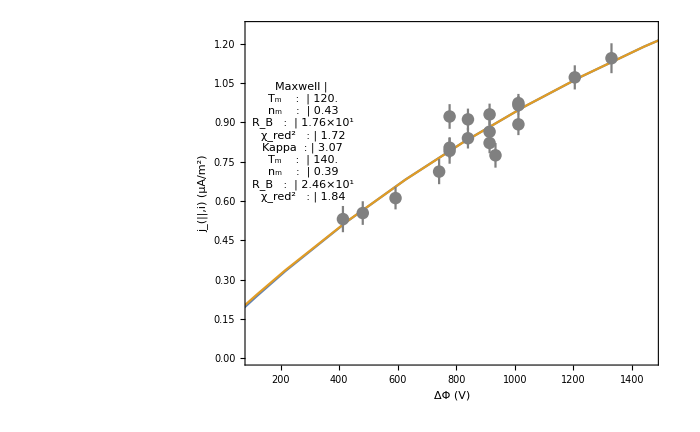

```mathematica
JVPlot=Show[Plot[{kFit[pot],gFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]
```

### J_E-V plot

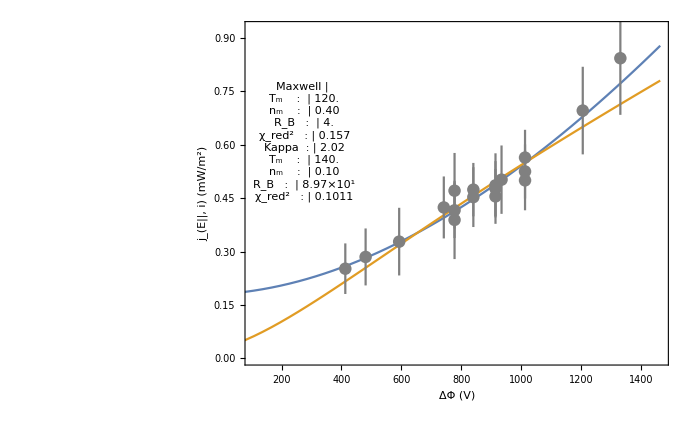

```mathematica
JeVPlot=Show[Plot[{kFitJeV[pot],gFitJeV[pot]},{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",Style[StringForm["J_E-V Fit (`1`)",combTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JeVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jeErrData,PlotStyle->Gray]]
```

### Plots from combined fit

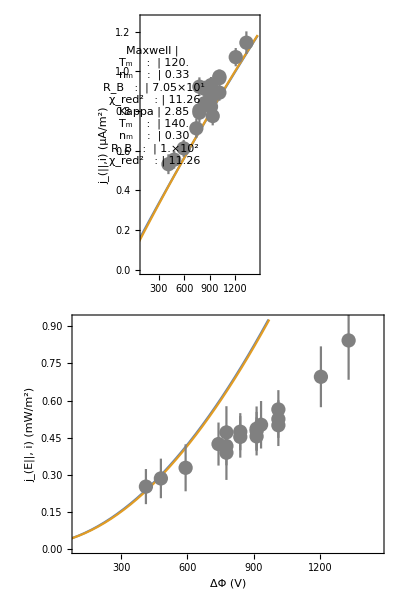

```mathematica
combPlot=Column[{combJVPlot,combJeVPlot}]
```

#### Triple fits

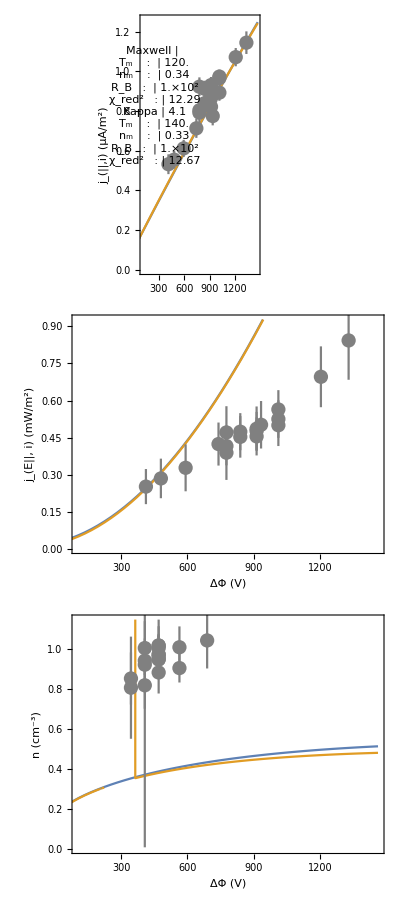

```mathematica
triplePlot=Column[{tripleJVPlot,tripleJeVPlot,tripleDensPlot}]
```

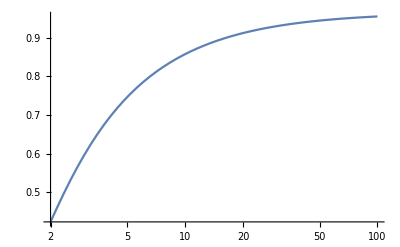

```mathematica
LogLinearPlot[LKMwellDensFac[100/50,RB],{RB,2,100},PlotRange->Full]
```

#### Save plots

```mathematica
If[makePlots==1,Print["Making plots in "<>dir<>" ..."];
Print[JVFilename<>" ..."];
Export[dir<>JVFilename,JVPlot];Print[JeVFilename<>" ..."];Export[dir<>JeVFilename,JeVPlot];Print[combFilename<>" ..."];Export[dir<>combFilename,combPlot];
Print[tripleFilename<>" ..."];
Export[dir<>tripleFilename,triplePlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/20180405/ ...

Orb1612__JVFit__inds_63-70__Automatic-fixT-peakE_indShift_eq_-1-avgItvl3.pdf ...

Orb1612__JeVFit__inds_63-70__Automatic-fixT-peakE_indShift_eq_-1-avgItvl3.pdf ...

Orb1612__combJVJeVFit__inds_63-70__Automatic-fixT-peakE_indShift_eq_-1-avgItvl3.pdf ...

Orb1612__tripleJVJeVDensFit__inds_63-70__Automatic-fixT-peakE_indShift_eq_-1-avgItvl3.pdf ...

Done!

## Density things

```mathematica
{I2JVFixT,I2JVNoFixT}={
Association["Maxwellian"->{140,0.79,15,∞},"Kappa"->{180,0.61,31.2,1.85}],
Association["Maxwellian"->{75,0.7,17.5,∞},"Kappa"->{76,0.70,17.9,34.9}]
};
```

```mathematica
fitType = "Maxwellian";
```

```mathematica
fitType = "Kappa";
```

#### These are derived using peakE_bounds_indShift=[0,0]

```mathematica
{Tm,nm,RB,kappam} = I2JVFixT[fitType];
```

```mathematica
RBSourceToFAST=7.894;
```

```mathematica
Manipulate[Manipulate[Show[tPlotRange[ind1,ind2,dens,densErr,pRangeDens,"Potential (ΔV)","Density (cm^-3)",usePot->densPot],Plot[{n*LKMwellDensFac[pot/T,RBAtFAST],n*LKKappaDensFac[pot/T,RBAtFAST,kappa]},{pot,1,Max[pots]},PlotRange->pRangeDens,Frame->True,FrameStyle->(FontSize->16),ImageSize->Large,FrameLabel->{"ΔΦ (V)","Density at FAST (cm^-3)"}]],{{RBAtFAST,RBSourceToFAST},2,300},{{T,Tm},10,500},{{n,nm},0.1,2},{{kappa,kappam},1.51,7.9},{{ind1,Min[{ind1Init,ind1End}]},ind1Start,ind1End,1},
{{ind2,Max[{ind2Init,ind1End+1}]},ind1End+1,Length@pots,1}],
{{ind1End,ind1EndInit},2,Length@pots-2,1}]
```